# Qualitative description of origami folding solutions

## (O5)

### ADG 2012 paper

```mathematica
Clear[parabola,pcstr];
```

We use the general equation of a curve. A curve is a parabola if the coefficients A, B and CC statisfy the condition B^2 - 4 A CC = 0.

```mathematica
parabola[x_,y_]:=A x^2+B x y+CC y^2+DD x+EE y+F
```

```mathematica
pcstr1=B^2->  4A CC
```

B^2→4 A CC

```mathematica
pcstr2=4A CC -> B^2
```

4 A CC→B^2

A tangent to a parabola at the point (x1, y1).

```mathematica
ptg[x_,y_,x1_,y1_]:= (D[parabola[x,y],x]/.{x-> x1, y-> y1})(x-x1)+ (D[parabola[x,y],y]/.{x-> x1, y-> y1})(y-y1)
```

In case of (O5), the tangent passes through a point Q (xq, yq).
parabola[x1,y1] point (x1, y1) is on the parabola.
ptg[xq,yq,x1,y1] the tangent to the parabola at point (x1, y1) passes through Q (xq,yq).

```mathematica
eqs=(#== 0)&/@{parabola[x1,y1],ptg[xq,yq,x1,y1]}
```

{F+DD x1+A x1^2+EE y1+B x1 y1+CC y1^2==0,(-x1+xq) (DD+2 A x1+B y1)+(EE+B x1+2 CC y1) (-y1+yq)==0}

A second degree polynomial equation is obtained from solving the above equations by eliminating either x1 or y1. Obviously, the number of real solutions is less or equal to 2.

```mathematica
Eliminate[eqs,{y1}]
```

4 CC F^2+F (-EE^2+4 CC DD x1-2 B EE x1+4 CC DD xq-2 B^2 x1 xq+8 A CC x1 xq+B^2 xq^2+4 CC EE yq+4 B CC xq yq+4 CC^2 yq^2)==-CC DD^2 x1^2+B DD EE x1^2-A EE^2 x1^2+DD EE^2 xq-2 CC DD^2 x1 xq+2 A EE^2 x1 xq+B^2 DD x1^2 xq-4 A CC DD x1^2 xq-CC DD^2 xq^2+B DD EE xq^2-4 A CC DD x1 xq^2+2 A B EE x1 xq^2+A B^2 x1^2 xq^2-4 A^2 CC x1^2 xq^2+EE^3 yq-4 CC DD EE x1 yq+2 B EE^2 x1 yq+B^2 EE x1^2 yq-4 A CC EE x1^2 yq+B EE^2 xq yq-4 B CC DD x1 xq yq+2 B^2 EE x1 xq yq+B^3 x1^2 xq yq-4 A B CC x1^2 xq yq+CC EE^2 yq^2-4 CC^2 DD x1 yq^2+2 B CC EE x1 yq^2+B^2 CC x1^2 yq^2-4 A CC^2 x1^2 yq^2

```mathematica
eq=Eliminate[eqs,{y1}]/.pcstr1
```

4 CC F^2+F (-EE^2+4 CC DD x1-2 B EE x1+4 CC DD xq+4 A CC xq^2+4 CC EE yq+4 B CC xq yq+4 CC^2 yq^2)==-CC DD^2 x1^2+B DD EE x1^2-A EE^2 x1^2+DD EE^2 xq-2 CC DD^2 x1 xq+2 A EE^2 x1 xq-CC DD^2 xq^2+B DD EE xq^2-4 A CC DD x1 xq^2+2 A B EE x1 xq^2+EE^3 yq-4 CC DD EE x1 yq+2 B EE^2 x1 yq+B EE^2 xq yq-4 B CC DD x1 xq yq+8 A CC EE x1 xq yq+B^3 x1^2 xq yq-4 A B CC x1^2 xq yq+CC EE^2 yq^2-4 CC^2 DD x1 yq^2+2 B CC EE x1 yq^2

```mathematica
poly=4 CC F^2+F (-EE^2+4 CC DD x1-2 B EE x1+4 CC DD xq+4 A CC xq^2+4 CC EE yq+4 B CC xq yq+4 CC^2 yq^2)-(-CC DD^2 x1^2+B DD EE x1^2-A EE^2 x1^2+DD EE^2 xq-2 CC DD^2 x1 xq+2 A EE^2 x1 xq-CC DD^2 xq^2+B DD EE xq^2-4 A CC DD x1 xq^2+2 A B EE x1 xq^2+EE^3 yq-4 CC DD EE x1 yq+2 B EE^2 x1 yq+B EE^2 xq yq-4 B CC DD x1 xq yq+8 A CC EE x1 xq yq+B^3 x1^2 xq yq-4 A B CC x1^2 xq yq+CC EE^2 yq^2-4 CC^2 DD x1 yq^2+2 B CC EE x1 yq^2)
```

```mathematica
Discriminant[poly,x1]/.pcstr1
```

4 (CC DD^2 EE^2 F-B DD EE^3 F+A EE^4 F+CC DD^3 EE^2 xq-B DD^2 EE^3 xq+A DD EE^4 xq+2 B CC DD^2 EE F xq-8 A CC DD EE^2 F xq+2 A B EE^3 F xq+2 B CC DD^3 EE xq^2-7 A CC DD^2 EE^2 xq^2+A B DD EE^3 xq^2+A^2 EE^4 xq^2+4 A CC^2 DD^2 F xq^2-4 A B CC DD EE F xq^2+4 A^2 CC EE^2 F xq^2+4 A CC^2 DD^3 xq^3-2 A B CC DD^2 EE xq^3-4 A^2 CC DD EE^2 xq^3+2 A^2 B EE^3 xq^3+4 A^2 CC^2 DD^2 xq^4-4 A^2 B CC DD EE xq^4+4 A^3 CC EE^2 xq^4+CC DD^2 EE^3 yq-B DD EE^4 yq+A EE^5 yq+4 CC^2 DD^2 EE F yq-4 B CC DD EE^2 F yq+4 A CC EE^3 F yq+4 CC^2 DD^3 EE xq yq-B CC DD^2 EE^2 xq yq-8 A CC DD EE^3 xq yq+3 A B EE^4 xq yq+4 B CC^2 DD^2 F xq yq-16 A CC^2 DD EE F xq yq-B^3 EE^2 F xq yq+8 A B CC EE^2 F xq yq+4 B^3 CC F^2 xq yq-16 A B CC^2 F^2 xq yq+4 B CC^2 DD^3 xq^2 yq-B^3 DD EE^2 xq^2 yq-8 A B CC DD EE^2 xq^2 yq+16 A^2 CC EE^3 xq^2 yq+4 B^3 CC DD F xq^2 yq-16 A B CC^2 DD F xq^2 yq+B^3 CC DD^2 xq^3 yq+4 A B CC^2 DD^2 xq^3 yq-B^4 DD EE xq^3 yq-16 A^2 CC^2 DD EE xq^3 yq+8 A^2 B CC EE^2 xq^3 yq+4 A B^3 CC F xq^3 yq-16 A^2 B CC^2 F xq^3 yq+5 CC^2 DD^2 EE^2 yq^2-5 B CC DD EE^3 yq^2+5 A CC EE^4 yq^2+4 CC^3 DD^2 F yq^2-4 B CC^2 DD EE F yq^2+4 A CC^2 EE^2 F yq^2+4 CC^3 DD^3 xq yq^2+6 B CC^2 DD^2 EE xq yq^2-36 A CC^2 DD EE^2 xq yq^2-B^3 EE^3 xq yq^2+14 A B CC EE^3 xq yq^2+4 B^3 CC EE F xq yq^2-16 A B CC^2 EE F xq yq^2+24 A CC^3 DD^2 xq^2 yq^2-24 A B CC^2 DD EE xq^2 yq^2-B^4 EE^2 xq^2 yq^2+40 A^2 CC^2 EE^2 xq^2 yq^2+4 B^4 CC F xq^2 yq^2-64 A^2 CC^3 F xq^2 yq^2+8 CC^3 DD^2 EE yq^3-8 B CC^2 DD EE^2 yq^3+8 A CC^2 EE^3 yq^3+8 B CC^3 DD^2 xq yq^3-32 A CC^3 DD EE xq yq^3-B^3 CC EE^2 xq yq^3+12 A B CC^2 EE^2 xq yq^3+4 B^3 CC^2 F xq yq^3-16 A B CC^3 F xq yq^3+4 CC^4 DD^2 yq^4-4 B CC^3 DD EE yq^4+4 A CC^3 EE^2 yq^4)

```mathematica
Eliminate[eqs,{x1}]
```

4 A F^2+F (-DD^2+4 A DD xq+4 A^2 xq^2-2 B DD y1+4 A EE y1+4 A EE yq+4 A B xq yq-2 B^2 y1 yq+8 A CC y1 yq+B^2 yq^2)==DD^3 xq+A DD^2 xq^2+2 B DD^2 xq y1-4 A DD EE xq y1+2 A B DD xq^2 y1-4 A^2 EE xq^2 y1-CC DD^2 y1^2+B DD EE y1^2-A EE^2 y1^2+B^2 DD xq y1^2-4 A CC DD xq y1^2+A B^2 xq^2 y1^2-4 A^2 CC xq^2 y1^2+DD^2 EE yq+B DD^2 xq yq+2 CC DD^2 y1 yq-2 A EE^2 y1 yq+2 B^2 DD xq y1 yq-4 A B EE xq y1 yq+B^2 EE y1^2 yq-4 A CC EE y1^2 yq+B^3 xq y1^2 yq-4 A B CC xq y1^2 yq+B DD EE yq^2-A EE^2 yq^2+2 B CC DD y1 yq^2-4 A CC EE y1 yq^2+B^2 CC y1^2 yq^2-4 A CC^2 y1^2 yq^2

```mathematica
Eliminate[eqs,{x1}]/.pcstr1
```

4 A F^2+F (-DD^2+4 A DD xq+4 A^2 xq^2-2 B DD y1+4 A EE y1+4 A EE yq+4 A B xq yq+4 A CC yq^2)==DD^3 xq+A DD^2 xq^2+2 B DD^2 xq y1-4 A DD EE xq y1+2 A B DD xq^2 y1-4 A^2 EE xq^2 y1-CC DD^2 y1^2+B DD EE y1^2-A EE^2 y1^2+DD^2 EE yq+B DD^2 xq yq+2 CC DD^2 y1 yq-2 A EE^2 y1 yq+8 A CC DD xq y1 yq-4 A B EE xq y1 yq+B^3 xq y1^2 yq-4 A B CC xq y1^2 yq+B DD EE yq^2-A EE^2 yq^2+2 B CC DD y1 yq^2-4 A CC EE y1 yq^2

### Solutions of operation (O5)

```mathematica
P=OPoint[p1,p2];Q=OPoint[q1,q2];
```

```mathematica
m=OLine[am,bm,cm];
```

```mathematica
parabolaeq1=ODistance[OPoint[x,y],P]^2-ODistanceSq[OPoint[x,y],m]
```

(-p1+x)^2+(-p2+y)^2-(cm+am x+bm y)^2/(am^2+bm^2)

```mathematica
parabola=(am^2+bm^2)((-p1+x)^2+(-p2+y)^2)-(cm+am x+bm y)^2
```

-(cm+am x+bm y)^2+(am^2+bm^2) ((-p1+x)^2+(-p2+y)^2)

```mathematica
tgparabola=(D[parabola,x]/.{x-> x1, y-> y1})(x-x1)+ (D[parabola,y]/.{x-> x1, y-> y1})(y-y1)
```

(x-x1) (2 (am^2+bm^2) (-p1+x1)-2 am (cm+am x1+bm y1))+(y-y1) (2 (am^2+bm^2) (-p2+y1)-2 bm (cm+am x1+bm y1))

```mathematica
cst1=tgparabola/.{x-> q1,y-> q2}
```

(q1-x1) (2 (am^2+bm^2) (-p1+x1)-2 am (cm+am x1+bm y1))+(q2-y1) (2 (am^2+bm^2) (-p2+y1)-2 bm (cm+am x1+bm y1))

```mathematica
cst2=parabola/.{x-> x1,y-> y1}
```

-(cm+am x1+bm y1)^2+(am^2+bm^2) ((-p1+x1)^2+(-p2+y1)^2)

```mathematica
List@@LineCC[Line[am,bm,cm]]
```

{(-1+bm) bm==0,(-1+am) (-1+bm)==0,1+am^2≠0}

```mathematica
gbx1=GroebnerBasis[Join[{cst1==0,cst2==0},{(-1+bm) bm==0,(-1+am) (-1+bm)==0}],{x1},{y1}]
```

GroebnerBasis::poly: 2\ (-am\ cm\ q1 - am^2\ p1\ q1 - bm^2\ p1\ q1 - bm\ cm\ q2 - am^2\ p2\ q2 - bm^2\ p2\ q2 + am\ cm\ x1 + am^2\ p1\ x1 + bm^2\ p1\ x1 + bm^2\ q1\ x1 - am\ bm\ q2\ x1 - bm^2\ x1^2 + bm\ cm\ y1 + am^2\ p2\ y1 + bm^2\ p2\ y1 - am\ bm\ q1\ y1 + am^2\ q2\ y1 + 2\ am\ bm\ x1\ y1 - am^2\ y1^2) == 0 is not a polynomial.

GroebnerBasis[{(q1-x1) (2 (am^2+bm^2) (-p1+x1)-2 am (cm+am x1+bm y1))+(q2-y1) (2 (am^2+bm^2) (-p2+y1)-2 bm (cm+am x1+bm y1))==0,-(cm+am x1+bm y1)^2+(am^2+bm^2) ((-p1+x1)^2+(-p2+y1)^2)==0,(-1+bm) bm==0,(-1+am) (-1+bm)==0,1+am^2≠0},{x1},{y1}]

```mathematica
Discriminant[gbx1[[1]],x1]//FullSimplify
```

4 (am^2+bm^2)^2 (cm+am p1+bm p2)^2 (bm^2 p2+bm (cm+am q1)+am^2 (p2-q2))^2 (-cm^2+bm^2 ((p1-q1)^2+p2 (p2-2 q2))+am^2 (p1 (p1-2 q1)+(p2-q2)^2)-2 am bm q1 q2-2 cm (am q1+bm q2))

```mathematica
ss=(am^2+bm^2)((p1-q1)^2+(p2-q2)^2)-(am q1+bm q2+cm)^2//Expand
```

-cm^2+am^2 p1^2+bm^2 p1^2+am^2 p2^2+bm^2 p2^2-2 am cm q1-2 am^2 p1 q1-2 bm^2 p1 q1+bm^2 q1^2-2 bm cm q2-2 am^2 p2 q2-2 bm^2 p2 q2-2 am bm q1 q2+am^2 q2^2

```mathematica
(bm^2 p2+bm (cm+am q1)+am^2 (p2-q2))^2//Expand
```

bm^2 cm^2+2 am^2 bm cm p2+2 bm^3 cm p2+am^4 p2^2+2 am^2 bm^2 p2^2+bm^4 p2^2+2 am bm^2 cm q1+2 am^3 bm p2 q1+2 am bm^3 p2 q1+am^2 bm^2 q1^2-2 am^2 bm cm q2-2 am^4 p2 q2-2 am^2 bm^2 p2 q2-2 am^3 bm q1 q2+am^4 q2^2

```mathematica
(-cm^2+bm^2 ((p1-q1)^2+p2 (p2-2 q2))+am^2 (p1 (p1-2 q1)+(p2-q2)^2)-2 am bm q1 q2-2 cm (am q1+bm q2))//Expand
```

-cm^2+am^2 p1^2+bm^2 p1^2+am^2 p2^2+bm^2 p2^2-2 am cm q1-2 am^2 p1 q1-2 bm^2 p1 q1+bm^2 q1^2-2 bm cm q2-2 am^2 p2 q2-2 bm^2 p2 q2-2 am bm q1 q2+am^2 q2^2

```mathematica
gby1=GroebnerBasis[{cst1==0,cst2==0,μ(am p1+bm p2+cm)-1== 0},{y1},{x1,μ}]
```

{am^2 cm^3+bm^2 cm^3+am^3 cm^2 p1+am bm^2 cm^2 p1-am^4 cm p1^2-2 am^2 bm^2 cm p1^2-bm^4 cm p1^2-am^5 p1^3-2 am^3 bm^2 p1^3-am bm^4 p1^3-am^2 bm cm^2 p2-bm^3 cm^2 p2+am^4 bm p1^2 p2+2 am^2 bm^3 p1^2 p2+bm^5 p1^2 p2-am^4 cm p2^2-2 am^2 bm^2 cm p2^2-bm^4 cm p2^2-am^5 p1 p2^2-2 am^3 bm^2 p1 p2^2-am bm^4 p1 p2^2+am^4 bm p2^3+2 am^2 bm^3 p2^3+bm^5 p2^3+2 am^3 cm^2 q1+2 am bm^2 cm^2 q1+4 am^4 cm p1 q1+6 am^2 bm^2 cm p1 q1+2 bm^4 cm p1 q1+2 am^5 p1^2 q1+4 am^3 bm^2 p1^2 q1+2 am bm^4 p1^2 q1-2 am^3 bm cm p2 q1-2 am bm^3 cm p2 q1-2 am^4 bm p1 p2 q1-4 am^2 bm^3 p1 p2 q1-2 bm^5 p1 p2 q1-am^2 bm^2 cm q1^2-bm^4 cm q1^2-am^3 bm^2 p1 q1^2-am bm^4 p1 q1^2+am^2 bm^3 p2 q1^2+bm^5 p2 q1^2+2 am^2 bm cm^2 q2+2 bm^3 cm^2 q2+2 am^3 bm cm p1 q2+2 am bm^3 cm p1 q2+2 am^4 cm p2 q2+2 am^2 bm^2 cm p2 q2+2 am^5 p1 p2 q2+4 am^3 bm^2 p1 p2 q2+2 am bm^4 p1 p2 q2-2 am^4 bm p2^2 q2-4 am^2 bm^3 p2^2 q2-2 bm^5 p2^2 q2+2 am^3 bm cm q1 q2+2 am bm^3 cm q1 q2+2 am^4 bm p1 q1 q2+2 am^2 bm^3 p1 q1 q2-2 am^3 bm^2 p2 q1 q2-2 am bm^4 p2 q1 q2+am^2 bm^2 cm q2^2+bm^4 cm q2^2+am^3 bm^2 p1 q2^2+am bm^4 p1 q2^2+2 am^4 bm p2 q2^2+3 am^2 bm^3 p2 q2^2+bm^5 p2 q2^2+2 am^2 bm cm^2 y1+2 bm^3 cm^2 y1-2 am^4 bm p1^2 y1-4 am^2 bm^3 p1^2 y1-2 bm^5 p1^2 y1-2 am^4 bm p2^2 y1-4 am^2 bm^3 p2^2 y1-2 bm^5 p2^2 y1+4 am^3 bm cm q1 y1+4 am bm^3 cm q1 y1+4 am^4 bm p1 q1 y1+8 am^2 bm^3 p1 q1 y1+4 bm^5 p1 q1 y1-2 am^2 bm^3 q1^2 y1-2 bm^5 q1^2 y1-2 am^4 cm q2 y1+2 bm^4 cm q2 y1-2 am^5 p1 q2 y1-4 am^3 bm^2 p1 q2 y1-2 am bm^4 p1 q2 y1+2 am^4 bm p2 q2 y1+4 am^2 bm^3 p2 q2 y1+2 bm^5 p2 q2 y1+4 am^3 bm^2 q1 q2 y1+4 am bm^4 q1 q2 y1-2 am^4 bm q2^2 y1-2 am^2 bm^3 q2^2 y1+am^4 cm y1^2+2 am^2 bm^2 cm y1^2+bm^4 cm y1^2+am^5 p1 y1^2+2 am^3 bm^2 p1 y1^2+am bm^4 p1 y1^2+am^4 bm p2 y1^2+2 am^2 bm^3 p2 y1^2+bm^5 p2 y1^2}

```mathematica
Discriminant[gby1[[1]],y1]//FullSimplify
```

4 (am^2+bm^2)^2 (am^2 p1+bm^2 (p1-q1)+am (cm+bm q2))^2 (-cm^2+bm^2 ((p1-q1)^2+p2 (p2-2 q2))+am^2 (p1 (p1-2 q1)+(p2-q2)^2)-2 am bm q1 q2-2 cm (am q1+bm q2))

```mathematica
(cm+am p1+bm p2)^2 (am^2 p1+bm^2 (p1-q1)+am (cm+bm q2))^2 //Expand
```

am^2 cm^4+4 am^3 cm^3 p1+2 am bm^2 cm^3 p1+6 am^4 cm^2 p1^2+6 am^2 bm^2 cm^2 p1^2+bm^4 cm^2 p1^2+4 am^5 cm p1^3+6 am^3 bm^2 cm p1^3+2 am bm^4 cm p1^3+am^6 p1^4+2 am^4 bm^2 p1^4+am^2 bm^4 p1^4+2 am^2 bm cm^3 p2+6 am^3 bm cm^2 p1 p2+4 am bm^3 cm^2 p1 p2+6 am^4 bm cm p1^2 p2+8 am^2 bm^3 cm p1^2 p2+2 bm^5 cm p1^2 p2+2 am^5 bm p1^3 p2+4 am^3 bm^3 p1^3 p2+2 am bm^5 p1^3 p2+am^2 bm^2 cm^2 p2^2+2 am^3 bm^2 cm p1 p2^2+2 am bm^4 cm p1 p2^2+am^4 bm^2 p1^2 p2^2+2 am^2 bm^4 p1^2 p2^2+bm^6 p1^2 p2^2-2 am bm^2 cm^3 q1-6 am^2 bm^2 cm^2 p1 q1-2 bm^4 cm^2 p1 q1-6 am^3 bm^2 cm p1^2 q1-4 am bm^4 cm p1^2 q1-2 am^4 bm^2 p1^3 q1-2 am^2 bm^4 p1^3 q1-4 am bm^3 cm^2 p2 q1-8 am^2 bm^3 cm p1 p2 q1-4 bm^5 cm p1 p2 q1-4 am^3 bm^3 p1^2 p2 q1-4 am bm^5 p1^2 p2 q1-2 am bm^4 cm p2^2 q1-2 am^2 bm^4 p1 p2^2 q1-2 bm^6 p1 p2^2 q1+bm^4 cm^2 q1^2+2 am bm^4 cm p1 q1^2+am^2 bm^4 p1^2 q1^2+2 bm^5 cm p2 q1^2+2 am bm^5 p1 p2 q1^2+bm^6 p2^2 q1^2+2 am^2 bm cm^3 q2+6 am^3 bm cm^2 p1 q2+2 am bm^3 cm^2 p1 q2+6 am^4 bm cm p1^2 q2+4 am^2 bm^3 cm p1^2 q2+2 am^5 bm p1^3 q2+2 am^3 bm^3 p1^3 q2+4 am^2 bm^2 cm^2 p2 q2+8 am^3 bm^2 cm p1 p2 q2+4 am bm^4 cm p1 p2 q2+4 am^4 bm^2 p1^2 p2 q2+4 am^2 bm^4 p1^2 p2 q2+2 am^2 bm^3 cm p2^2 q2+2 am^3 bm^3 p1 p2^2 q2+2 am bm^5 p1 p2^2 q2-2 am bm^3 cm^2 q1 q2-4 am^2 bm^3 cm p1 q1 q2-2 am^3 bm^3 p1^2 q1 q2-4 am bm^4 cm p2 q1 q2-4 am^2 bm^4 p1 p2 q1 q2-2 am bm^5 p2^2 q1 q2+am^2 bm^2 cm^2 q2^2+2 am^3 bm^2 cm p1 q2^2+am^4 bm^2 p1^2 q2^2+2 am^2 bm^3 cm p2 q2^2+2 am^3 bm^3 p1 p2 q2^2+am^2 bm^4 p2^2 q2^2

#### 0 solutions when d (Q, P) <= d (P, m)

#### 1 solution

cm + am p1 + bm p2 = 0 means that P is on line m.

(-cm^2+bm^2 ((p1-q1)^2+p2 (p2-2 q2))+am^2 (p1 (p1-2 q1)+(p2-q2)^2)-2 am bm q1 q2-2 cm (am q1+bm q2)) = means that d (Q,P)=d (P,m) or Q is on the parabola.

#### bm^2 p2+bm (cm+am q1)+am^2 (p2-q2) = 0

```mathematica
eqx=bm^2 p2+bm (cm+am q1)+am^2 (p2-q2)
```

bm^2 p2+bm (cm+am q1)+am^2 (p2-q2)

```mathematica
eqy=am^2 p1+bm^2 (p1-q1)+am (cm+bm q2)
```

am^2 p1+bm^2 (p1-q1)+am (cm+bm q2)

```mathematica
{eqx/.{p1-> 0,p2-> 5,q1-> 2,q2-> 5,am-> 2,bm-> -1,cm-> 1},eqy/.{p1-> 0,p2-> 5,q1-> 2,q2-> 5,am-> 2,bm-> -1,cm-> 1}}
```

{0,-10}

```mathematica
Solve[{cst1== 0,cst2== 0}/.{p1-> 0,p2-> 5,q1-> 2,q2-> 5,am-> 2,bm-> -1,cm-> 1},{x1,y1}]
```

{{x1→0,y1→6-√5},{x1→0,y1→6+√5}}

```mathematica
{eqx/.{p1-> 0,p2-> 2,q1-> 2,q2-> 1,am-> 0,bm-> 1,cm-> -2},eqy/.{p1-> 0,p2-> 2,q1-> 2,q2-> 1,am-> 0,bm-> 1,cm-> -2}}
```

{0,-2}

```mathematica
Solve[{cst1== 0,cst2== 0}/.{p1-> 0,p2-> 2,q1-> 2,q2-> 1,am-> 0,bm-> 1,cm-> -2},{x1,y1}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x1→0}}

It simply means that x1 is the same in both solutions!

```mathematica
{eqx/.{p1-> 2,p2-> 4,q1-> 2,q2-> 2,am-> 1,bm-> -1,cm-> 2},eqy/.{p1-> 2,p2-> 4,q1-> 2,q2-> 2,am-> 1,bm-> -1,cm-> 2}}
```

{2,2}

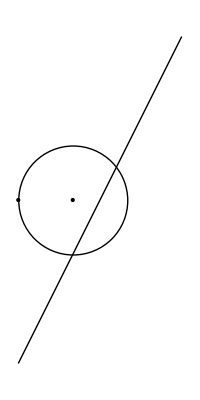

```mathematica
Graphics[{Line[{{0,-1},{6,11}}],Point[{0,5}],Point[{2,5}],Circle[{2,5},2]}]
```

### Solutions of operation (O5) Optimization?

```mathematica
P=OPoint[p1,p2];Q=OPoint[q1,q2];
```

```mathematica
m=OLine[am,bm,cm];
```

```mathematica
parabolaeq1=ODistance[OPoint[x,y],P]^2-ODistanceSq[OPoint[x,y],m]
```

(-p1+x)^2+(-p2+y)^2-(cm+am x+bm y)^2/(am^2+bm^2)

```mathematica
parabola=(am^2+bm^2)((-p1+x)^2+(-p2+y)^2)-(cm+am x+bm y)^2
```

-(cm+am x+bm y)^2+(am^2+bm^2) ((-p1+x)^2+(-p2+y)^2)

```mathematica
tgparabola=(D[parabolaeq1,x]/.{x-> x1, y-> y1})(x-x1)+ (D[parabola,y]/.{x-> x1, y-> y1})(y-y1)
```

(x-x1) (2 (-p1+x1)-(2 am (cm+am x1+bm y1))/(am^2+bm^2))

```mathematica
cst1=tgparabola/.{x-> q1,y-> q2}
```

(q1-x1) (2 (-p1+x1)-(2 am (cm+am x1+bm y1))/(am^2+bm^2))

```mathematica
cst2=parabolaeq1/.{x-> x1,y-> y1}
```

(-p1+x1)^2+(-p2+y1)^2-(cm+am x1+bm y1)^2/(am^2+bm^2)

```mathematica
gbx1=GroebnerBasis[{cst1==0,cst2==0},{x1},{y1},CoefficientDomain->RationalFunctions]
```

{-(am^2 cm^2 q1)/((am^2+bm^2)^2)-(2 am cm p1 q1)/(am^2+bm^2)-p1^2 q1-(am^2 bm^2 p1^2 q1)/((am^2+bm^2)^2)+(bm^2 p1^2 q1)/(am^2+bm^2)-(2 am^2 bm cm p2 q1)/((am^2+bm^2)^2)-(2 am bm p1 p2 q1)/(am^2+bm^2)-(am^2 bm^2 p2^2 q1)/((am^2+bm^2)^2)+((am^2 cm^2)/((am^2+bm^2)^2)+(2 am cm p1)/(am^2+bm^2)+p1^2+(am^2 bm^2 p1^2)/((am^2+bm^2)^2)-(bm^2 p1^2)/(am^2+bm^2)+(2 am^2 bm cm p2)/((am^2+bm^2)^2)+(2 am bm p1 p2)/(am^2+bm^2)+(am^2 bm^2 p2^2)/((am^2+bm^2)^2)-(2 am^3 cm q1)/((am^2+bm^2)^2)+(2 am cm q1)/(am^2+bm^2)+2 p1 q1+(2 am^2 bm^2 p1 q1)/((am^2+bm^2)^2)-(2 am^2 p1 q1)/(am^2+bm^2)-(2 bm^2 p1 q1)/(am^2+bm^2)-(2 am^3 bm p2 q1)/((am^2+bm^2)^2)+(2 am bm p2 q1)/(am^2+bm^2)) x1+((2 am^3 cm)/((am^2+bm^2)^2)-(2 am cm)/(am^2+bm^2)-2 p1-(2 am^2 bm^2 p1)/((am^2+bm^2)^2)+(2 am^2 p1)/(am^2+bm^2)+(2 bm^2 p1)/(am^2+bm^2)+(2 am^3 bm p2)/((am^2+bm^2)^2)-(2 am bm p2)/(am^2+bm^2)-q1-(am^4 q1)/((am^2+bm^2)^2)-(am^2 bm^2 q1)/((am^2+bm^2)^2)+(2 am^2 q1)/(am^2+bm^2)+(bm^2 q1)/(am^2+bm^2)) x1^2}

```mathematica
Discriminant[gbx1[[1]],x1]//FullSimplify
```

(am^2 (cm+am p1+bm p2)^2 (am^2 p1+am (cm+bm p2)+2 bm^2 (p1-q1))^2)/((am^2+bm^2)^4)

```mathematica
(am^2+bm^2)((p1-q1)^2+(p2-q2)^2)-(am q1+bm q2+cm)^2//Expand
```

-cm^2+am^2 p1^2+bm^2 p1^2+am^2 p2^2+bm^2 p2^2-2 am cm q1-2 am^2 p1 q1-2 bm^2 p1 q1+bm^2 q1^2-2 bm cm q2-2 am^2 p2 q2-2 bm^2 p2 q2-2 am bm q1 q2+am^2 q2^2

```mathematica
(-cm^2+bm^2 ((p1-q1)^2+p2 (p2-2 q2))+am^2 (p1 (p1-2 q1)+(p2-q2)^2)-2 am bm q1 q2-2 cm (am q1+bm q2))//Expand
```

-cm^2+am^2 p1^2+bm^2 p1^2+am^2 p2^2+bm^2 p2^2-2 am cm q1-2 am^2 p1 q1-2 bm^2 p1 q1+bm^2 q1^2-2 bm cm q2-2 am^2 p2 q2-2 bm^2 p2 q2-2 am bm q1 q2+am^2 q2^2

```mathematica
gby1=GroebnerBasis[{cst1==0,cst2==0},{y1},{x1}]
```

{am^2 cm^4+bm^2 cm^4+2 am^3 cm^3 p1+2 am bm^2 cm^3 p1-am^2 bm^2 cm^2 p1^2-bm^4 cm^2 p1^2-2 am^5 cm p1^3-4 am^3 bm^2 cm p1^3-2 am bm^4 cm p1^3-am^6 p1^4-2 am^4 bm^2 p1^4-am^2 bm^4 p1^4-am^4 cm^2 p2^2-3 am^2 bm^2 cm^2 p2^2-2 bm^4 cm^2 p2^2-2 am^5 cm p1 p2^2-4 am^3 bm^2 cm p1 p2^2-2 am bm^4 cm p1 p2^2-am^6 p1^2 p2^2-am^4 bm^2 p1^2 p2^2+am^2 bm^4 p1^2 p2^2+bm^6 p1^2 p2^2+am^4 bm^2 p2^4+2 am^2 bm^4 p2^4+bm^6 p2^4+2 am^3 cm^3 q1+2 am bm^2 cm^3 q1+6 am^4 cm^2 p1 q1+8 am^2 bm^2 cm^2 p1 q1+2 bm^4 cm^2 p1 q1+6 am^5 cm p1^2 q1+10 am^3 bm^2 cm p1^2 q1+4 am bm^4 cm p1^2 q1+2 am^6 p1^3 q1+4 am^4 bm^2 p1^3 q1+2 am^2 bm^4 p1^3 q1-2 am^3 bm^2 cm p2^2 q1-2 am bm^4 cm p2^2 q1-2 am^4 bm^2 p1 p2^2 q1-4 am^2 bm^4 p1 p2^2 q1-2 bm^6 p1 p2^2 q1-am^2 bm^2 cm^2 q1^2-bm^4 cm^2 q1^2-2 am^3 bm^2 cm p1 q1^2-2 am bm^4 cm p1 q1^2-am^4 bm^2 p1^2 q1^2-am^2 bm^4 p1^2 q1^2+am^2 bm^4 p2^2 q1^2+bm^6 p2^2 q1^2+2 am^2 bm cm^3 q2+2 bm^3 cm^3 q2+4 am^3 bm cm^2 p1 q2+4 am bm^3 cm^2 p1 q2+2 am^4 bm cm p1^2 q2+2 am^2 bm^3 cm p1^2 q2+2 am^4 cm^2 p2 q2+4 am^2 bm^2 cm^2 p2 q2+2 bm^4 cm^2 p2 q2+4 am^5 cm p1 p2 q2+8 am^3 bm^2 cm p1 p2 q2+4 am bm^4 cm p1 p2 q2+2 am^6 p1^2 p2 q2+4 am^4 bm^2 p1^2 p2 q2+2 am^2 bm^4 p1^2 p2 q2-2 am^2 bm^3 cm p2^2 q2-2 bm^5 cm p2^2 q2-2 am^4 bm^2 p2^3 q2-4 am^2 bm^4 p2^3 q2-2 bm^6 p2^3 q2+2 am^3 bm cm^2 q1 q2+2 am bm^3 cm^2 q1 q2+4 am^4 bm cm p1 q1 q2+4 am^2 bm^3 cm p1 q1 q2+2 am^5 bm p1^2 q1 q2+2 am^3 bm^3 p1^2 q1 q2-2 am^3 bm^3 p2^2 q1 q2-2 am bm^5 p2^2 q1 q2+am^2 bm^2 cm^2 q2^2+bm^4 cm^2 q2^2+2 am^3 bm^2 cm p1 q2^2+2 am bm^4 cm p1 q2^2+am^4 bm^2 p1^2 q2^2+am^2 bm^4 p1^2 q2^2+2 am^4 bm cm p2 q2^2+4 am^2 bm^3 cm p2 q2^2+2 bm^5 cm p2 q2^2+2 am^5 bm p1 p2 q2^2+4 am^3 bm^3 p1 p2 q2^2+2 am bm^5 p1 p2 q2^2+2 am^4 bm^2 p2^2 q2^2+3 am^2 bm^4 p2^2 q2^2+bm^6 p2^2 q2^2+2 am^2 bm cm^3 y1+2 bm^3 cm^3 y1+2 am^3 bm cm^2 p1 y1+2 am bm^3 cm^2 p1 y1-2 am^4 bm cm p1^2 y1-4 am^2 bm^3 cm p1^2 y1-2 bm^5 cm p1^2 y1-2 am^5 bm p1^3 y1-4 am^3 bm^3 p1^3 y1-2 am bm^5 p1^3 y1+2 am^2 bm^2 cm^2 p2 y1+2 bm^4 cm^2 p2 y1-2 am^4 bm^2 p1^2 p2 y1-4 am^2 bm^4 p1^2 p2 y1-2 bm^6 p1^2 p2 y1-2 am^4 bm cm p2^2 y1-4 am^2 bm^3 cm p2^2 y1-2 bm^5 cm p2^2 y1-2 am^5 bm p1 p2^2 y1-4 am^3 bm^3 p1 p2^2 y1-2 am bm^5 p1 p2^2 y1-2 am^4 bm^2 p2^3 y1-4 am^2 bm^4 p2^3 y1-2 bm^6 p2^3 y1+4 am^3 bm cm^2 q1 y1+4 am bm^3 cm^2 q1 y1+8 am^4 bm cm p1 q1 y1+12 am^2 bm^3 cm p1 q1 y1+4 bm^5 cm p1 q1 y1+4 am^5 bm p1^2 q1 y1+8 am^3 bm^3 p1^2 q1 y1+4 am bm^5 p1^2 q1 y1+4 am^3 bm^2 cm p2 q1 y1+4 am bm^4 cm p2 q1 y1+4 am^4 bm^2 p1 p2 q1 y1+8 am^2 bm^4 p1 p2 q1 y1+4 bm^6 p1 p2 q1 y1-2 am^2 bm^3 cm q1^2 y1-2 bm^5 cm q1^2 y1-2 am^3 bm^3 p1 q1^2 y1-2 am bm^5 p1 q1^2 y1-2 am^2 bm^4 p2 q1^2 y1-2 bm^6 p2 q1^2 y1-2 am^4 cm^2 q2 y1+2 bm^4 cm^2 q2 y1-4 am^5 cm p1 q2 y1-4 am^3 bm^2 cm p1 q2 y1-2 am^6 p1^2 q2 y1-4 am^4 bm^2 p1^2 q2 y1-2 am^2 bm^4 p1^2 q2 y1+4 am^2 bm^3 cm p2 q2 y1+4 bm^5 cm p2 q2 y1+2 am^4 bm^2 p2^2 q2 y1+4 am^2 bm^4 p2^2 q2 y1+2 bm^6 p2^2 q2 y1+4 am^3 bm^2 cm q1 q2 y1+4 am bm^4 cm q1 q2 y1+4 am^4 bm^2 p1 q1 q2 y1+4 am^2 bm^4 p1 q1 q2 y1+4 am^3 bm^3 p2 q1 q2 y1+4 am bm^5 p2 q1 q2 y1-2 am^4 bm cm q2^2 y1-2 am^2 bm^3 cm q2^2 y1-2 am^5 bm p1 q2^2 y1-2 am^3 bm^3 p1 q2^2 y1-2 am^4 bm^2 p2 q2^2 y1-2 am^2 bm^4 p2 q2^2 y1+am^4 cm^2 y1^2+2 am^2 bm^2 cm^2 y1^2+bm^4 cm^2 y1^2+2 am^5 cm p1 y1^2+4 am^3 bm^2 cm p1 y1^2+2 am bm^4 cm p1 y1^2+am^6 p1^2 y1^2+2 am^4 bm^2 p1^2 y1^2+am^2 bm^4 p1^2 y1^2+2 am^4 bm cm p2 y1^2+4 am^2 bm^3 cm p2 y1^2+2 bm^5 cm p2 y1^2+2 am^5 bm p1 p2 y1^2+4 am^3 bm^3 p1 p2 y1^2+2 am bm^5 p1 p2 y1^2+am^4 bm^2 p2^2 y1^2+2 am^2 bm^4 p2^2 y1^2+bm^6 p2^2 y1^2}

```mathematica
Discriminant[gby1[[1]],y1]//FullSimplify
```

4 (am^2+bm^2)^2 (cm+am p1+bm p2)^2 (am^2 p1+bm^2 (p1-q1)+am (cm+bm q2))^2 (-cm^2+bm^2 ((p1-q1)^2+p2 (p2-2 q2))+am^2 (p1 (p1-2 q1)+(p2-q2)^2)-2 am bm q1 q2-2 cm (am q1+bm q2))

```mathematica
Solve[am^2 p1+bm^2 (p1-q1)+am (cm+bm q2)== 0,{q1,q2}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{q2→-(am cm+am^2 p1+bm^2 p1)/(am bm)+(bm q1)/am}}

```mathematica
(cm+am p1+bm p2)^2 (am^2 p1+bm^2 (p1-q1)+am (cm+bm q2))^2 //Expand
```

am^2 cm^4+4 am^3 cm^3 p1+2 am bm^2 cm^3 p1+6 am^4 cm^2 p1^2+6 am^2 bm^2 cm^2 p1^2+bm^4 cm^2 p1^2+4 am^5 cm p1^3+6 am^3 bm^2 cm p1^3+2 am bm^4 cm p1^3+am^6 p1^4+2 am^4 bm^2 p1^4+am^2 bm^4 p1^4+2 am^2 bm cm^3 p2+6 am^3 bm cm^2 p1 p2+4 am bm^3 cm^2 p1 p2+6 am^4 bm cm p1^2 p2+8 am^2 bm^3 cm p1^2 p2+2 bm^5 cm p1^2 p2+2 am^5 bm p1^3 p2+4 am^3 bm^3 p1^3 p2+2 am bm^5 p1^3 p2+am^2 bm^2 cm^2 p2^2+2 am^3 bm^2 cm p1 p2^2+2 am bm^4 cm p1 p2^2+am^4 bm^2 p1^2 p2^2+2 am^2 bm^4 p1^2 p2^2+bm^6 p1^2 p2^2-2 am bm^2 cm^3 q1-6 am^2 bm^2 cm^2 p1 q1-2 bm^4 cm^2 p1 q1-6 am^3 bm^2 cm p1^2 q1-4 am bm^4 cm p1^2 q1-2 am^4 bm^2 p1^3 q1-2 am^2 bm^4 p1^3 q1-4 am bm^3 cm^2 p2 q1-8 am^2 bm^3 cm p1 p2 q1-4 bm^5 cm p1 p2 q1-4 am^3 bm^3 p1^2 p2 q1-4 am bm^5 p1^2 p2 q1-2 am bm^4 cm p2^2 q1-2 am^2 bm^4 p1 p2^2 q1-2 bm^6 p1 p2^2 q1+bm^4 cm^2 q1^2+2 am bm^4 cm p1 q1^2+am^2 bm^4 p1^2 q1^2+2 bm^5 cm p2 q1^2+2 am bm^5 p1 p2 q1^2+bm^6 p2^2 q1^2+2 am^2 bm cm^3 q2+6 am^3 bm cm^2 p1 q2+2 am bm^3 cm^2 p1 q2+6 am^4 bm cm p1^2 q2+4 am^2 bm^3 cm p1^2 q2+2 am^5 bm p1^3 q2+2 am^3 bm^3 p1^3 q2+4 am^2 bm^2 cm^2 p2 q2+8 am^3 bm^2 cm p1 p2 q2+4 am bm^4 cm p1 p2 q2+4 am^4 bm^2 p1^2 p2 q2+4 am^2 bm^4 p1^2 p2 q2+2 am^2 bm^3 cm p2^2 q2+2 am^3 bm^3 p1 p2^2 q2+2 am bm^5 p1 p2^2 q2-2 am bm^3 cm^2 q1 q2-4 am^2 bm^3 cm p1 q1 q2-2 am^3 bm^3 p1^2 q1 q2-4 am bm^4 cm p2 q1 q2-4 am^2 bm^4 p1 p2 q1 q2-2 am bm^5 p2^2 q1 q2+am^2 bm^2 cm^2 q2^2+2 am^3 bm^2 cm p1 q2^2+am^4 bm^2 p1^2 q2^2+2 am^2 bm^3 cm p2 q2^2+2 am^3 bm^3 p1 p2 q2^2+am^2 bm^4 p2^2 q2^2

#### 0 solutions when d (Q, P) <= d (P, m)

#### 1 solution

cm + am p1 + bm p2 = 0 means that P is on line m.

(-cm^2+bm^2 ((p1-q1)^2+p2 (p2-2 q2))+am^2 (p1 (p1-2 q1)+(p2-q2)^2)-2 am bm q1 q2-2 cm (am q1+bm q2)) = means that d (Q,P)=d (P,m) or Q is on the parabola.

#### bm^2 p2+bm (cm+am q1)+am^2 (p2-q2) = 0

```mathematica
eqx=bm^2 p2+bm (cm+am q1)+am^2 (p2-q2)
```

bm^2 p2+bm (cm+am q1)+am^2 (p2-q2)

```mathematica
eqy=am^2 p1+bm^2 (p1-q1)+am (cm+bm q2)
```

am^2 p1+bm^2 (p1-q1)+am (cm+bm q2)

```mathematica
{eqx/.{p1-> 0,p2-> 5,q1-> 2,q2-> 5,am-> 2,bm-> -1,cm-> 1},eqy/.{p1-> 0,p2-> 5,q1-> 2,q2-> 5,am-> 2,bm-> -1,cm-> 1}}
```

{0,-10}

```mathematica
Solve[{cst1== 0,cst2== 0}/.{p1-> 0,p2-> 5,q1-> 2,q2-> 5,am-> 2,bm-> -1,cm-> 1},{x1,y1}]
```

{{x1→0,y1→6-√5},{x1→0,y1→6+√5}}

```mathematica
{eqx/.{p1-> 0,p2-> 2,q1-> 2,q2-> 1,am-> 0,bm-> 1,cm-> -2},eqy/.{p1-> 0,p2-> 2,q1-> 2,q2-> 1,am-> 0,bm-> 1,cm-> -2}}
```

{0,-2}

```mathematica
Solve[{cst1== 0,cst2== 0}/.{p1-> 0,p2-> 2,q1-> 2,q2-> 1,am-> 0,bm-> 1,cm-> -2},{x1,y1}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x1→0}}

It simply means that x1 is the same in both solutions!

```mathematica
{eqx/.{p1-> 2,p2-> 4,q1-> 2,q2-> 2,am-> 1,bm-> -1,cm-> 2},eqy/.{p1-> 2,p2-> 4,q1-> 2,q2-> 2,am-> 1,bm-> -1,cm-> 2}}
```

{2,2}

```mathematica
Graphics[{Line[{{0,-1},{6,11}}],Point[{0,5}],Point[{2,5}],Circle[{2,5},2]}]
```

-Graphics-

### (O5) with different constraints

```mathematica
P=OPoint[p1,p2];Q=OPoint[q1,q2];
```

```mathematica
m=OLine[am,bm,cm];
```

Equation of parabola (P, m)

```mathematica
parabolaeq1=ODistance[OPoint[x,y],P]^2-ODistanceSq[OPoint[x,y],m]
```

(-p1+x)^2+(-p2+y)^2-(cm+am x+bm y)^2/(am^2+bm^2)

```mathematica
parabola=(am^2+bm^2)((-p1+x)^2+(-p2+y)^2)-(cm+am x+bm y)^2
```

-(cm+am x+bm y)^2+(am^2+bm^2) ((-p1+x)^2+(-p2+y)^2)

```mathematica
tgparabola1=(D[parabola,x]/.{x-> x1, y-> y1})+ (D[parabola,y]/.{x-> x1, y-> y1})t
```

2 (am^2+bm^2) (-p1+x1)-2 am (cm+am x1+bm y1)+t (2 (am^2+bm^2) (-p2+y1)-2 bm (cm+am x1+bm y1))

```mathematica
cst1=tgparabola1/.{x-> q1,y-> q2}
```

2 (am^2+bm^2) (-p1+x1)-2 am (cm+am x1+bm y1)+t (2 (am^2+bm^2) (-p2+y1)-2 bm (cm+am x1+bm y1))

```mathematica
cst2=parabola/.{x-> x1,y-> y1}
```

-(cm+am x1+bm y1)^2+(am^2+bm^2) ((-p1+x1)^2+(-p2+y1)^2)

```mathematica
cst3=(y1-q2)-t(x1-q1)
```

-q2-t (-q1+x1)+y1

```mathematica
gb=GroebnerBasis[{cst1==0,cst2==0,cst3== 0(*,η(cm+am p1+bm p2)-1== 0*)},{t},{x1,y1(*,η*)}]//FullSimplify
```

{(am^2+bm^2) (cm+am p1+bm p2) (-cm-(cm-am p1+bm p2+2 am q1) t^2-am (p1+2 (p2-q2) t)+bm (p2-2 (q2+(p1-q1) t)))}

```mathematica
d=Discriminant[gb,t]//FullSimplify
```

{4 (am^2+bm^2)^2 (cm+am p1+bm p2)^2 (-cm^2+bm^2 ((p1-q1)^2+p2 (p2-2 q2))+am^2 (p1 (p1-2 q1)+(p2-q2)^2)-2 am bm q1 q2-2 cm (am q1+bm q2))}

```mathematica
dd=(am^2+bm^2)((p1-q1)^2+(p2-q2)^2)-(am q1+bm q2+cm)^2//Expand
```

-cm^2+am^2 p1^2+bm^2 p1^2+am^2 p2^2+bm^2 p2^2-2 am cm q1-2 am^2 p1 q1-2 bm^2 p1 q1+bm^2 q1^2-2 bm cm q2-2 am^2 p2 q2-2 bm^2 p2 q2-2 am bm q1 q2+am^2 q2^2

```mathematica
dd-(-cm^2+bm^2 ((p1-q1)^2+p2 (p2-2 q2))+am^2 (p1 (p1-2 q1)+(p2-q2)^2)-2 am bm q1 q2-2 cm (am q1+bm q2))//FullSimplify
```

0

## (O6)

### Solutions of operation (O6) (ADG paper)

```mathematica
P=OPoint[p1,p2];Q=OPoint[q1,q2];
```

```mathematica
m=OLine[am,bm,cm];n=OLine[an,bn,cn];
```

```mathematica
parabolaeq1=ODistance[OPoint[x,y],P]^2-ODistanceSq[OPoint[x,y],m]
```

(-p1+x)^2+(-p2+y)^2-(cm+am x+bm y)^2/(am^2+bm^2)

```mathematica
parabola1=(am^2+bm^2)((-p1+x)^2+(-p2+y)^2)-(cm+am x+bm y)^2//Expand
```

-cm^2+am^2 p1^2+bm^2 p1^2+am^2 p2^2+bm^2 p2^2-2 am cm x-2 am^2 p1 x-2 bm^2 p1 x+bm^2 x^2-2 bm cm y-2 am^2 p2 y-2 bm^2 p2 y-2 am bm x y+am^2 y^2

```mathematica
parabolaeq2=ODistance[OPoint[x,y],Q]^2-ODistanceSq[OPoint[x,y],n]
```

(-q1+x)^2+(-q2+y)^2-(cn+an x+bn y)^2/(an^2+bn^2)

```mathematica
parabola2=(an^2+bn^2)((-q1+x)^2+(-q2+y)^2)-(cn+an x+bn y)^2//Expand
```

-cn^2+an^2 q1^2+bn^2 q1^2+an^2 q2^2+bn^2 q2^2-2 an cn x-2 an^2 q1 x-2 bn^2 q1 x+bn^2 x^2-2 bn cn y-2 an^2 q2 y-2 bn^2 q2 y-2 an bn x y+an^2 y^2

```mathematica
tgp1=-2am cm-2am^2p1-2bm^2p1+2bm^2x-2am bm y+(-2bm cm-2am^2p2-2bm^2p2-2am bm x+2am^2 y)t
```

-2 am cm-2 am^2 p1-2 bm^2 p1+2 bm^2 x-2 am bm y+t (-2 bm cm-2 am^2 p2-2 bm^2 p2-2 am bm x+2 am^2 y)

```mathematica
tgparabola2=(D[parabola2,x]/.{x-> x2, y-> y2})(x-x2)+ (D[parabola2,y]/.{x-> x2, y-> y2})(y-y2)
```

(y-y2) (-2 bn cn-2 an^2 q2-2 bn^2 q2-2 an bn x2+2 an^2 y2)+(x-x2) (-2 an cn-2 an^2 q1-2 bn^2 q1+2 bn^2 x2-2 an bn y2)

```mathematica
tgp2=-2an cn-2an^2q1-2bn^2q1+2bn^2x-2an bn y+(-2bn cn-2an^2q2-2bn^2q2-2an bn x+2an^2y)t
```

-2 an cn-2 an^2 q1-2 bn^2 q1+2 bn^2 x-2 an bn y+t (-2 bn cn-2 an^2 q2-2 bn^2 q2-2 an bn x+2 an^2 y)

```mathematica
cst1=tgp1/.{x-> x1,y-> y1}
```

-2 am cm-2 am^2 p1-2 bm^2 p1+2 bm^2 x1-2 am bm y1+t (-2 bm cm-2 am^2 p2-2 bm^2 p2-2 am bm x1+2 am^2 y1)

```mathematica
cst2=tgp2/.{x-> x2,y-> y2}
```

-2 an cn-2 an^2 q1-2 bn^2 q1+2 bn^2 x2-2 an bn y2+t (-2 bn cn-2 an^2 q2-2 bn^2 q2-2 an bn x2+2 an^2 y2)

```mathematica
cst3=parabola1/.{x-> x1,y-> y1}
```

-cm^2+am^2 p1^2+bm^2 p1^2+am^2 p2^2+bm^2 p2^2-2 am cm x1-2 am^2 p1 x1-2 bm^2 p1 x1+bm^2 x1^2-2 bm cm y1-2 am^2 p2 y1-2 bm^2 p2 y1-2 am bm x1 y1+am^2 y1^2

```mathematica
cst4=parabola2/.{x-> x2,y-> y2}
```

-cn^2+an^2 q1^2+bn^2 q1^2+an^2 q2^2+bn^2 q2^2-2 an cn x2-2 an^2 q1 x2-2 bn^2 q1 x2+bn^2 x2^2-2 bn cn y2-2 an^2 q2 y2-2 bn^2 q2 y2-2 an bn x2 y2+an^2 y2^2

```mathematica
cst5=(y1-y2)-t (x1-x2)
```

-t (x1-x2)+y1-y2

```mathematica
{cst1,cst2,cst3,cst4,cst5}
```

{-2 am cm-2 am^2 p1-2 bm^2 p1+2 bm^2 x1-2 am bm y1+t (-2 bm cm-2 am^2 p2-2 bm^2 p2-2 am bm x1+2 am^2 y1),-2 an cn-2 an^2 q1-2 bn^2 q1+2 bn^2 x2-2 an bn y2+t (-2 bn cn-2 an^2 q2-2 bn^2 q2-2 an bn x2+2 an^2 y2),-cm^2+am^2 p1^2+bm^2 p1^2+am^2 p2^2+bm^2 p2^2-2 am cm x1-2 am^2 p1 x1-2 bm^2 p1 x1+bm^2 x1^2-2 bm cm y1-2 am^2 p2 y1-2 bm^2 p2 y1-2 am bm x1 y1+am^2 y1^2,-cn^2+an^2 q1^2+bn^2 q1^2+an^2 q2^2+bn^2 q2^2-2 an cn x2-2 an^2 q1 x2-2 bn^2 q1 x2+bn^2 x2^2-2 bn cn y2-2 an^2 q2 y2-2 bn^2 q2 y2-2 an bn x2 y2+an^2 y2^2,-t (x1-x2)+y1-y2}

```mathematica
gb=TimeConstrained[GroebnerBasis[{cst1,cst2,cst3,cst4,cst5},{t},{x1,y1,x2,y2},CoefficientDomain->RationalFunctions],60]
```

{bn cm-bm cn+am bn p1-bm bn p2-an bm q1+bm bn q2+(-an cm+am cn-am an p1+2 bm bn p1+an bm p2+2 am bn p2+am an q1-2 bm bn q1-2 an bm q2-am bn q2) t+(bn cm-bm cn-2 an bm p1-am bn p1-2 am an p2+bm bn p2+an bm q1+2 am bn q1+2 am an q2-bm bn q2) t^2+(-an cm+am cn+am an p1-an bm p2-am an q1+am bn q2) t^3}

```mathematica
Discriminant[gb[[1]],t]//FactorTermsList
```

{4,-an^4 cm^4-2 an^2 bn^2 cm^4-bn^4 cm^4+4 am an^3 cm^3 cn+4 an^2 bm bn cm^3 cn+4 am an bn^2 cm^3 cn+1597+2 am^2 an^2 bm^2 bn^2 q2^4+an^2 bm^4 bn^2 q2^4-4 am^3 an bm bn^3 q2^4+4 am an bm^3 bn^3 q2^4+am^4 bn^4 q2^4-2 am^2 bm^2 bn^4 q2^4+bm^4 bn^4 q2^4}
 |  |  |  |

```mathematica
%//Length
```

2

```mathematica
mapping={an-> am,bn-> bm,cn-> k cm}
```

{an→am,bn→bm,cn→cm k}

```mathematica
gbparallelcase=TimeConstrained[GroebnerBasis[{cst1,cst2,cst3,cst4,cst5}/.mapping,{t},{x1,y1,x2,y2},CoefficientDomain->RationalFunctions],60]
```

{cm-cm k+am p1-bm p2-am q1+bm q2+(2 bm p1+2 am p2-2 bm q1-2 am q2) t+(cm-cm k-am p1+bm p2+am q1-bm q2) t^2}

```mathematica
Discriminant[gbparallelcase[[1]],t]//FullSimplify
```

4 (-cm^2 (-1+k)^2+(am^2+bm^2) ((p1-q1)^2+(p2-q2)^2))

```mathematica
(-an cm+am cn+am an p1-an bm p2-am an q1+am bn q2)/.mapping//FullSimplify
```

am (cm (-1+k)+am (p1-q1)+bm (-p2+q2))

```mathematica
GroebnerBasis[{cst1,cst2,cst3,cst4},{t},{x1,y1,x2,y2}]
```

$Aborted

### Solutions of operation (O6) (GB aborted)

```mathematica
P=OPoint[p1,p2];Q=OPoint[q1,q2];
```

```mathematica
m=OLine[am,bm,cm];n=OLine[an,bn,cn];
```

```mathematica
parabolaeq1=ODistance[OPoint[x,y],P]^2-ODistanceSq[OPoint[x,y],m]
```

(-p1+x)^2+(-p2+y)^2-(cm+am x+bm y)^2/(am^2+bm^2)

```mathematica
parabola1=(am^2+bm^2)((-p1+x)^2+(-p2+y)^2)-(cm+am x+bm y)^2
```

-(cm+am x+bm y)^2+(am^2+bm^2) ((-p1+x)^2+(-p2+y)^2)

```mathematica
parabolaeq2=ODistance[OPoint[x,y],Q]^2-ODistanceSq[OPoint[x,y],n]
```

(-q1+x)^2+(-q2+y)^2-(cn+an x+bn y)^2/(an^2+bn^2)

```mathematica
parabola2=(an^2+bn^2)((-q1+x)^2+(-q2+y)^2)-(cn+an x+bn y)^2
```

-(cn+an x+bn y)^2+(an^2+bn^2) ((-q1+x)^2+(-q2+y)^2)

```mathematica
tgparabola1=(D[parabola1,x]/.{x-> x1, y-> y1})(x-x1)+ (D[parabola1,y]/.{x-> x1, y-> y1})(y-y1)
```

(x-x1) (2 (am^2+bm^2) (-p1+x1)-2 am (cm+am x1+bm y1))+(y-y1) (2 (am^2+bm^2) (-p2+y1)-2 bm (cm+am x1+bm y1))

```mathematica
tgparabola2=(D[parabola2,x]/.{x-> x2, y-> y2})(x-x2)+ (D[parabola2,y]/.{x-> x2, y-> y2})(y-y2)
```

(x-x2) (2 (an^2+bn^2) (-q1+x2)-2 an (cn+an x2+bn y2))+(y-y2) (2 (an^2+bn^2) (-q2+y2)-2 bn (cn+an x2+bn y2))

```mathematica
cst1=tgparabola1/.{x-> x2,y-> y2}
```

(-x1+x2) (2 (am^2+bm^2) (-p1+x1)-2 am (cm+am x1+bm y1))+(2 (am^2+bm^2) (-p2+y1)-2 bm (cm+am x1+bm y1)) (-y1+y2)

```mathematica
cst2=tgparabola2/.{x-> x1,y-> y1}
```

(x1-x2) (2 (an^2+bn^2) (-q1+x2)-2 an (cn+an x2+bn y2))+(y1-y2) (2 (an^2+bn^2) (-q2+y2)-2 bn (cn+an x2+bn y2))

```mathematica
cst3=parabola1/.{x-> x1,y-> y1}
```

-(cm+am x1+bm y1)^2+(am^2+bm^2) ((-p1+x1)^2+(-p2+y1)^2)

```mathematica
cst4=parabola2/.{x-> x2,y-> y2}
```

-(cn+an x2+bn y2)^2+(an^2+bn^2) ((-q1+x2)^2+(-q2+y2)^2)

```mathematica
gbx1=GroebnerBasis[{cst1==0,cst2==0,cst3== 0,cst4== 0},{x1,x2},{y1,y2}]
```

$Aborted

```mathematica
GroebnerBasis[{cst1==0,cst2==0,cst3== 0,cst4== 0},{x1,x2},{y1,y2}]
```

### Case 1: m and n are parallel (General)

All parabola are similar.

```mathematica
P=OPoint[p1,p2];Q=OPoint[q1,q2];
```

```mathematica
m=OLine[am,bm,cm];n=OLine[am,bm,cn];
```

```mathematica
parabolaeq1=ODistance[OPoint[x,y],P]^2-ODistanceSq[OPoint[x,y],m]
```

(-p1+x)^2+(-p2+y)^2-(cm+am x+bm y)^2/(am^2+bm^2)

```mathematica
parabolaeq1=(am^2+bm^2)((-p1+x)^2+(-p2+y)^2)-(cm+am x+bm y)^2
```

-(cm+am x+bm y)^2+(am^2+bm^2) ((-p1+x)^2+(-p2+y)^2)

```mathematica
parabolaeq2=ODistance[OPoint[x,y],Q]^2-ODistanceSq[OPoint[x,y],n]
```

(-q1+x)^2+(-q2+y)^2-(cn+am x+bm y)^2/(am^2+bm^2)

```mathematica
parabolaeq2=(am^2+bm^2)((-q1+x)^2+(-q2+y)^2)-(cn+am x+bm y)^2
```

-(cn+am x+bm y)^2+(am^2+bm^2) ((-q1+x)^2+(-q2+y)^2)

```mathematica
tgparabola1=(D[parabolaeq1,x]/.{x-> x1, y-> y1})+ (D[parabolaeq1,y]/.{x-> x1, y-> y1})t
```

2 (am^2+bm^2) (-p1+x1)-2 am (cm+am x1+bm y1)+t (2 (am^2+bm^2) (-p2+y1)-2 bm (cm+am x1+bm y1))

```mathematica
tgparabola2=(D[parabolaeq2,x]/.{x-> x2, y-> y2})+ (D[parabolaeq2,y]/.{x-> x2, y-> y2})t
```

2 (am^2+bm^2) (-q1+x2)-2 am (cn+am x2+bm y2)+t (2 (am^2+bm^2) (-q2+y2)-2 bm (cn+am x2+bm y2))

```mathematica
cst1=tgparabola1/.{x-> x2,y-> y2}
```

2 (am^2+bm^2) (-p1+x1)-2 am (cm+am x1+bm y1)+t (2 (am^2+bm^2) (-p2+y1)-2 bm (cm+am x1+bm y1))

```mathematica
cst2=tgparabola2/.{x-> x1,y-> y1}
```

2 (am^2+bm^2) (-q1+x2)-2 am (cn+am x2+bm y2)+t (2 (am^2+bm^2) (-q2+y2)-2 bm (cn+am x2+bm y2))

```mathematica
cst3=parabolaeq1/.{x-> x1,y-> y1}
```

-(cm+am x1+bm y1)^2+(am^2+bm^2) ((-p1+x1)^2+(-p2+y1)^2)

```mathematica
cst4=parabolaeq2/.{x-> x2,y-> y2}
```

-(cn+am x2+bm y2)^2+(am^2+bm^2) ((-q1+x2)^2+(-q2+y2)^2)

```mathematica
cst5=(y2-y1)-t(x2-x1)
```

-t (-x1+x2)-y1+y2

```mathematica
gb=GroebnerBasis[{cst1==0,cst2==0,cst3== 0,cst4== 0,cst5== 0},{t},{x1,x2,y1,y2}]
```

$Aborted

```mathematica
Discriminant[gbx1,x1]//FullSimplify
```

$Aborted

```mathematica
f1=(cn p1^2+cn^2 p2+cn p2^2-p2 q1^2+p1^2 q2+p2^2 q2-p2 q2^2-cm^2 (cn+q2)+cm (cn^2-q2^2-(q1-x1)^2)-2 (-p2 q1+p1 (cn+q2)) x1+(cn-p2+q2) x1^2)//Expand
```

-cm^2 cn+cm cn^2+cn p1^2+cn^2 p2+cn p2^2-cm q1^2-p2 q1^2-cm^2 q2+p1^2 q2+p2^2 q2-cm q2^2-p2 q2^2-2 cn p1 x1+2 cm q1 x1+2 p2 q1 x1-2 p1 q2 x1-cm x1^2+cn x1^2-p2 x1^2+q2 x1^2

```mathematica
f2=(-cm^3+cn p1^2+p1^2 p2+cn p2^2+p2^3-2 p1 p2 q1+cm^2 (cn-p2-q2)+p1^2 q2-p2^2 q2-2 (-p2 q1+p1 (cn+q2)) x1+(cn-p2+q2) x1^2+cm (p2 (2 cn+p2-2 q2)+(p1-x1) (p1-2 q1+x1)))//Expand
```

-cm^3+cm^2 cn+cm p1^2+cn p1^2-cm^2 p2+2 cm cn p2+p1^2 p2+cm p2^2+cn p2^2+p2^3-2 cm p1 q1-2 p1 p2 q1-cm^2 q2+p1^2 q2-2 cm p2 q2-p2^2 q2-2 cn p1 x1+2 cm q1 x1+2 p2 q1 x1-2 p1 q2 x1-cm x1^2+cn x1^2-p2 x1^2+q2 x1^2

```mathematica
Exponent[f1,x1]
```

2

```mathematica
Exponent[f2,x1]
```

2

```mathematica
Exponent[gbx1[[1]],x1]
```

4

```mathematica
Discriminant[f1,x1]//FullSimplify
```

-4 (cm+p2) ((cm-cn)^2-(p1-q1)^2-(p2-q2)^2) (cn+q2)

```mathematica
Discriminant[f2,x1]//FullSimplify
```

-4 (cm+p2)^2 ((cm-cn)^2-(p1-q1)^2-(p2-q2)^2)

```mathematica
Discriminant[f2p,x1]//FullSimplify
```

-4 (cm+p2)^2 ((cm-cn)^2-(p1-q1)^2-(p2-q2)^2)

```mathematica
f2=cm^3+cm^2 (-cn+q2)-(cn+q2) x1^2+cm x1 (-2 q1+x1)
```

cm^3+cm^2 (-cn+q2)-(cn+q2) x1^2+cm x1 (-2 q1+x1)

```mathematica
Discriminant[f2,x1]//FullSimplify
```

4 cm^2 (-(cm-cn)^2+q1^2+q2^2)

```mathematica
Discriminant[gbx1[[1]],x1]//FullSimplify
```

16 cm^7 (cn+q2)^7 (-cm+cn+q2)^4 (-(cm-cn)^2+q1^2+q2^2)^6

```mathematica
gbx2=GroebnerBasis[{cst1==0,cst2==0,cst3== 0,cst4== 0},{x2},{x1,y1,y2}]
```

{cm^4 cn^3-2 cm^3 cn^4+cm^2 cn^5-cm^2 cn^3 p1^2+cm cn^4 p1^2-2 cm^2 cn^4 p2+2 cm cn^5 p2+cn^4 p1^2 p2-2 cm^2 cn^3 p2^2+2 cm cn^4 p2^2+cn^5 p2^2+cn^3 p1^2 p2^2+2 cn^4 p2^3+cn^3 p2^4-2 cm^3 cn^2 p1 q1+2 cm^2 cn^3 p1 q1+2 cm cn^2 p1^3 q1-2 cm^2 cn^2 p1 p2 q1+4 cm cn^3 p1 p2 q1+2 cn^2 p1^3 p2 q1+2 cm cn^2 p1 p2^2 q1+2 cn^3 p1 p2^2 q1+2 cn^2 p1 p2^3 q1+cm^4 cn q1^2+cm^3 cn^2 q1^2-2 cm^2 cn^3 q1^2-cm^2 cn p1^2 q1^2-cm cn^2 p1^2 q1^2+2 cm^3 cn p2 q1^2-cm^2 cn^2 p2 q1^2-4 cm cn^3 p2 q1^2-2 cm cn p1^2 p2 q1^2-cn^2 p1^2 p2 q1^2-5 cm cn^2 p2^2 q1^2-2 cn^3 p2^2 q1^2-cn p1^2 p2^2 q1^2-2 cm cn p2^3 q1^2-3 cn^2 p2^3 q1^2-cn p2^4 q1^2-2 cm^2 cn p1 q1^3-4 cm cn p1 p2 q1^3-2 cn p1 p2^2 q1^3+cm^3 q1^4+cm^2 cn q1^4+3 cm^2 p2 q1^4+2 cm cn p2 q1^4+3 cm p2^2 q1^4+cn p2^2 q1^4+p2^3 q1^4+3 cm^4 cn^2 q2-4 cm^3 cn^3 q2+cm^2 cn^4 q2-3 cm^2 cn^2 p1^2 q2+2 cm cn^3 p1^2 q2-4 cm^2 cn^3 p2 q2+2 cm cn^4 p2 q2+2 cn^3 p1^2 p2 q2-6 cm^2 cn^2 p2^2 q2+4 cm cn^3 p2^2 q2+cn^4 p2^2 q2+3 cn^2 p1^2 p2^2 q2+4 cn^3 p2^3 q2+3 cn^2 p2^4 q2-4 cm^3 cn p1 q1 q2+2 cm^2 cn^2 p1 q1 q2+4 cm cn p1^3 q1 q2-4 cm^2 cn p1 p2 q1 q2+4 cm cn^2 p1 p2 q1 q2+4 cn p1^3 p2 q1 q2+4 cm cn p1 p2^2 q1 q2+2 cn^2 p1 p2^2 q1 q2+4 cn p1 p2^3 q1 q2+cm^4 q1^2 q2+4 cm^3 cn q1^2 q2-2 cm^2 cn^2 q1^2 q2-cm^2 p1^2 q1^2 q2-2 cm cn p1^2 q1^2 q2+2 cm^3 p2 q1^2 q2+4 cm^2 cn p2 q1^2 q2-4 cm cn^2 p2 q1^2 q2-2 cm p1^2 p2 q1^2 q2-2 cn p1^2 p2 q1^2 q2-4 cm cn p2^2 q1^2 q2-2 cn^2 p2^2 q1^2 q2-p1^2 p2^2 q1^2 q2-2 cm p2^3 q1^2 q2-4 cn p2^3 q1^2 q2-p2^4 q1^2 q2-2 cm^2 p1 q1^3 q2-4 cm p1 p2 q1^3 q2-2 p1 p2^2 q1^3 q2+cm^2 q1^4 q2+2 cm p2 q1^4 q2+p2^2 q1^4 q2+3 cm^4 cn q2^2-2 cm^2 cn^3 q2^2-3 cm^2 cn p1^2 q2^2-4 cm cn^3 p2 q2^2-6 cm^2 cn p2^2 q2^2-2 cn^3 p2^2 q2^2+3 cn p1^2 p2^2 q2^2+3 cn p2^4 q2^2-2 cm^3 p1 q1 q2^2-2 cm^2 cn p1 q1 q2^2+2 cm p1^3 q1 q2^2-2 cm^2 p1 p2 q1 q2^2-4 cm cn p1 p2 q1 q2^2+2 p1^3 p2 q1 q2^2+2 cm p1 p2^2 q1 q2^2-2 cn p1 p2^2 q1 q2^2+2 p1 p2^3 q1 q2^2+3 cm^3 q1^2 q2^2+2 cm^2 cn q1^2 q2^2-cm p1^2 q1^2 q2^2+5 cm^2 p2 q1^2 q2^2+4 cm cn p2 q1^2 q2^2-p1^2 p2 q1^2 q2^2+cm p2^2 q1^2 q2^2+2 cn p2^2 q1^2 q2^2-p2^3 q1^2 q2^2+cm^4 q2^3+4 cm^3 cn q2^3-2 cm^2 cn^2 q2^3-cm^2 p1^2 q2^3-2 cm cn p1^2 q2^3+4 cm^2 cn p2 q2^3-4 cm cn^2 p2 q2^3-2 cn p1^2 p2 q2^3-2 cm^2 p2^2 q2^3-4 cm cn p2^2 q2^3-2 cn^2 p2^2 q2^3+p1^2 p2^2 q2^3-4 cn p2^3 q2^3+p2^4 q2^3-2 cm^2 p1 q1 q2^3-4 cm p1 p2 q1 q2^3-2 p1 p2^2 q1 q2^3+2 cm^2 q1^2 q2^3+4 cm p2 q1^2 q2^3+2 p2^2 q1^2 q2^3+2 cm^3 q2^4+cm^2 cn q2^4-cm p1^2 q2^4+2 cm^2 p2 q2^4+2 cm cn p2 q2^4-p1^2 p2 q2^4-2 cm p2^2 q2^4+cn p2^2 q2^4-2 p2^3 q2^4+cm^2 q2^5+2 cm p2 q2^5+p2^2 q2^5+2 cm^3 cn^2 p1 x2-2 cm cn^4 p1 x2-2 cm cn^2 p1^3 x2+2 cm^2 cn^2 p1 p2 x2-4 cm cn^3 p1 p2 x2-2 cn^4 p1 p2 x2-2 cn^2 p1^3 p2 x2-2 cm cn^2 p1 p2^2 x2-4 cn^3 p1 p2^2 x2-2 cn^2 p1 p2^3 x2-2 cm^4 cn q1 x2+2 cm^2 cn^3 q1 x2+2 cm^2 cn p1^2 q1 x2-4 cm cn^2 p1^2 q1 x2-4 cm^3 cn p2 q1 x2+4 cm^2 cn^2 p2 q1 x2+4 cm cn^3 p2 q1 x2+4 cm cn p1^2 p2 q1 x2-4 cn^2 p1^2 p2 q1 x2+8 cm cn^2 p2^2 q1 x2+2 cn^3 p2^2 q1 x2+2 cn p1^2 p2^2 q1 x2+4 cm cn p2^3 q1 x2+4 cn^2 p2^3 q1 x2+2 cn p2^4 q1 x2+8 cm^2 cn p1 q1^2 x2+2 cm cn^2 p1 q1^2 x2+16 cm cn p1 p2 q1^2 x2+2 cn^2 p1 p2 q1^2 x2+8 cn p1 p2^2 q1^2 x2-4 cm^3 q1^3 x2-2 cm^2 cn q1^3 x2-12 cm^2 p2 q1^3 x2-4 cm cn p2 q1^3 x2-12 cm p2^2 q1^3 x2-2 cn p2^2 q1^3 x2-4 p2^3 q1^3 x2+4 cm^3 cn p1 q2 x2+4 cm^2 cn^2 p1 q2 x2-4 cm cn^3 p1 q2 x2-4 cm cn p1^3 q2 x2+4 cm^2 cn p1 p2 q2 x2-4 cm cn^2 p1 p2 q2 x2-4 cn^3 p1 p2 q2 x2-4 cn p1^3 p2 q2 x2-4 cm cn p1 p2^2 q2 x2-8 cn^2 p1 p2^2 q2 x2-4 cn p1 p2^3 q2 x2-2 cm^4 q1 q2 x2-4 cm^3 cn q1 q2 x2+2 cm^2 cn^2 q1 q2 x2+2 cm^2 p1^2 q1 q2 x2-8 cm cn p1^2 q1 q2 x2-4 cm^3 p2 q1 q2 x2-4 cm^2 cn p2 q1 q2 x2+4 cm cn^2 p2 q1 q2 x2+4 cm p1^2 p2 q1 q2 x2-8 cn p1^2 p2 q1 q2 x2+4 cm cn p2^2 q1 q2 x2+2 cn^2 p2^2 q1 q2 x2+2 p1^2 p2^2 q1 q2 x2+4 cm p2^3 q1 q2 x2+4 cn p2^3 q1 q2 x2+2 p2^4 q1 q2 x2+8 cm^2 p1 q1^2 q2 x2+4 cm cn p1 q1^2 q2 x2+16 cm p1 p2 q1^2 q2 x2+4 cn p1 p2 q1^2 q2 x2+8 p1 p2^2 q1^2 q2 x2-2 cm^2 q1^3 q2 x2-4 cm p2 q1^3 q2 x2-2 p2^2 q1^3 q2 x2+2 cm^3 p1 q2^2 x2+8 cm^2 cn p1 q2^2 x2-2 cm p1^3 q2^2 x2+2 cm^2 p1 p2 q2^2 x2+4 cm cn p1 p2 q2^2 x2-2 p1^3 p2 q2^2 x2-2 cm p1 p2^2 q2^2 x2-4 cn p1 p2^2 q2^2 x2-2 p1 p2^3 q2^2 x2-4 cm^3 q1 q2^2 x2-2 cm^2 cn q1 q2^2 x2-4 cm p1^2 q1 q2^2 x2-8 cm^2 p2 q1 q2^2 x2-4 cm cn p2 q1 q2^2 x2-4 p1^2 p2 q1 q2^2 x2-4 cm p2^2 q1 q2^2 x2-2 cn p2^2 q1 q2^2 x2+2 cm p1 q1^2 q2^2 x2+2 p1 p2 q1^2 q2^2 x2+4 cm^2 p1 q2^3 x2+4 cm cn p1 q2^3 x2+4 cm p1 p2 q2^3 x2+4 cn p1 p2 q2^3 x2-2 cm^2 q1 q2^3 x2-4 cm p2 q1 q2^3 x2-2 p2^2 q1 q2^3 x2+2 cm p1 q2^4 x2+2 p1 p2 q2^4 x2+cm^4 cn x2^2-cm^3 cn^2 x2^2-cm^2 cn^3 x2^2+cm cn^4 x2^2-cm^2 cn p1^2 x2^2+5 cm cn^2 p1^2 x2^2+2 cm^3 cn p2 x2^2-3 cm^2 cn^2 p2 x2^2+cn^4 p2 x2^2-2 cm cn p1^2 p2 x2^2+5 cn^2 p1^2 p2 x2^2-3 cm cn^2 p2^2 x2^2+cn^3 p2^2 x2^2-cn p1^2 p2^2 x2^2-2 cm cn p2^3 x2^2-cn^2 p2^3 x2^2-cn p2^4 x2^2-10 cm^2 cn p1 q1 x2^2+2 cm cn^2 p1 q1 x2^2-20 cm cn p1 p2 q1 x2^2+2 cn^2 p1 p2 q1 x2^2-10 cn p1 p2^2 q1 x2^2+6 cm^3 q1^2 x2^2-cm^2 cn q1^2 x2^2-cm cn^2 q1^2 x2^2+18 cm^2 p2 q1^2 x2^2-2 cm cn p2 q1^2 x2^2-cn^2 p2 q1^2 x2^2+18 cm p2^2 q1^2 x2^2-cn p2^2 q1^2 x2^2+6 p2^3 q1^2 x2^2+cm^4 q2 x2^2-3 cm^2 cn^2 q2 x2^2+2 cm cn^3 q2 x2^2-cm^2 p1^2 q2 x2^2+10 cm cn p1^2 q2 x2^2+2 cm^3 p2 q2 x2^2+2 cn^3 p2 q2 x2^2-2 cm p1^2 p2 q2 x2^2+10 cn p1^2 p2 q2 x2^2+3 cn^2 p2^2 q2 x2^2-p1^2 p2^2 q2 x2^2-2 cm p2^3 q2 x2^2-p2^4 q2 x2^2-10 cm^2 p1 q1 q2 x2^2+4 cm cn p1 q1 q2 x2^2-20 cm p1 p2 q1 q2 x2^2+4 cn p1 p2 q1 q2 x2^2-10 p1 p2^2 q1 q2 x2^2-cm^2 q1^2 q2 x2^2-2 cm cn q1^2 q2 x2^2-2 cm p2 q1^2 q2 x2^2-2 cn p2 q1^2 q2 x2^2-p2^2 q1^2 q2 x2^2+cm^3 q2^2 x2^2-3 cm^2 cn q2^2 x2^2+5 cm p1^2 q2^2 x2^2+3 cm^2 p2 q2^2 x2^2+5 p1^2 p2 q2^2 x2^2+3 cm p2^2 q2^2 x2^2+3 cn p2^2 q2^2 x2^2+p2^3 q2^2 x2^2+2 cm p1 q1 q2^2 x2^2+2 p1 p2 q1 q2^2 x2^2-cm q1^2 q2^2 x2^2-p2 q1^2 q2^2 x2^2-cm^2 q2^3 x2^2-2 cm cn q2^3 x2^2-2 cn p2 q2^3 x2^2+p2^2 q2^3 x2^2-cm q2^4 x2^2-p2 q2^4 x2^2+4 cm^2 cn p1 x2^3-4 cm cn^2 p1 x2^3+8 cm cn p1 p2 x2^3-4 cn^2 p1 p2 x2^3+4 cn p1 p2^2 x2^3-4 cm^3 q1 x2^3+4 cm^2 cn q1 x2^3-12 cm^2 p2 q1 x2^3+8 cm cn p2 q1 x2^3-12 cm p2^2 q1 x2^3+4 cn p2^2 q1 x2^3-4 p2^3 q1 x2^3+4 cm^2 p1 q2 x2^3-8 cm cn p1 q2 x2^3+8 cm p1 p2 q2 x2^3-8 cn p1 p2 q2 x2^3+4 p1 p2^2 q2 x2^3+4 cm^2 q1 q2 x2^3+8 cm p2 q1 q2 x2^3+4 p2^2 q1 q2 x2^3-4 cm p1 q2^2 x2^3-4 p1 p2 q2^2 x2^3+cm^3 x2^4-2 cm^2 cn x2^4+cm cn^2 x2^4+3 cm^2 p2 x2^4-4 cm cn p2 x2^4+cn^2 p2 x2^4+3 cm p2^2 x2^4-2 cn p2^2 x2^4+p2^3 x2^4-2 cm^2 q2 x2^4+2 cm cn q2 x2^4-4 cm p2 q2 x2^4+2 cn p2 q2 x2^4-2 p2^2 q2 x2^4+cm q2^2 x2^4+p2 q2^2 x2^4}

```mathematica
Exponent[gbx2,x2]
```

{4}

```mathematica
Discriminant[gbx2[[1]],x2]//FullSimplify
```

$Aborted

```mathematica
gbx3=GroebnerBasis[{cst1==0,cst2==0,cst3== 0,cst4== 0},{y1},{x1,x2,y2}]
```

{cm^9 cn-2 cm^8 cn^2-cm^7 cn^3+4 cm^6 cn^4-cm^5 cn^5-2 cm^4 cn^6+cm^3 cn^7-3 cm^7 cn q1^2+4 cm^6 cn^2 q1^2-2 cm^5 cn^3 q1^2+4 cm^4 cn^4 q1^2-3 cm^3 cn^5 q1^2+3 cm^5 cn q1^4-2 cm^4 cn^2 q1^4+3 cm^3 cn^3 q1^4-cm^3 cn q1^6+cm^9 q2-2 cm^8 cn q2-cm^7 cn^2 q2+4 cm^6 cn^3 q2-cm^5 cn^4 q2-2 cm^4 cn^5 q2+cm^3 cn^6 q2-3 cm^7 q1^2 q2+4 cm^6 cn q1^2 q2-2 cm^5 cn^2 q1^2 q2+4 cm^4 cn^3 q1^2 q2-3 cm^3 cn^4 q1^2 q2+3 cm^5 q1^4 q2-2 cm^4 cn q1^4 q2+3 cm^3 cn^2 q1^4 q2-cm^3 q1^6 q2+2 cm^7 cn q2^2-4 cm^6 cn^2 q2^2+4 cm^4 cn^4 q2^2-2 cm^3 cn^5 q2^2-4 cm^4 cn^2 q1^2 q2^2+4 cm^3 cn^3 q1^2 q2^2-2 cm^3 cn q1^4 q2^2+2 cm^7 q2^3-4 cm^6 cn q2^3+4 cm^4 cn^3 q2^3-2 cm^3 cn^4 q2^3-4 cm^4 cn q1^2 q2^3+4 cm^3 cn^2 q1^2 q2^3-2 cm^3 q1^4 q2^3+cm^5 cn q2^4-2 cm^4 cn^2 q2^4+cm^3 cn^3 q2^4-cm^3 cn q1^2 q2^4+cm^5 q2^5-2 cm^4 cn q2^5+cm^3 cn^2 q2^5-cm^3 q1^2 q2^5+6 cm^8 cn y1-16 cm^7 cn^2 y1+6 cm^6 cn^3 y1+16 cm^5 cn^4 y1-14 cm^4 cn^5 y1+2 cm^2 cn^7 y1-14 cm^6 cn q1^2 y1+16 cm^5 cn^2 q1^2 y1+4 cm^4 cn^3 q1^2 y1-6 cm^2 cn^5 q1^2 y1+10 cm^4 cn q1^4 y1+6 cm^2 cn^3 q1^4 y1-2 cm^2 cn q1^6 y1+6 cm^8 q2 y1-22 cm^7 cn q2 y1+16 cm^6 cn^2 q2 y1+20 cm^5 cn^3 q2 y1-26 cm^4 cn^4 q2 y1+2 cm^3 cn^5 q2 y1+4 cm^2 cn^6 q2 y1-14 cm^6 q1^2 q2 y1+20 cm^5 cn q1^2 q2 y1+8 cm^4 cn^2 q1^2 q2 y1-4 cm^3 cn^3 q1^2 q2 y1-10 cm^2 cn^4 q1^2 q2 y1+10 cm^4 q1^4 q2 y1+2 cm^3 cn q1^4 q2 y1+8 cm^2 cn^2 q1^4 q2 y1-2 cm^2 q1^6 q2 y1-6 cm^7 q2^2 y1+18 cm^6 cn q2^2 y1-16 cm^5 cn^2 q2^2 y1+6 cm^3 cn^4 q2^2 y1-2 cm^2 cn^5 q2^2 y1+4 cm^5 q1^2 q2^2 y1-8 cm^3 cn^2 q1^2 q2^2 y1+4 cm^2 cn^3 q1^2 q2^2 y1+2 cm^3 q1^4 q2^2 y1-2 cm^2 cn q1^4 q2^2 y1+8 cm^6 q2^3 y1-28 cm^5 cn q2^3 y1+24 cm^4 cn^2 q2^3 y1+4 cm^3 cn^3 q2^3 y1-8 cm^2 cn^4 q2^3 y1-4 cm^4 q1^2 q2^3 y1-4 cm^3 cn q1^2 q2^3 y1+12 cm^2 cn^2 q1^2 q2^3 y1-4 cm^2 q1^4 q2^3 y1-8 cm^5 q2^4 y1+14 cm^4 cn q2^4 y1-4 cm^3 cn^2 q2^4 y1-2 cm^2 cn^3 q2^4 y1+2 cm^2 cn q1^2 q2^4 y1+2 cm^4 q2^5 y1-6 cm^3 cn q2^5 y1+4 cm^2 cn^2 q2^5 y1-2 cm^2 q1^2 q2^5 y1-2 cm^3 q2^6 y1+2 cm^2 cn q2^6 y1+13 cm^7 cn y1^2-42 cm^6 cn^2 y1^2+39 cm^5 cn^3 y1^2+4 cm^4 cn^4 y1^2-21 cm^3 cn^5 y1^2+6 cm^2 cn^6 y1^2+cm cn^7 y1^2-22 cm^5 cn q1^2 y1^2+28 cm^4 cn^2 q1^2 y1^2+8 cm^3 cn^3 q1^2 y1^2-12 cm^2 cn^4 q1^2 y1^2-2 cm cn^5 q1^2 y1^2+9 cm^3 cn q1^4 y1^2+6 cm^2 cn^2 q1^4 y1^2+cm cn^3 q1^4 y1^2+13 cm^7 q2 y1^2-68 cm^6 cn q2 y1^2+97 cm^5 cn^2 q2 y1^2-16 cm^4 cn^3 q2 y1^2-49 cm^3 cn^4 q2 y1^2+20 cm^2 cn^5 q2 y1^2+3 cm cn^6 q2 y1^2-22 cm^5 q1^2 q2 y1^2+48 cm^4 cn q1^2 q2 y1^2+12 cm^3 cn^2 q1^2 q2 y1^2-32 cm^2 cn^3 q1^2 q2 y1^2-6 cm cn^4 q1^2 q2 y1^2+9 cm^3 q1^4 q2 y1^2+12 cm^2 cn q1^4 q2 y1^2+3 cm cn^2 q1^4 q2 y1^2-26 cm^6 q2^2 y1^2+81 cm^5 cn q2^2 y1^2-64 cm^4 cn^2 q2^2 y1^2-10 cm^3 cn^3 q2^2 y1^2+18 cm^2 cn^4 q2^2 y1^2+cm cn^5 q2^2 y1^2+20 cm^4 q1^2 q2^2 y1^2-24 cm^2 cn^2 q1^2 q2^2 y1^2-4 cm cn^3 q1^2 q2^2 y1^2+6 cm^2 q1^4 q2^2 y1^2+3 cm cn q1^4 q2^2 y1^2+23 cm^5 q2^3 y1^2-64 cm^4 cn q2^3 y1^2+54 cm^3 cn^2 q2^3 y1^2-8 cm^2 cn^3 q2^3 y1^2-5 cm cn^4 q2^3 y1^2-4 cm^3 q1^2 q2^3 y1^2+4 cm cn^2 q1^2 q2^3 y1^2+cm q1^4 q2^3 y1^2-20 cm^4 q2^4 y1^2+47 cm^3 cn q2^4 y1^2-22 cm^2 cn^2 q2^4 y1^2-5 cm cn^3 q2^4 y1^2+4 cm^2 q1^2 q2^4 y1^2+6 cm cn q1^2 q2^4 y1^2+11 cm^3 q2^5 y1^2-12 cm^2 cn q2^5 y1^2+cm cn^2 q2^5 y1^2+2 cm q1^2 q2^5 y1^2-2 cm^2 q2^6 y1^2+3 cm cn q2^6 y1^2+cm q2^7 y1^2+12 cm^6 cn y1^3-44 cm^5 cn^2 y1^3+56 cm^4 cn^3 y1^3-24 cm^3 cn^4 y1^3-4 cm^2 cn^5 y1^3+4 cm cn^6 y1^3-12 cm^4 cn q1^2 y1^3+20 cm^3 cn^2 q1^2 y1^3-4 cm^2 cn^3 q1^2 y1^3-4 cm cn^4 q1^2 y1^3+12 cm^6 q2 y1^3-80 cm^5 cn q2 y1^3+152 cm^4 cn^2 q2 y1^3-96 cm^3 cn^3 q2 y1^3-4 cm^2 cn^4 q2 y1^3+16 cm cn^5 q2 y1^3-12 cm^4 q1^2 q2 y1^3+40 cm^3 cn q1^2 q2 y1^3-12 cm^2 cn^2 q1^2 q2 y1^3-16 cm cn^3 q1^2 q2 y1^3-36 cm^5 q2^2 y1^3+136 cm^4 cn q2^2 y1^3-144 cm^3 cn^2 q2^2 y1^3+24 cm^2 cn^3 q2^2 y1^3+20 cm cn^4 q2^2 y1^3+20 cm^3 q1^2 q2^2 y1^3-12 cm^2 cn q1^2 q2^2 y1^3-24 cm cn^2 q1^2 q2^2 y1^3+40 cm^4 q2^3 y1^3-96 cm^3 cn q2^3 y1^3+56 cm^2 cn^2 q2^3 y1^3-4 cm^2 q1^2 q2^3 y1^3-16 cm cn q1^2 q2^3 y1^3-24 cm^3 q2^4 y1^3+44 cm^2 cn q2^4 y1^3-20 cm cn^2 q2^4 y1^3-4 cm q1^2 q2^4 y1^3+12 cm^2 q2^5 y1^3-16 cm cn q2^5 y1^3-4 cm q2^6 y1^3+4 cm^5 cn y1^4-16 cm^4 cn^2 y1^4+24 cm^3 cn^3 y1^4-16 cm^2 cn^4 y1^4+4 cm cn^5 y1^4+4 cm^5 q2 y1^4-32 cm^4 cn q2 y1^4+72 cm^3 cn^2 q2 y1^4-64 cm^2 cn^3 q2 y1^4+20 cm cn^4 q2 y1^4-16 cm^4 q2^2 y1^4+72 cm^3 cn q2^2 y1^4-96 cm^2 cn^2 q2^2 y1^4+40 cm cn^3 q2^2 y1^4+24 cm^3 q2^3 y1^4-64 cm^2 cn q2^3 y1^4+40 cm cn^2 q2^3 y1^4-16 cm^2 q2^4 y1^4+20 cm cn q2^4 y1^4+4 cm q2^5 y1^4}

```mathematica
Exponent[gbx3,y1]
```

{4}

```mathematica
Discriminant[gbx3[[1]],y1]//FullSimplify
```

$Aborted

```mathematica
gbx4=GroebnerBasis[{cst1==0,cst2==0,cst3== 0,cst4== 0},{y2},{x1,x2,y1}]
```

{cm^7 cn^3-2 cm^6 cn^4-cm^5 cn^5+4 cm^4 cn^6-cm^3 cn^7-2 cm^2 cn^8+cm cn^9-3 cm^5 cn^3 q1^2+4 cm^4 cn^4 q1^2-2 cm^3 cn^5 q1^2+4 cm^2 cn^6 q1^2-3 cm cn^7 q1^2+3 cm^3 cn^3 q1^4-2 cm^2 cn^4 q1^4+3 cm cn^5 q1^4-cm cn^3 q1^6+cm^7 cn^2 q2-2 cm^6 cn^3 q2-cm^5 cn^4 q2+4 cm^4 cn^5 q2-cm^3 cn^6 q2-2 cm^2 cn^7 q2+cm cn^8 q2-3 cm^5 cn^2 q1^2 q2+4 cm^4 cn^3 q1^2 q2-2 cm^3 cn^4 q1^2 q2+4 cm^2 cn^5 q1^2 q2-3 cm cn^6 q1^2 q2+3 cm^3 cn^2 q1^4 q2-2 cm^2 cn^3 q1^4 q2+3 cm cn^4 q1^4 q2-cm cn^2 q1^6 q2+2 cm^6 cn^2 q2^2-8 cm^4 cn^4 q2^2+4 cm^3 cn^5 q2^2+6 cm^2 cn^6 q2^2-4 cm cn^7 q2^2+cm^5 cn q1^2 q2^2-4 cm^4 cn^2 q1^2 q2^2+2 cm^3 cn^3 q1^2 q2^2-8 cm^2 cn^4 q1^2 q2^2+9 cm cn^5 q1^2 q2^2-2 cm^3 cn q1^4 q2^2+2 cm^2 cn^2 q1^4 q2^2-6 cm cn^3 q1^4 q2^2+cm cn q1^6 q2^2+2 cm^6 cn q2^3-8 cm^4 cn^3 q2^3+4 cm^3 cn^4 q2^3+6 cm^2 cn^5 q2^3-4 cm cn^6 q2^3+cm^5 q1^2 q2^3-4 cm^4 cn q1^2 q2^3+2 cm^3 cn^2 q1^2 q2^3-8 cm^2 cn^3 q1^2 q2^3+9 cm cn^4 q1^2 q2^3-2 cm^3 q1^4 q2^3+2 cm^2 cn q1^4 q2^3-6 cm cn^2 q1^4 q2^3+cm q1^6 q2^3+cm^5 cn q2^4+4 cm^4 cn^2 q2^4-5 cm^3 cn^3 q2^4-6 cm^2 cn^4 q2^4+6 cm cn^5 q2^4+4 cm^2 cn^2 q1^2 q2^4-9 cm cn^3 q1^2 q2^4+3 cm cn q1^4 q2^4+cm^5 q2^5+4 cm^4 cn q2^5-5 cm^3 cn^2 q2^5-6 cm^2 cn^3 q2^5+6 cm cn^4 q2^5+4 cm^2 cn q1^2 q2^5-9 cm cn^2 q1^2 q2^5+3 cm q1^4 q2^5+2 cm^3 cn q2^6+2 cm^2 cn^2 q2^6-4 cm cn^3 q2^6+3 cm cn q1^2 q2^6+2 cm^3 q2^7+2 cm^2 cn q2^7-4 cm cn^2 q2^7+3 cm q1^2 q2^7+cm cn q2^8+cm q2^9+2 cm^7 cn^2 y2-14 cm^5 cn^4 y2+16 cm^4 cn^5 y2+6 cm^3 cn^6 y2-16 cm^2 cn^7 y2+6 cm cn^8 y2-6 cm^5 cn^2 q1^2 y2+4 cm^3 cn^4 q1^2 y2+16 cm^2 cn^5 q1^2 y2-14 cm cn^6 q1^2 y2+6 cm^3 cn^2 q1^4 y2+10 cm cn^4 q1^4 y2-2 cm cn^2 q1^6 y2+2 cm^7 cn q2 y2-2 cm^6 cn^2 q2 y2-16 cm^5 cn^3 q2 y2+28 cm^4 cn^4 q2 y2+2 cm^3 cn^5 q2 y2-26 cm^2 cn^6 q2 y2+12 cm cn^7 q2 y2-8 cm^5 cn q1^2 q2 y2+4 cm^4 cn^2 q1^2 q2 y2+4 cm^3 cn^3 q1^2 q2 y2+28 cm^2 cn^4 q1^2 q2 y2-28 cm cn^5 q1^2 q2 y2+10 cm^3 cn q1^4 q2 y2-2 cm^2 cn^2 q1^4 q2 y2+20 cm cn^3 q1^4 q2 y2-4 cm cn q1^6 q2 y2+8 cm^5 cn^2 q2^2 y2-12 cm^4 cn^3 q2^2 y2-12 cm^3 cn^4 q2^2 y2+28 cm^2 cn^5 q2^2 y2-12 cm cn^6 q2^2 y2-2 cm^5 q1^2 q2^2 y2+4 cm^4 cn q1^2 q2^2 y2-8 cm^3 cn^2 q1^2 q2^2 y2-8 cm^2 cn^3 q1^2 q2^2 y2+14 cm cn^4 q1^2 q2^2 y2+4 cm^3 q1^4 q2^2 y2-4 cm^2 cn q1^4 q2^2 y2-2 cm q1^6 q2^2 y2+2 cm^6 q2^3 y2+8 cm^5 cn q2^3 y2-36 cm^4 cn^2 q2^3 y2+4 cm^3 cn^3 q2^3 y2+58 cm^2 cn^4 q2^3 y2-36 cm cn^5 q2^3 y2-12 cm^3 cn q1^2 q2^3 y2-32 cm^2 cn^2 q1^2 q2^3 y2+56 cm cn^3 q1^2 q2^3 y2-2 cm^2 q1^4 q2^3 y2-20 cm cn q1^4 q2^3 y2-2 cm^5 q2^4 y2-4 cm^4 cn q2^4 y2+14 cm^3 cn^2 q2^4 y2-8 cm^2 cn^3 q2^4 y2-4 cm^3 q1^2 q2^4 y2-8 cm^2 cn q1^2 q2^4 y2+14 cm cn^2 q1^2 q2^4 y2-10 cm q1^4 q2^4 y2+8 cm^4 q2^5 y2-6 cm^3 cn q2^5 y2-38 cm^2 cn^2 q2^5 y2+36 cm cn^3 q2^5 y2+4 cm^2 q1^2 q2^5 y2-28 cm cn q1^2 q2^5 y2-8 cm^3 q2^6 y2-4 cm^2 cn q2^6 y2+12 cm cn^2 q2^6 y2-14 cm q1^2 q2^6 y2+6 cm^2 q2^7 y2-12 cm cn q2^7 y2-6 cm q2^8 y2+cm^7 cn y2^2+6 cm^6 cn^2 y2^2-21 cm^5 cn^3 y2^2+4 cm^4 cn^4 y2^2+39 cm^3 cn^5 y2^2-42 cm^2 cn^6 y2^2+13 cm cn^7 y2^2-2 cm^5 cn q1^2 y2^2-12 cm^4 cn^2 q1^2 y2^2+8 cm^3 cn^3 q1^2 y2^2+28 cm^2 cn^4 q1^2 y2^2-22 cm cn^5 q1^2 y2^2+cm^3 cn q1^4 y2^2+6 cm^2 cn^2 q1^4 y2^2+9 cm cn^3 q1^4 y2^2+cm^7 q2 y2^2+4 cm^6 cn q2 y2^2-35 cm^5 cn^2 q2 y2^2+32 cm^4 cn^3 q2 y2^2+59 cm^3 cn^4 q2 y2^2-100 cm^2 cn^5 q2 y2^2+39 cm cn^6 q2 y2^2-2 cm^5 q1^2 q2 y2^2-16 cm^4 cn q1^2 q2 y2^2+20 cm^3 cn^2 q1^2 q2 y2^2+64 cm^2 cn^3 q1^2 q2 y2^2-66 cm cn^4 q1^2 q2 y2^2+cm^3 q1^4 q2 y2^2+12 cm^2 cn q1^4 q2 y2^2+27 cm cn^2 q1^4 q2 y2^2-2 cm^6 q2^2 y2^2-3 cm^5 cn q2^2 y2^2+32 cm^4 cn^2 q2^2 y2^2-34 cm^3 cn^3 q2^2 y2^2-6 cm^2 cn^4 q2^2 y2^2+13 cm cn^5 q2^2 y2^2-4 cm^4 q1^2 q2^2 y2^2+16 cm^3 cn q1^2 q2^2 y2^2+24 cm^2 cn^2 q1^2 q2^2 y2^2-44 cm cn^3 q1^2 q2^2 y2^2+6 cm^2 q1^4 q2^2 y2^2+27 cm cn q1^4 q2^2 y2^2+11 cm^5 q2^3 y2^2-16 cm^4 cn q2^3 y2^2-66 cm^3 cn^2 q2^3 y2^2+136 cm^2 cn^3 q2^3 y2^2-65 cm cn^4 q2^3 y2^2+4 cm^3 q1^2 q2^3 y2^2-32 cm^2 cn q1^2 q2^3 y2^2+44 cm cn^2 q1^2 q2^3 y2^2+9 cm q1^4 q2^3 y2^2-20 cm^4 q2^4 y2^2+11 cm^3 cn q2^4 y2^2+74 cm^2 cn^2 q2^4 y2^2-65 cm cn^3 q2^4 y2^2-20 cm^2 q1^2 q2^4 y2^2+66 cm cn q1^2 q2^4 y2^2+23 cm^3 q2^5 y2^2-36 cm^2 cn q2^5 y2^2+13 cm cn^2 q2^5 y2^2+22 cm q1^2 q2^5 y2^2-26 cm^2 q2^6 y2^2+39 cm cn q2^6 y2^2+13 cm q2^7 y2^2+4 cm^6 cn y2^3-4 cm^5 cn^2 y2^3-24 cm^4 cn^3 y2^3+56 cm^3 cn^4 y2^3-44 cm^2 cn^5 y2^3+12 cm cn^6 y2^3-4 cm^4 cn q1^2 y2^3-4 cm^3 cn^2 q1^2 y2^3+20 cm^2 cn^3 q1^2 y2^3-12 cm cn^4 q1^2 y2^3+4 cm^6 q2 y2^3-16 cm^5 cn q2 y2^3-24 cm^4 cn^2 q2 y2^3+128 cm^3 cn^3 q2 y2^3-140 cm^2 cn^4 q2 y2^3+48 cm cn^5 q2 y2^3-4 cm^4 q1^2 q2 y2^3-8 cm^3 cn q1^2 q2 y2^3+60 cm^2 cn^2 q1^2 q2 y2^3-48 cm cn^3 q1^2 q2 y2^3-12 cm^5 q2^2 y2^3+24 cm^4 cn q2^2 y2^3+48 cm^3 cn^2 q2^2 y2^3-120 cm^2 cn^3 q2^2 y2^3+60 cm cn^4 q2^2 y2^3-4 cm^3 q1^2 q2^2 y2^3+60 cm^2 cn q1^2 q2^2 y2^3-72 cm cn^2 q1^2 q2^2 y2^3+24 cm^4 q2^3 y2^3-64 cm^3 cn q2^3 y2^3+40 cm^2 cn^2 q2^3 y2^3+20 cm^2 q1^2 q2^3 y2^3-48 cm cn q1^2 q2^3 y2^3-40 cm^3 q2^4 y2^3+100 cm^2 cn q2^4 y2^3-60 cm cn^2 q2^4 y2^3-12 cm q1^2 q2^4 y2^3+36 cm^2 q2^5 y2^3-48 cm cn q2^5 y2^3-12 cm q2^6 y2^3+4 cm^5 cn y2^4-16 cm^4 cn^2 y2^4+24 cm^3 cn^3 y2^4-16 cm^2 cn^4 y2^4+4 cm cn^5 y2^4+4 cm^5 q2 y2^4-32 cm^4 cn q2 y2^4+72 cm^3 cn^2 q2 y2^4-64 cm^2 cn^3 q2 y2^4+20 cm cn^4 q2 y2^4-16 cm^4 q2^2 y2^4+72 cm^3 cn q2^2 y2^4-96 cm^2 cn^2 q2^2 y2^4+40 cm cn^3 q2^2 y2^4+24 cm^3 q2^3 y2^4-64 cm^2 cn q2^3 y2^4+40 cm cn^2 q2^3 y2^4-16 cm^2 q2^4 y2^4+20 cm cn q2^4 y2^4+4 cm q2^5 y2^4}

```mathematica
Exponent[gbx4,y2]
```

{4}

```mathematica
Discriminant[gbx4[[1]],y2]//FullSimplify
```

256 cm^7 q1^4 (cn+q2)^9 (-cm+cn+q2)^6 (-(cm-cn)^2+q1^2+q2^2)^6 (cm^5-cm^4 (5 cn+q2)-(cn+q2) (cn^2+3 q1^2-q2^2)^2+2 cm^3 (5 cn^2-q1^2+2 cn q2-q2^2)+2 cm^2 (-5 cn^3+7 cn q1^2-3 cn^2 q2+5 q1^2 q2+3 cn q2^2+q2^3)+cm (5 cn^4+q1^4+4 cn^3 q2+18 q1^2 q2^2+q2^4-4 cn q2 (-3 q1^2+q2^2)-6 cn^2 (q1^2+q2^2)))^2

### Case 1: m and n are parallel to y-axis (w.l.g)

All parabola are similar.

```mathematica
P=OPoint[p1,p2];Q=OPoint[q1,q2];
```

```mathematica
m=OLine[0,1,cm];n=OLine[0,1,cn];
```

```mathematica
parabolaeq1=ODistance[OPoint[x,y],P]^2-ODistanceSq[OPoint[x,y],m]
```

(-p1+x)^2-(cm+y)^2+(-p2+y)^2

```mathematica
parabolaeq2=ODistance[OPoint[x,y],Q]^2-ODistanceSq[OPoint[x,y],n]
```

(-q1+x)^2-(cn+y)^2+(-q2+y)^2

```mathematica
tgparabola1=(D[parabolaeq1,x]/.{x-> x1, y-> y1})+ (D[parabolaeq1,y]/.{x-> x1, y-> y1})t
```

2 (-p1+x1)+t (-2 (cm+y1)+2 (-p2+y1))

```mathematica
tgparabola2=(D[parabolaeq2,x]/.{x-> x2, y-> y2})+ (D[parabolaeq2,y]/.{x-> x2, y-> y2})t
```

2 (-q1+x2)+t (-2 (cn+y2)+2 (-q2+y2))

```mathematica
cst1=tgparabola1/.{x-> x2,y-> y2}
```

2 (-p1+x1)+t (-2 (cm+y1)+2 (-p2+y1))

```mathematica
cst2=tgparabola2/.{x-> x1,y-> y1}
```

2 (-q1+x2)+t (-2 (cn+y2)+2 (-q2+y2))

```mathematica
cst3=parabolaeq1/.{x-> x1,y-> y1}
```

(-p1+x1)^2-(cm+y1)^2+(-p2+y1)^2

```mathematica
cst4=parabolaeq2/.{x-> x2,y-> y2}
```

(-q1+x2)^2-(cn+y2)^2+(-q2+y2)^2

```mathematica
cst5=(y1-y2)-t(x1-x2)
```

-t (x1-x2)+y1-y2

```mathematica
gb=GroebnerBasis[{cst1==0,cst2==0,cst3== 0,cst4== 0,cst5== 0,η1 (cn+q2)-1== 0,η2(cm+p2)-1== 0},{t},{x1,x2,y1,y2,η1,η2}]
```

{cm-cn-p2+q2+2 p1 t-2 q1 t+cm t^2-cn t^2+p2 t^2-q2 t^2}

```mathematica
{quadratic}=Collect[gb,{t,t^2}]
```

{cm-cn-p2+q2+(2 p1-2 q1) t+(cm-cn+p2-q2) t^2}

```mathematica
{a== Coefficient[quadratic,t,2],b== Coefficient[quadratic,t,1],c== Coefficient[quadratic,t,0]}/.{a-> 1,b-> -2, c-> 4}
```

{1==cm-cn+p2-q2,-2==2 p1-2 q1,4==cm-cn-p2+q2}

```mathematica
sols=Solve[{a== Coefficient[quadratic,t,2],b== Coefficient[quadratic,t,1],c== Coefficient[quadratic,t,0]}/.{a-> 1,b-> -2, c-> 4},{p1,p2,q1,q2}]
```

{}

```mathematica
Discriminant[gb,t]//FullSimplify
```

{4 (-(cm-cn)^2+(p1-q1)^2+(p2-q2)^2)}

```mathematica
FactorSquareFreeList[(cm+p2) (cn+q2) (cm-cn-p2+q2+2 (p1-q1) t+(cm-cn+p2-q2) t^2)]
```

### Case 1: m and n are parallel to x-axis (w.l.g)

All parabola are similar.

```mathematica
P=OPoint[p1,p2];Q=OPoint[q1,q2];
```

```mathematica
m=OLine[1,0,cm];n=OLine[1,0,cn];
```

```mathematica
parabolaeq1=ODistance[OPoint[x,y],P]^2-ODistanceSq[OPoint[x,y],m]
```

-(cm+x)^2+(-p1+x)^2+(-p2+y)^2

```mathematica
parabolaeq2=ODistance[OPoint[x,y],Q]^2-ODistanceSq[OPoint[x,y],n]
```

-(cn+x)^2+(-q1+x)^2+(-q2+y)^2

```mathematica
tgparabola1=(D[parabolaeq1,x]/.{x-> x1, y-> y1})+ (D[parabolaeq1,y]/.{x-> x1, y-> y1})t
```

-2 (cm+x1)+2 (-p1+x1)+2 t (-p2+y1)

```mathematica
tgparabola2=(D[parabolaeq2,x]/.{x-> x2, y-> y2})+ (D[parabolaeq2,y]/.{x-> x2, y-> y2})t
```

-2 (cn+x2)+2 (-q1+x2)+2 t (-q2+y2)

```mathematica
cst1=tgparabola1/.{x-> x2,y-> y2}
```

-2 (cm+x1)+2 (-p1+x1)+2 t (-p2+y1)

```mathematica
cst2=tgparabola2/.{x-> x1,y-> y1}
```

-2 (cn+x2)+2 (-q1+x2)+2 t (-q2+y2)

```mathematica
cst3=parabolaeq1/.{x-> x1,y-> y1}
```

-(cm+x1)^2+(-p1+x1)^2+(-p2+y1)^2

```mathematica
cst4=parabolaeq2/.{x-> x2,y-> y2}
```

-(cn+x2)^2+(-q1+x2)^2+(-q2+y2)^2

```mathematica
cst5=(y1-y2)-t(x1-x2)
```

-t (x1-x2)+y1-y2

```mathematica
gb=GroebnerBasis[{cst1==0,cst2==0,cst3== 0,cst4== 0,cst5== 0(*,η1 (cn+q2)-1== 0,η2(cm+p2)-1== 0*)},{t},{x1,x2,y1,y2(*,η1,η2*)}]
```

{cm^2 cn-cm cn^2+2 cm cn p1-cn^2 p1+cn p1^2+cm^2 q1-2 cm cn q1+2 cm p1 q1-2 cn p1 q1+p1^2 q1-cm q1^2-p1 q1^2+2 cm cn p2 t+2 cn p1 p2 t+2 cm p2 q1 t+2 p1 p2 q1 t-2 cm cn q2 t-2 cn p1 q2 t-2 cm q1 q2 t-2 p1 q1 q2 t+cm^2 cn t^2-cm cn^2 t^2-cn^2 p1 t^2-cn p1^2 t^2+cm^2 q1 t^2-p1^2 q1 t^2+cm q1^2 t^2+p1 q1^2 t^2}

```mathematica
{quadratic}=Collect[gb,{t,t^2}]
```

{cm^2 cn-cm cn^2+2 cm cn p1-cn^2 p1+cn p1^2+cm^2 q1-2 cm cn q1+2 cm p1 q1-2 cn p1 q1+p1^2 q1-cm q1^2-p1 q1^2+(2 cm cn p2+2 cn p1 p2+2 cm p2 q1+2 p1 p2 q1-2 cm cn q2-2 cn p1 q2-2 cm q1 q2-2 p1 q1 q2) t+(cm^2 cn-cm cn^2-cn^2 p1-cn p1^2+cm^2 q1-p1^2 q1+cm q1^2+p1 q1^2) t^2}

```mathematica
{a== Coefficient[quadratic,t,2],b== Coefficient[quadratic,t,1],c== Coefficient[quadratic,t,0]}/.{a-> 1,b-> -2, c-> 4}
```

{1==cm^2 cn-cm cn^2-cn^2 p1-cn p1^2+cm^2 q1-p1^2 q1+cm q1^2+p1 q1^2,-2==2 cm cn p2+2 cn p1 p2+2 cm p2 q1+2 p1 p2 q1-2 cm cn q2-2 cn p1 q2-2 cm q1 q2-2 p1 q1 q2,4==cm^2 cn-cm cn^2+2 cm cn p1-cn^2 p1+cn p1^2+cm^2 q1-2 cm cn q1+2 cm p1 q1-2 cn p1 q1+p1^2 q1-cm q1^2-p1 q1^2}

```mathematica
sols=Solve[{a== Coefficient[quadratic,t,2],b== Coefficient[quadratic,t,1],c== Coefficient[quadratic,t,0]}/.{a-> 1,b-> -2, c-> 4},{p1,p2,q1,q2}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{p1→1/5 (3 cm-(4 cm^2)/(cm-cn)-3 cn+(3 cm cn)/(cm-cn)+cn^2/(cm-cn)-(√(125 cm+32 cm^4-125 cn-128 cm^3 cn+192 cm^2 cn^2-128 cm cn^3+32 cn^4))/(√2 (cm-cn))),q1→(-8 cm^2+6 cm cn+2 cn^2-√2 √(125 cm+32 cm^4-125 cn-128 cm^3 cn+192 cm^2 cn^2-128 cm cn^3+32 cn^4))/(10 (cm-cn)),q2→1/5 (2 cm-2 cn+5 p2)},{p1→1/5 (3 cm-(4 cm^2)/(cm-cn)-3 cn+(3 cm cn)/(cm-cn)+cn^2/(cm-cn)+(√(125 cm+32 cm^4-125 cn-128 cm^3 cn+192 cm^2 cn^2-128 cm cn^3+32 cn^4))/(√2 (cm-cn))),q1→(-8 cm^2+6 cm cn+2 cn^2+√2 √(125 cm+32 cm^4-125 cn-128 cm^3 cn+192 cm^2 cn^2-128 cm cn^3+32 cn^4))/(10 (cm-cn)),q2→1/5 (2 cm-2 cn+5 p2)}}

```mathematica
Discriminant[gb,t]//FullSimplify
```

{-4 (cm+p1)^2 (cn+q1)^2 ((cm-cn)^2-(p1-q1)^2-(p2-q2)^2)}

```mathematica
FactorSquareFreeList[-4 (cm+p1)^2 (cn+q1)^2 ((cm-cn)^2-(p1-q1)^2-(p2-q2)^2)]
```

{{-4,1},{cm+p1,2},{cn+q1,2},{cm^2-2 cm cn+cn^2-p1^2-p2^2+2 p1 q1-q1^2+2 p2 q2-q2^2,1}}

### Case 1: m and n are not parallel (General equation, GB aborted)

```mathematica
P=OPoint[p1,p2];Q=OPoint[q1,q2];
```

```mathematica
m=OLine[am,bm,cm];n=OLine[an,bn,cn];
```

```mathematica
parabolaeq1=ODistance[OPoint[x,y],P]^2-ODistanceSq[OPoint[x,y],m]
```

(-p1+x)^2+(-p2+y)^2-(cm+am x+bm y)^2/(am^2+bm^2)

```mathematica
parabolaeq1=(am^2+bm^2)((-p1+x)^2+(-p2+y)^2)-(cm+am x+bm y)^2
```

-(cm+am x+bm y)^2+(am^2+bm^2) ((-p1+x)^2+(-p2+y)^2)

```mathematica
parabolaeq2=ODistance[OPoint[x,y],Q]^2-ODistanceSq[OPoint[x,y],n]
```

(-q1+x)^2+(-q2+y)^2-(cn+an x+bn y)^2/(an^2+bn^2)

```mathematica
parabolaeq2=(an^2+bn^2)((-q1+x)^2+(-q2+y)^2)-(cn+an x+bn y)^2
```

-(cn+an x+bn y)^2+(an^2+bn^2) ((-q1+x)^2+(-q2+y)^2)

```mathematica
tgparabola1=(D[parabolaeq1,x]/.{x-> x1, y-> y1})+ (D[parabolaeq1,y]/.{x-> x1, y-> y1})t
```

2 (am^2+bm^2) (-p1+x1)-2 am (cm+am x1+bm y1)+t (2 (am^2+bm^2) (-p2+y1)-2 bm (cm+am x1+bm y1))

```mathematica
tgparabola2=(D[parabolaeq2,x]/.{x-> x2, y-> y2})+ (D[parabolaeq2,y]/.{x-> x2, y-> y2})t
```

2 (an^2+bn^2) (-q1+x2)-2 an (cn+an x2+bn y2)+t (2 (an^2+bn^2) (-q2+y2)-2 bn (cn+an x2+bn y2))

```mathematica
cst1=tgparabola1/.{x-> x2,y-> y2}
```

2 (am^2+bm^2) (-p1+x1)-2 am (cm+am x1+bm y1)+t (2 (am^2+bm^2) (-p2+y1)-2 bm (cm+am x1+bm y1))

```mathematica
cst2=tgparabola2/.{x-> x1,y-> y1}
```

2 (an^2+bn^2) (-q1+x2)-2 an (cn+an x2+bn y2)+t (2 (an^2+bn^2) (-q2+y2)-2 bn (cn+an x2+bn y2))

```mathematica
cst3=parabolaeq1/.{x-> x1,y-> y1}
```

-(cm+am x1+bm y1)^2+(am^2+bm^2) ((-p1+x1)^2+(-p2+y1)^2)

```mathematica
cst4=parabolaeq2/.{x-> x2,y-> y2}
```

-(cn+an x2+bn y2)^2+(an^2+bn^2) ((-q1+x2)^2+(-q2+y2)^2)

```mathematica
cst5=(y1-y2)-t(x1-x2)
```

-t (x1-x2)+y1-y2

```mathematica
List@@LineCC[Line[am,bm,cm]]
```

{(-1+bm) bm==0,(-1+am) (-1+bm)==0}

```mathematica
List@@LineCC[Line[an,bn,cn]]
```

{(-1+bn) bn==0,(-1+an) (-1+bn)==0}

```mathematica
gbx1=GroebnerBasis[{cst1==0,cst2==0,cst3== 0,cst4== 0,cst5== 0,η1 (cn+q2)-1== 0,η2(cm+p2)-1== 0,(-1+bm) bm==0,(-1+am) (-1+bm)==0,(-1+bn) bn==0,(-1+an) (-1+bn)==0},{t},{x1,x2,y1,y2,η1,η2}]//FullSimplify
```

$Aborted

```mathematica
Exponent[gbx1,t]
```

{3}

```mathematica
(cn+p2+q1-q2+t (-p2+2 (q1+q2)+2 p1 (-1+t)+cn t+(-q1+q2+p2 (-1+t)) t)+cm (-1+t) (1+t^2))//Expand
```

-cm+cn+p2+q1-q2+cm t-2 p1 t-p2 t+2 q1 t+2 q2 t-cm t^2+cn t^2+2 p1 t^2-p2 t^2-q1 t^2+q2 t^2+cm t^3+p2 t^3

```mathematica
Reduce[-cm+cn+p2+q1-q2+cm t-2 p1 t-p2 t+2 q1 t+2 q2 t-cm t^2+cn t^2+2 p1 t^2-p2 t^2-q1 t^2+q2 t^2+cm t^3+p2 t^3== 0,t,Reals]
```

$Aborted

```mathematica
polyO6=-cm+cn+p2+q1-q2+cm t-2 p1 t-p2 t+2 q1 t+2 q2 t-cm t^2+cn t^2+2 p1 t^2-p2 t^2-q1 t^2+q2 t^2+cm t^3+p2 t^3
```

-cm+cn+p2+q1-q2+cm t-2 p1 t-p2 t+2 q1 t+2 q2 t-cm t^2+cn t^2+2 p1 t^2-p2 t^2-q1 t^2+q2 t^2+cm t^3+p2 t^3

```mathematica
m
```

OLine[0,1,cm]

```mathematica
n
```

OLine[1,1,cn]

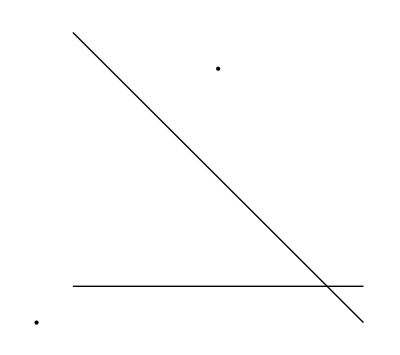

```mathematica
Graphics[{Point[{-5,-5}],Point[{0,2}],Line[{{-4,-4},{4,-4}}],Line[{{-4,3},{4,-5}}]}]
```

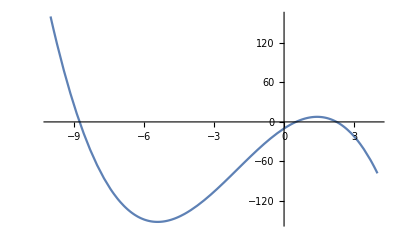

```mathematica
Plot[{polyO6/.{p1-> -5,p2-> -5,q1-> 0,q2-> 2,cm-> 4,cn-> 1}},{t,-10,4}]
```

```mathematica
polyO6/.{p1-> -5,p2-> -5,q1-> 0,q2-> 2,cm-> 4,cn-> 1}
```

-10+23 t-6 t^2-t^3

```mathematica
Solve[-10+23 t-6 t^2-t^3== 0,t,Reals]
```

{{t→Root[10-23 #1+6 #1^2+#1^3&,1]},{t→Root[10-23 #1+6 #1^2+#1^3&,2]},{t→Root[10-23 #1+6 #1^2+#1^3&,3]}}

StationaryPoint

```mathematica
D[-10+23 t-6 t^2-t^3,t]
```

23-12 t-3 t^2

```mathematica
Solve[23-12 t-3 t^2== 0,t]//N
```

{{t→-5.41565},{t→1.41565}}

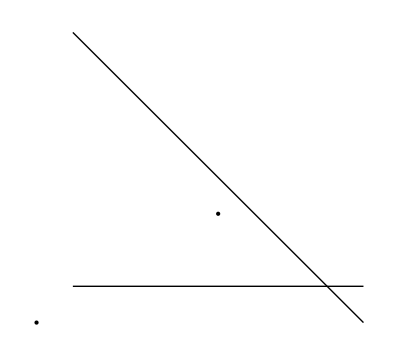

```mathematica
Graphics[{Point[{-5,-5}],Point[{0,-2}],Line[{{-4,-4},{4,-4}}],Line[{{-4,3},{4,-5}}]}]
```

```mathematica
polyO6/.{p1-> -5,p2-> -5,q1-> 0,q2-> -2,cm-> 4,cn-> 1}
```

-6+15 t-10 t^2-t^3

```mathematica
Solve[-6+15 t-10 t^2-t^3== 0,t,Reals]
```

{{t→Root[6-15 #1+10 #1^2+#1^3&,1]}}

StationaryPoint

```mathematica
D[-6+15 t-10 t^2-t^3,t]
```

15-20 t-3 t^2

```mathematica
Solve[15-20 t-3 t^2== 0,t]//N
```

{{t→-7.3472},{t→0.680532}}

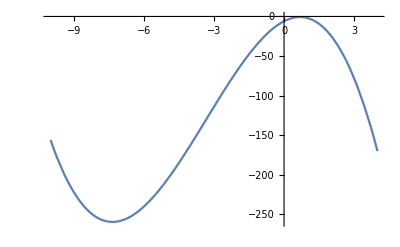

```mathematica
Plot[{polyO6/.{p1-> -5,p2-> -5,q1-> 0,q2-> -2,cm-> 4,cn-> 1}},{t,-10,4}]
```

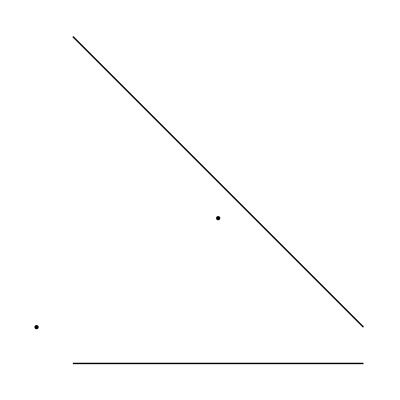

```mathematica
Graphics[{Point[{-5,-5}],Point[{0,-2}],Line[{{-4,-6},{4,-6}}],Line[{{-4,3},{4,-5}}]}]
```

```mathematica
polyO6/.{p1-> -5,p2-> -5,q1-> 0,q2-> -2,cm-> 6,cn-> 1}
```

-8+17 t-12 t^2+t^3

```mathematica
Solve[-8+17 t-12 t^2+t^3== 0,t,Reals]
```

{{t→Root[-8+17 #1-12 #1^2+#1^3&,1]}}

```mathematica
Discriminant[gbx1,t]//FullSimplify
```

{-4 (cm+p2)^4 (cn+q1+q2)^4 (4 cm^4+cn^4-4 p1^4-4 p1^2 p2^2+20 p1^3 q1+16 p1^2 p2 q1+12 p1 p2^2 q1+16 p2^3 q1-25 p1^2 q1^2-30 p1 p2 q1^2+3 p2^2 q1^2+12 p1 q1^3+12 p2 q1^3-2 q1^4-2 (2 p1^3-8 p2^3+9 p2^2 q1-12 p2 q1^2-2 q1^3-3 p1^2 (4 p2+3 q1)+2 p1 (p2^2+14 p2 q1+4 q1^2)) q2+(-9 p1^2-37 p2^2+4 p2 q1-4 q1^2+6 p1 (p2+2 q1)) q2^2+4 (-2 p1+6 p2+q1) q2^3-2 q2^4+8 cm^3 (-cn+p1-2 q1+q2)+2 cn^3 (3 p1-p2-q1+q2)+4 cm^2 (2 cn^2-3 cn p1-5 cn p2-p2^2+7 cn q1-3 p1 q1-5 p2 q1+5 q1^2+3 (cn+p1-p2) q2+6 q2^2)+cn^2 (11 p1^2+11 p2^2-8 p2 (q1+q2)-(q1+q2)^2+2 p1 (p2-2 q1+4 q2))+4 cm (-cn^3-2 p1^3+6 p1^2 q1+3 q1 (p2+q1)^2-(p2^2+5 p2 q1-5 q1^2) q2+3 (-p2+q1) q2^2+5 q2^3-cn^2 (2 p1-5 p2+q1+4 q2)-p1 (2 p2^2+p2 q1+8 q1^2-3 p2 q2+9 q1 q2+3 q2^2)+cn (p2^2+11 p2 q1+q1^2-2 p2 q2+q1 q2-p1 (p2+4 q1+9 q2)))+2 cn (2 p1^3+p1^2 (8 p2+5 q1+3 q2)+p1 (2 p2^2-7 q1^2+2 q1 q2-3 q2^2-2 p2 (7 q1+2 q2))+(p2+q1-q2) (8 p2^2+p2 (q1-3 q2)+2 (q1^2+q2^2))))}

```mathematica
m
```

OLine[0,1,cm]

```mathematica
n
```

OLine[1,1,cn]

```mathematica
c1=(x-(p1+q1)/2)^2+(y-(p2+q2)/2)^2-((p1-(p1+q1)/2)^2+(p2-(p2+q2)/2)^2)
```

-(p1+1/2 (-p1-q1))^2-(p2+1/2 (-p2-q2))^2+(1/2 (-p1-q1)+x)^2+(1/2 (-p2-q2)+y)^2

```mathematica
meq=y+cm
```

cm+y

```mathematica
neq=x+y+cn
```

cn+x+y

```mathematica
cst6=c1/.{x-> u1,y-> u2}
```

-(p1+1/2 (-p1-q1))^2-(p2+1/2 (-p2-q2))^2+(1/2 (-p1-q1)+u1)^2+(1/2 (-p2-q2)+u2)^2

```mathematica
cst7=c1/.{x-> v1,y->v2}
```

-(p1+1/2 (-p1-q1))^2-(p2+1/2 (-p2-q2))^2+(1/2 (-p1-q1)+v1)^2+(1/2 (-p2-q2)+v2)^2

```mathematica
cst8=meq/.{x-> u1,y-> u2}
```

cm+u2

```mathematica
cst9=neq/.{x-> v1, y-> v2}
```

cn+v1+v2

```mathematica
Union[Solve[{cst6== 0,cst7== 0,cst8== 0,cst9== 0},{u1,u2,v1,v2}]//Flatten]
```

{u1→1/2 (p1+q1-√(-4 cm^2+p1^2-4 cm p2-2 p1 q1+q1^2-4 cm q2-4 p2 q2)),u1→1/2 (p1+q1+√(-4 cm^2+p1^2-4 cm p2-2 p1 q1+q1^2-4 cm q2-4 p2 q2)),u2→-cm,v1→1/4 (-2 cn+p1-p2+q1-q2-√((2 cn-p1+p2-q1+q2)^2-8 (cn^2+cn p2+p1 q1+cn q2+p2 q2))),v1→1/4 (-2 cn+p1-p2+q1-q2+√((2 cn-p1+p2-q1+q2)^2-8 (cn^2+cn p2+p1 q1+cn q2+p2 q2))),v2→-cn/2-p1/4+p2/4-q1/4+q2/4-1/4 √((2 cn-p1+p2-q1+q2)^2-8 (cn^2+cn p2+p1 q1+cn q2+p2 q2)),v2→-cn/2-p1/4+p2/4-q1/4+q2/4+1/4 √((2 cn-p1+p2-q1+q2)^2-8 (cn^2+cn p2+p1 q1+cn q2+p2 q2))}

```mathematica
GroebnerBasis[{cst6== 0,cst7== 0,cst8== 0,cst9== 0},{u1,u2,v1,v2}]
```

{cn^2+cn p1+cn q1+p1 q1+p2 q2+2 cn v2+p1 v2-p2 v2+q1 v2-q2 v2+2 v2^2,cn+v1+v2,cm+u2,cm^2+cm p2+p1 q1+cm q2+p2 q2-p1 u1-q1 u1+u1^2}

```mathematica
Union[Solve[{cst6== 0,cst7== 0,cst8== 0,cst9== 0}/.{p1-> -5,p2-> -5,q1-> 0,q2-> -2,cm-> 6,cn-> 1},{u1,u2,v1,v2}]//Flatten]
```

{u1→-4,u1→-1,u2→-6,v1→-ⅈ √2,v1→ⅈ √2,v2→-1-ⅈ √2,v2→-1+ⅈ √2}

```mathematica
-4 cm^2+p1^2-4 cm p2-2 p1 q1+q1^2-4 cm q2-4 p2 q2
```

### Case 1: m and n are not parallel (similar parabolas?)

All parabola are similar.

```mathematica
P=OPoint[p1,p2];Q=OPoint[q1,q2];
```

```mathematica
m=OLine[0,1,cm];n=OLine[1,0,cn];
```

```mathematica
parabolaeq1=ODistance[OPoint[x,y],P]^2-ODistanceSq[OPoint[x,y],m]
```

(-p1+x)^2-(cm+y)^2+(-p2+y)^2

```mathematica
parabolaeq2=ODistance[OPoint[x,y],Q]^2-ODistanceSq[OPoint[x,y],n]
```

-(cn+x)^2+(-q1+x)^2+(-q2+y)^2

```mathematica
tgparabola1=(D[parabolaeq1,x]/.{x-> x1, y-> y1})+ (D[parabolaeq1,y]/.{x-> x1, y-> y1})t
```

2 (-p1+x1)+t (-2 (cm+y1)+2 (-p2+y1))

```mathematica
tgparabola2=(D[parabolaeq2,x]/.{x-> x2, y-> y2})+ (D[parabolaeq2,y]/.{x-> x2, y-> y2})t
```

-2 (cn+x2)+2 (-q1+x2)+2 t (-q2+y2)

```mathematica
cst1=tgparabola1/.{x-> x2,y-> y2}
```

2 (-p1+x1)+t (-2 (cm+y1)+2 (-p2+y1))

```mathematica
cst2=tgparabola2/.{x-> x1,y-> y1}
```

-2 (cn+x2)+2 (-q1+x2)+2 t (-q2+y2)

```mathematica
cst3=parabolaeq1/.{x-> x1,y-> y1}
```

(-p1+x1)^2-(cm+y1)^2+(-p2+y1)^2

```mathematica
cst4=parabolaeq2/.{x-> x2,y-> y2}
```

-(cn+x2)^2+(-q1+x2)^2+(-q2+y2)^2

```mathematica
cst5=(y1-y2)-t(x1-x2)
```

-t (x1-x2)+y1-y2

```mathematica
gbx1=GroebnerBasis[{cst1==0,cst2==0,cst3== 0,cst4== 0,cst5== 0(*η1 (cn+q2)-1== 0,η2(cm+p2)-1== 0*)},{t},{x1,x2,y1,y2(*,η1,η2*)}]//FullSimplify
```

{(cm+p2) (cn+q1) (cn+q1+(cm-p2+2 q2) t+(cn+2 p1-q1) t^2+(cm+p2) t^3)}

```mathematica
Exponent[gbx1,t]
```

{3}

```mathematica
(cn+p2+q1-q2+t (-p2+2 (q1+q2)+2 p1 (-1+t)+cn t+(-q1+q2+p2 (-1+t)) t)+cm (-1+t) (1+t^2))//Expand
```

-cm+cn+p2+q1-q2+cm t-2 p1 t-p2 t+2 q1 t+2 q2 t-cm t^2+cn t^2+2 p1 t^2-p2 t^2-q1 t^2+q2 t^2+cm t^3+p2 t^3

```mathematica
Reduce[-cm+cn+p2+q1-q2+cm t-2 p1 t-p2 t+2 q1 t+2 q2 t-cm t^2+cn t^2+2 p1 t^2-p2 t^2-q1 t^2+q2 t^2+cm t^3+p2 t^3== 0,t,Reals]
```

$Aborted

```mathematica
polyO6=-cm+cn+p2+q1-q2+cm t-2 p1 t-p2 t+2 q1 t+2 q2 t-cm t^2+cn t^2+2 p1 t^2-p2 t^2-q1 t^2+q2 t^2+cm t^3+p2 t^3
```

-cm+cn+p2+q1-q2+cm t-2 p1 t-p2 t+2 q1 t+2 q2 t-cm t^2+cn t^2+2 p1 t^2-p2 t^2-q1 t^2+q2 t^2+cm t^3+p2 t^3

```mathematica
m
```

OLine[0,1,cm]

```mathematica
n
```

OLine[1,1,cn]

```mathematica
Graphics[{Point[{-5,-5}],Point[{0,2}],Line[{{-4,-4},{4,-4}}],Line[{{-4,3},{4,-5}}]}]
```

-Graphics-

```mathematica
Plot[{polyO6/.{p1-> -5,p2-> -5,q1-> 0,q2-> 2,cm-> 4,cn-> 1}},{t,-10,4}]
```

-Graphics-

```mathematica
polyO6/.{p1-> -5,p2-> -5,q1-> 0,q2-> 2,cm-> 4,cn-> 1}
```

-10+23 t-6 t^2-t^3

```mathematica
Solve[-10+23 t-6 t^2-t^3== 0,t,Reals]
```

{{t→Root[10-23 #1+6 #1^2+#1^3&,1]},{t→Root[10-23 #1+6 #1^2+#1^3&,2]},{t→Root[10-23 #1+6 #1^2+#1^3&,3]}}

StationaryPoint

```mathematica
D[-10+23 t-6 t^2-t^3,t]
```

23-12 t-3 t^2

```mathematica
Solve[23-12 t-3 t^2== 0,t]//N
```

{{t→-5.41565},{t→1.41565}}

```mathematica
Graphics[{Point[{-5,-5}],Point[{0,-2}],Line[{{-4,-4},{4,-4}}],Line[{{-4,3},{4,-5}}]}]
```

-Graphics-

```mathematica
polyO6/.{p1-> -5,p2-> -5,q1-> 0,q2-> -2,cm-> 4,cn-> 1}
```

-6+15 t-10 t^2-t^3

```mathematica
Solve[-6+15 t-10 t^2-t^3== 0,t,Reals]
```

{{t→Root[6-15 #1+10 #1^2+#1^3&,1]}}

StationaryPoint

```mathematica
D[-6+15 t-10 t^2-t^3,t]
```

15-20 t-3 t^2

```mathematica
Solve[15-20 t-3 t^2== 0,t]//N
```

{{t→-7.3472},{t→0.680532}}

```mathematica
Plot[{polyO6/.{p1-> -5,p2-> -5,q1-> 0,q2-> -2,cm-> 4,cn-> 1}},{t,-10,4}]
```

-Graphics-

```mathematica
Graphics[{Point[{-5,-5}],Point[{0,-2}],Line[{{-4,-6},{4,-6}}],Line[{{-4,3},{4,-5}}]}]
```

-Graphics-

```mathematica
polyO6/.{p1-> -5,p2-> -5,q1-> 0,q2-> -2,cm-> 6,cn-> 1}
```

-8+17 t-12 t^2+t^3

```mathematica
Solve[-8+17 t-12 t^2+t^3== 0,t,Reals]
```

{{t→Root[-8+17 #1-12 #1^2+#1^3&,1]}}

```mathematica
Discriminant[gbx1,t]//FullSimplify
```

{-4 (cm+p2)^4 (cn+q1+q2)^4 (4 cm^4+cn^4-4 p1^4-4 p1^2 p2^2+20 p1^3 q1+16 p1^2 p2 q1+12 p1 p2^2 q1+16 p2^3 q1-25 p1^2 q1^2-30 p1 p2 q1^2+3 p2^2 q1^2+12 p1 q1^3+12 p2 q1^3-2 q1^4-2 (2 p1^3-8 p2^3+9 p2^2 q1-12 p2 q1^2-2 q1^3-3 p1^2 (4 p2+3 q1)+2 p1 (p2^2+14 p2 q1+4 q1^2)) q2+(-9 p1^2-37 p2^2+4 p2 q1-4 q1^2+6 p1 (p2+2 q1)) q2^2+4 (-2 p1+6 p2+q1) q2^3-2 q2^4+8 cm^3 (-cn+p1-2 q1+q2)+2 cn^3 (3 p1-p2-q1+q2)+4 cm^2 (2 cn^2-3 cn p1-5 cn p2-p2^2+7 cn q1-3 p1 q1-5 p2 q1+5 q1^2+3 (cn+p1-p2) q2+6 q2^2)+cn^2 (11 p1^2+11 p2^2-8 p2 (q1+q2)-(q1+q2)^2+2 p1 (p2-2 q1+4 q2))+4 cm (-cn^3-2 p1^3+6 p1^2 q1+3 q1 (p2+q1)^2-(p2^2+5 p2 q1-5 q1^2) q2+3 (-p2+q1) q2^2+5 q2^3-cn^2 (2 p1-5 p2+q1+4 q2)-p1 (2 p2^2+p2 q1+8 q1^2-3 p2 q2+9 q1 q2+3 q2^2)+cn (p2^2+11 p2 q1+q1^2-2 p2 q2+q1 q2-p1 (p2+4 q1+9 q2)))+2 cn (2 p1^3+p1^2 (8 p2+5 q1+3 q2)+p1 (2 p2^2-7 q1^2+2 q1 q2-3 q2^2-2 p2 (7 q1+2 q2))+(p2+q1-q2) (8 p2^2+p2 (q1-3 q2)+2 (q1^2+q2^2))))}

```mathematica
m
```

OLine[0,1,cm]

```mathematica
n
```

OLine[1,1,cn]

```mathematica
c1=(x-(p1+q1)/2)^2+(y-(p2+q2)/2)^2-((p1-(p1+q1)/2)^2+(p2-(p2+q2)/2)^2)
```

-(p1+1/2 (-p1-q1))^2-(p2+1/2 (-p2-q2))^2+(1/2 (-p1-q1)+x)^2+(1/2 (-p2-q2)+y)^2

```mathematica
meq=y+cm
```

cm+y

```mathematica
neq=x+y+cn
```

cn+x+y

```mathematica
cst6=c1/.{x-> u1,y-> u2}
```

-(p1+1/2 (-p1-q1))^2-(p2+1/2 (-p2-q2))^2+(1/2 (-p1-q1)+u1)^2+(1/2 (-p2-q2)+u2)^2

```mathematica
cst7=c1/.{x-> v1,y->v2}
```

-(p1+1/2 (-p1-q1))^2-(p2+1/2 (-p2-q2))^2+(1/2 (-p1-q1)+v1)^2+(1/2 (-p2-q2)+v2)^2

```mathematica
cst8=meq/.{x-> u1,y-> u2}
```

cm+u2

```mathematica
cst9=neq/.{x-> v1, y-> v2}
```

cn+v1+v2

```mathematica
Union[Solve[{cst6== 0,cst7== 0,cst8== 0,cst9== 0},{u1,u2,v1,v2}]//Flatten]
```

{u1→1/2 (p1+q1-√(-4 cm^2+p1^2-4 cm p2-2 p1 q1+q1^2-4 cm q2-4 p2 q2)),u1→1/2 (p1+q1+√(-4 cm^2+p1^2-4 cm p2-2 p1 q1+q1^2-4 cm q2-4 p2 q2)),u2→-cm,v1→1/4 (-2 cn+p1-p2+q1-q2-√((2 cn-p1+p2-q1+q2)^2-8 (cn^2+cn p2+p1 q1+cn q2+p2 q2))),v1→1/4 (-2 cn+p1-p2+q1-q2+√((2 cn-p1+p2-q1+q2)^2-8 (cn^2+cn p2+p1 q1+cn q2+p2 q2))),v2→-cn/2-p1/4+p2/4-q1/4+q2/4-1/4 √((2 cn-p1+p2-q1+q2)^2-8 (cn^2+cn p2+p1 q1+cn q2+p2 q2)),v2→-cn/2-p1/4+p2/4-q1/4+q2/4+1/4 √((2 cn-p1+p2-q1+q2)^2-8 (cn^2+cn p2+p1 q1+cn q2+p2 q2))}

```mathematica
GroebnerBasis[{cst6== 0,cst7== 0,cst8== 0,cst9== 0},{u1,u2,v1,v2}]
```

{cn^2+cn p1+cn q1+p1 q1+p2 q2+2 cn v2+p1 v2-p2 v2+q1 v2-q2 v2+2 v2^2,cn+v1+v2,cm+u2,cm^2+cm p2+p1 q1+cm q2+p2 q2-p1 u1-q1 u1+u1^2}

```mathematica
Union[Solve[{cst6== 0,cst7== 0,cst8== 0,cst9== 0}/.{p1-> -5,p2-> -5,q1-> 0,q2-> -2,cm-> 6,cn-> 1},{u1,u2,v1,v2}]//Flatten]
```

{u1→-4,u1→-1,u2→-6,v1→-ⅈ √2,v1→ⅈ √2,v2→-1-ⅈ √2,v2→-1+ⅈ √2}

```mathematica
-4 cm^2+p1^2-4 cm p2-2 p1 q1+q1^2-4 cm q2-4 p2 q2
```

### Case 1: m and n are not parallel (tracing)

All parabola are similar.

```mathematica
P=OPoint[p1,p2];Q=OPoint[q1,q2];
```

```mathematica
m=OLine[0,1,cm];n=OLine[1,0,cn];
```

```mathematica
parabolaeq1=ODistance[OPoint[x,y],P]^2-ODistanceSq[OPoint[x,y],m]
```

(-p1+x)^2-(cm+y)^2+(-p2+y)^2

```mathematica
parabolaeq2=ODistance[OPoint[x,y],Q]^2-ODistanceSq[OPoint[x,y],n]
```

-(cn+x)^2+(-q1+x)^2+(-q2+y)^2

```mathematica
tgparabola1=(D[parabolaeq1,x]/.{x-> x1, y-> y1})+ (D[parabolaeq1,y]/.{x-> x1, y-> y1})t
```

2 (-p1+x1)+t (-2 (cm+y1)+2 (-p2+y1))

```mathematica
tgparabola2=(D[parabolaeq2,x]/.{x-> x2, y-> y2})+ (D[parabolaeq2,y]/.{x-> x2, y-> y2})t
```

-2 (cn+x2)+2 (-q1+x2)+2 t (-q2+y2)

```mathematica
cst1=tgparabola1/.{x-> x2,y-> y2}
```

2 (-p1+x1)+t (-2 (cm+y1)+2 (-p2+y1))

```mathematica
cst2=tgparabola2/.{x-> x1,y-> y1}
```

-2 (cn+x2)+2 (-q1+x2)+2 t (-q2+y2)

```mathematica
cst3=parabolaeq1/.{x-> x1,y-> y1}
```

(-p1+x1)^2-(cm+y1)^2+(-p2+y1)^2

```mathematica
cst4=parabolaeq2/.{x-> x2,y-> y2}
```

-(cn+x2)^2+(-q1+x2)^2+(-q2+y2)^2

```mathematica
cst5=(y1-y2)-t(x1-x2)
```

-t (x1-x2)+y1-y2

```mathematica
gbx1=GroebnerBasis[{cst1==0,cst2==0,cst3== 0,cst4== 0,cst5== 0(*η1 (cn+q2)-1== 0,η2(cm+p2)-1== 0*)},{t},{x1,x2,y1,y2(*,η1,η2*)}]//FullSimplify
```

{(cm+p2) (cn+q1) (cn+q1+(cm-p2+2 q2) t+(cn+2 p1-q1) t^2+(cm+p2) t^3)}

```mathematica
factor=(cn+q1+(cm-p2+2 q2) t+(cn+2 p1-q1) t^2+(cm+p2) t^3)
```

cn+q1+(cm-p2+2 q2) t+(cn+2 p1-q1) t^2+(cm+p2) t^3

```mathematica
poly=Collect[factor,{t,t^2,t^3}]
```

cn+q1+(cm-p2+2 q2) t+(cn+2 p1-q1) t^2+(cm+p2) t^3

```mathematica
Resultant
```

```mathematica
Discriminant[poly,t]
```

-4 (cm^4+2 cm^2 cn^2+cn^4-10 cm^2 cn p1+6 cn^3 p1-cm^2 p1^2+12 cn^2 p1^2+8 cn p1^3-2 cm^3 p2+14 cm cn^2 p2+2 cm cn p1 p2+2 cm p1^2 p2+11 cn^2 p2^2+8 cn p1 p2^2-p1^2 p2^2+2 cm p2^3-p2^4+14 cm^2 cn q1-2 cn^3 q1-8 cm^2 p1 q1-6 cn^2 p1 q1+8 p1^3 q1+26 cm cn p2 q1-2 cm p1 p2 q1+14 cn p2^2 q1+10 p1 p2^2 q1+11 cm^2 q1^2-6 cn p1 q1^2-12 p1^2 q1^2+14 cm p2 q1^2+2 p2^2 q1^2+2 cn q1^3+6 p1 q1^3-q1^4+6 cm^3 q2-10 cm cn^2 q2-22 cm cn p1 q2-4 cm p1^2 q2-6 cm^2 p2 q2-8 cn^2 p2 q2-14 cn p1 p2 q2+4 p1^2 p2 q2-6 cm p2^2 q2+6 p2^3 q2+2 cm cn q1 q2-14 cm p1 q1 q2-2 cn p2 q1 q2-22 p1 p2 q1 q2+8 cm q1^2 q2+10 p2 q1^2 q2+12 cm^2 q2^2-cn^2 q2^2-4 cn p1 q2^2-4 p1^2 q2^2-12 p2^2 q2^2+2 cn q1 q2^2+4 p1 q1 q2^2-q1^2 q2^2+8 cm q2^3+8 p2 q2^3)

```mathematica
d=-(cm^4+2 cm^2 cn^2+cn^4-10 cm^2 cn p1+6 cn^3 p1-cm^2 p1^2+12 cn^2 p1^2+8 cn p1^3-2 cm^3 p2+14 cm cn^2 p2+2 cm cn p1 p2+2 cm p1^2 p2+11 cn^2 p2^2+8 cn p1 p2^2-p1^2 p2^2+2 cm p2^3-p2^4+14 cm^2 cn q1-2 cn^3 q1-8 cm^2 p1 q1-6 cn^2 p1 q1+8 p1^3 q1+26 cm cn p2 q1-2 cm p1 p2 q1+14 cn p2^2 q1+10 p1 p2^2 q1+11 cm^2 q1^2-6 cn p1 q1^2-12 p1^2 q1^2+14 cm p2 q1^2+2 p2^2 q1^2+2 cn q1^3+6 p1 q1^3-q1^4+6 cm^3 q2-10 cm cn^2 q2-22 cm cn p1 q2-4 cm p1^2 q2-6 cm^2 p2 q2-8 cn^2 p2 q2-14 cn p1 p2 q2+4 p1^2 p2 q2-6 cm p2^2 q2+6 p2^3 q2+2 cm cn q1 q2-14 cm p1 q1 q2-2 cn p2 q1 q2-22 p1 p2 q1 q2+8 cm q1^2 q2+10 p2 q1^2 q2+12 cm^2 q2^2-cn^2 q2^2-4 cn p1 q2^2-4 p1^2 q2^2-12 p2^2 q2^2+2 cn q1 q2^2+4 p1 q1 q2^2-q1^2 q2^2+8 cm q2^3+8 p2 q2^3)/.{p1-> 4,p2-> 4,cm-> 0,cn-> 0}
```

512-1152 q1+160 q1^2-24 q1^3+q1^4-640 q2+352 q1 q2-40 q1^2 q2+256 q2^2-16 q1 q2^2+q1^2 q2^2-32 q2^3

```mathematica
Solve[d== 0,{q2},Reals]
```

{{q2→ConditionalExpression[Root[-512+1152 q1-160 q1^2+24 q1^3-q1^4+(640-352 q1+40 q1^2) #1+(-256+16 q1-q1^2) #1^2+32 #1^3&,1],0<q1<4 (2-3/(-1+√2)^(1/3)+3 (-1+√2)^(1/3))||q1>4 (2-3/(-1+√2)^(1/3)+3 (-1+√2)^(1/3))||q1<0]},{q2→ConditionalExpression[Root[-512+1152 q1-160 q1^2+24 q1^3-q1^4+(640-352 q1+40 q1^2) #1+(-256+16 q1-q1^2) #1^2+32 #1^3&,2],0<q1<4 (2-3/(-1+√2)^(1/3)+3 (-1+√2)^(1/3))]},{q2→ConditionalExpression[Root[-512+1152 q1-160 q1^2+24 q1^3-q1^4+(640-352 q1+40 q1^2) #1+(-256+16 q1-q1^2) #1^2+32 #1^3&,3],0<q1<4 (2-3/(-1+√2)^(1/3)+3 (-1+√2)^(1/3))]}}

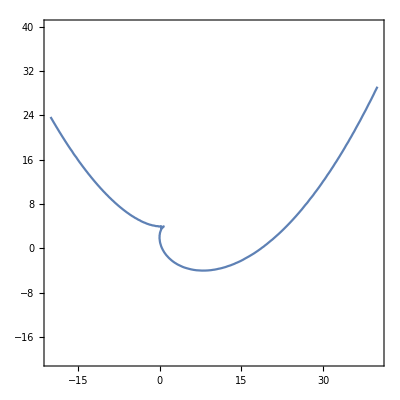

```mathematica
ContourPlot[d==0,{q1,-20,40},{q2,-20,40}]
```

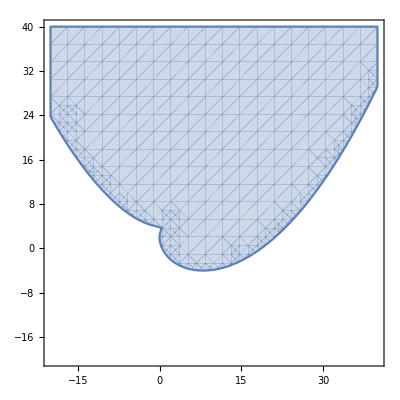

```mathematica
RegionPlot[d< 0,{q1,-20,40},{q2,-20,40}]
```

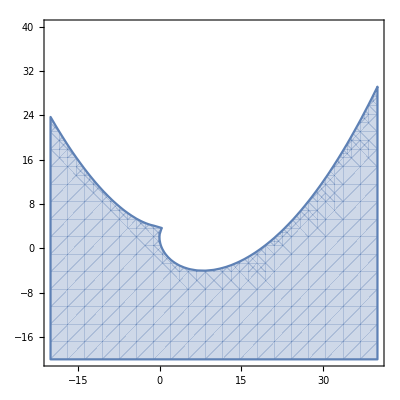

```mathematica
RegionPlot[d> 0,{q1,-20,40},{q2,-20,40}]
```

### Case 1: m and n are not parallel (lines m and n are perpendicular)

All parabola are similar.

```mathematica
P=OPoint[p1,p2];Q=OPoint[q1,q2];
```

```mathematica
m=OLine[0,1,cm];n=OLine[1,0,cn];
```

```mathematica
parabolaeq1=ODistance[OPoint[x,y],P]^2-ODistanceSq[OPoint[x,y],m]
```

(-p1+x)^2-(cm+y)^2+(-p2+y)^2

```mathematica
parabolaeq2=ODistance[OPoint[x,y],Q]^2-ODistanceSq[OPoint[x,y],n]
```

-(cn+x)^2+(-q1+x)^2+(-q2+y)^2

```mathematica
tgparabola1=(D[parabolaeq1,x]/.{x-> x1, y-> y1})+ (D[parabolaeq1,y]/.{x-> x1, y-> y1})t
```

2 (-p1+x1)+t (-2 (cm+y1)+2 (-p2+y1))

```mathematica
tgparabola2=(D[parabolaeq2,x]/.{x-> x2, y-> y2})+ (D[parabolaeq2,y]/.{x-> x2, y-> y2})t
```

-2 (cn+x2)+2 (-q1+x2)+2 t (-q2+y2)

```mathematica
cst1=tgparabola1/.{x-> x2,y-> y2}
```

2 (-p1+x1)+t (-2 (cm+y1)+2 (-p2+y1))

```mathematica
cst2=tgparabola2/.{x-> x1,y-> y1}
```

-2 (cn+x2)+2 (-q1+x2)+2 t (-q2+y2)

```mathematica
cst3=parabolaeq1/.{x-> x1,y-> y1}
```

(-p1+x1)^2-(cm+y1)^2+(-p2+y1)^2

```mathematica
cst4=parabolaeq2/.{x-> x2,y-> y2}
```

-(cn+x2)^2+(-q1+x2)^2+(-q2+y2)^2

```mathematica
cst5=(y1-y2)-t(x1-x2)
```

-t (x1-x2)+y1-y2

```mathematica
gbx1=GroebnerBasis[{cst1==0,cst2==0,cst3== 0,cst4== 0,cst5== 0,η1 (cn+q1)-1== 0,η2(cm+p2)-1== 0},{t},{x1,x2,y1,y2,η1,η2}]//FullSimplify
```

{cn+q1+(cm-p2+2 q2) t+(cn+2 p1-q1) t^2+(cm+p2) t^3}

```mathematica
(* Discriminant[a x^3+b x^2+c x+ e,x]*)
```

```mathematica
(* b^2 c^2-4 a c^3-4 b^3 e+18 a b c e-27 a^2 e^2*)
```

```mathematica
d=Discriminant[gbx1[[1]]/.{p1-> 4,p2-> 4,cm-> 0,cn-> 0},t]
```

4 (512-1152 q1+160 q1^2-24 q1^3+q1^4-640 q2+352 q1 q2-40 q1^2 q2+256 q2^2-16 q1 q2^2+q1^2 q2^2-32 q2^3)

```mathematica
Solve[d== 0,{q2},Reals]
```

{{q2→ConditionalExpression[Root[-512+1152 q1-160 q1^2+24 q1^3-q1^4+(640-352 q1+40 q1^2) #1+(-256+16 q1-q1^2) #1^2+32 #1^3&,1],0<q1<4 (2-3/(-1+√2)^(1/3)+3 (-1+√2)^(1/3))||q1>4 (2-3/(-1+√2)^(1/3)+3 (-1+√2)^(1/3))||q1<0]},{q2→ConditionalExpression[Root[-512+1152 q1-160 q1^2+24 q1^3-q1^4+(640-352 q1+40 q1^2) #1+(-256+16 q1-q1^2) #1^2+32 #1^3&,2],0<q1<4 (2-3/(-1+√2)^(1/3)+3 (-1+√2)^(1/3))]},{q2→ConditionalExpression[Root[-512+1152 q1-160 q1^2+24 q1^3-q1^4+(640-352 q1+40 q1^2) #1+(-256+16 q1-q1^2) #1^2+32 #1^3&,3],0<q1<4 (2-3/(-1+√2)^(1/3)+3 (-1+√2)^(1/3))]}}

```mathematica
ContourPlot[d==0,{q1,-20,40},{q2,-20,40}]
```

-Graphics-

```mathematica
RegionPlot[d< 0,{q1,-20,40},{q2,-20,40}]
```

-Graphics-

```mathematica
RegionPlot[d> 0,{q1,-20,40},{q2,-20,40}]
```

-Graphics-

### Case 1: m and n are not parallel (lines m and n are not perpendicular)

All parabola are similar.

```mathematica
P=OPoint[p1,p2];Q=OPoint[q1,q2];
```

```mathematica
m=OLine[0,1,cm];n=OLine[an,bn,cn];
```

```mathematica
parabolaeq1=ODistance[OPoint[x,y],P]^2-ODistanceSq[OPoint[x,y],m]
```

(-p1+x)^2-(cm+y)^2+(-p2+y)^2

```mathematica
parabolaeq2=ODistance[OPoint[x,y],Q]^2-ODistanceSq[OPoint[x,y],n]
```

(-q1+x)^2+(-q2+y)^2-(cn+an x+bn y)^2/(an^2+bn^2)

```mathematica
parabolaeq2=(an^2+bn^2)((-q1+x)^2+(-q2+y)^2)-(cn+an x+bn y)^2
```

-(cn+an x+bn y)^2+(an^2+bn^2) ((-q1+x)^2+(-q2+y)^2)

```mathematica
tgparabola1=(D[parabolaeq1,x]/.{x-> x1, y-> y1})+ (D[parabolaeq1,y]/.{x-> x1, y-> y1})t
```

2 (-p1+x1)+t (-2 (cm+y1)+2 (-p2+y1))

```mathematica
tgparabola2=(D[parabolaeq2,x]/.{x-> x2, y-> y2})+ (D[parabolaeq2,y]/.{x-> x2, y-> y2})t
```

2 (an^2+bn^2) (-q1+x2)-2 an (cn+an x2+bn y2)+t (2 (an^2+bn^2) (-q2+y2)-2 bn (cn+an x2+bn y2))

```mathematica
cst1=tgparabola1/.{x-> x2,y-> y2}
```

2 (-p1+x1)+t (-2 (cm+y1)+2 (-p2+y1))

```mathematica
cst2=tgparabola2/.{x-> x1,y-> y1}
```

2 (an^2+bn^2) (-q1+x2)-2 an (cn+an x2+bn y2)+t (2 (an^2+bn^2) (-q2+y2)-2 bn (cn+an x2+bn y2))

```mathematica
cst3=parabolaeq1/.{x-> x1,y-> y1}
```

(-p1+x1)^2-(cm+y1)^2+(-p2+y1)^2

```mathematica
cst4=parabolaeq2/.{x-> x2,y-> y2}
```

-(cn+an x2+bn y2)^2+(an^2+bn^2) ((-q1+x2)^2+(-q2+y2)^2)

```mathematica
cst5=(y1-y2)-t(x1-x2)
```

-t (x1-x2)+y1-y2

```mathematica
LineCC[Line[an,bn,cn]]
```

(-1+bn) bn==0&&(-1+an) (-1+bn)==0

```mathematica
gbx1=GroebnerBasis[{cst1==0,cst2==0,cst3== 0,cst4== 0,cst5== 0,η1 (q1+q2+cn)-1== 0,η2(cm+p2)-1== 0,(-1+bn) bn==0,(-1+an) (-1+bn)==0},{t},{x1,x2,y1,y2,η1,η2}]//FullSimplify
```

{cn+p2+q1-q2+t (-p2+2 (q1+q2)+2 p1 (-1+t)+cn t+(-q1+q2+p2 (-1+t)) t)+cm (-1+t) (1+t^2)}

```mathematica
(* Discriminant[a x^3+b x^2+c x+ e,x]*)
```

```mathematica
(* b^2 c^2-4 a c^3-4 b^3 e+18 a b c e-27 a^2 e^2*)
```

```mathematica
d=Discriminant[gbx1[[1]]/.{p1-> 4,p2-> 4,cm-> 0,cn-> 0},t]
```

8 (1024-2048 q1+416 q1^2-48 q1^3+q1^4-1024 q2+448 q1 q2-16 q1^2 q2-2 q1^3 q2+320 q2^2-32 q1 q2^2+2 q1^2 q2^2-32 q2^3-2 q1 q2^3+q2^4)

```mathematica
Solve[d== 0,{q2},Reals]
```

{{q2→ConditionalExpression[Root[1024-2048 q1+416 q1^2-48 q1^3+q1^4+(-1024+448 q1-16 q1^2-2 q1^3) #1+(320-32 q1+2 q1^2) #1^2+(-32-2 q1) #1^3+#1^4&,1],0<q1<-1-21/(13+16 √2)^(1/3)+3 (13+16 √2)^(1/3)||q1>-1-21/(13+16 √2)^(1/3)+3 (13+16 √2)^(1/3)]},{q2→ConditionalExpression[Root[1024-2048 q1+416 q1^2-48 q1^3+q1^4+(-1024+448 q1-16 q1^2-2 q1^3) #1+(320-32 q1+2 q1^2) #1^2+(-32-2 q1) #1^3+#1^4&,2],0<q1<-1-21/(13+16 √2)^(1/3)+3 (13+16 √2)^(1/3)||q1>-1-21/(13+16 √2)^(1/3)+3 (13+16 √2)^(1/3)]},{q2→ConditionalExpression[Root[1024-2048 q1+416 q1^2-48 q1^3+q1^4+(-1024+448 q1-16 q1^2-2 q1^3) #1+(320-32 q1+2 q1^2) #1^2+(-32-2 q1) #1^3+#1^4&,3],0<q1<-1-21/(13+16 √2)^(1/3)+3 (13+16 √2)^(1/3)]},{q2→ConditionalExpression[Root[1024-2048 q1+416 q1^2-48 q1^3+q1^4+(-1024+448 q1-16 q1^2-2 q1^3) #1+(320-32 q1+2 q1^2) #1^2+(-32-2 q1) #1^3+#1^4&,4],0<q1<-1-21/(13+16 √2)^(1/3)+3 (13+16 √2)^(1/3)]}}

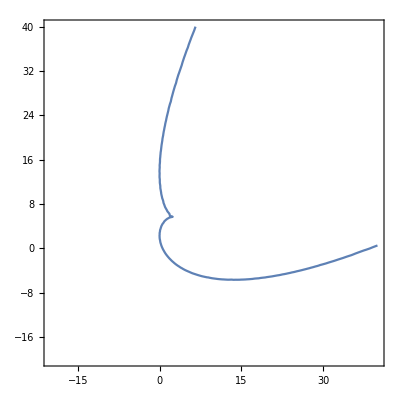

```mathematica
ContourPlot[d==0,{q1,-20,40},{q2,-20,40}]
```

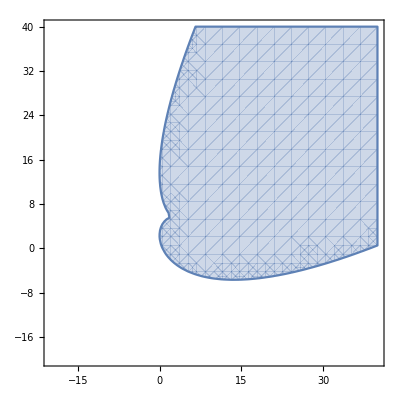

```mathematica
RegionPlot[d< 0,{q1,-20,40},{q2,-20,40}]
```

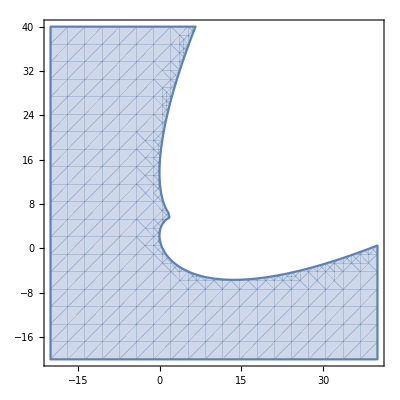

```mathematica
RegionPlot[d> 0,{q1,-20,40},{q2,-20,40}]
```

## (O6) Tests

```mathematica
P=OPoint[p1,p2];Q=OPoint[q1,q2];
```

```mathematica
m=OLine[0,1,cm];n=OLine[1,1,cn];
```

```mathematica
M=OPoint[(p1+q1)/2,(p2+q2)/2];
```

```mathematica
f[t_]:=-cm+cn+p2+q1-q2+cm t-2 p1 t-p2 t+2 q1 t+2 q2 t-cm t^2+cn t^2+2 p1 t^2-p2 t^2-q1 t^2+q2 t^2+cm t^3+p2 t^3
```

```mathematica
paramcubic=Collect[f[t],{t,t^2,t^3},Simplify]
```

-cm+cn+p2+q1-q2+(cm-2 p1-p2+2 q1+2 q2) t+(-cm+cn+2 p1-p2-q1+q2) t^2+(cm+p2) t^3

```mathematica
discrt=Discriminant[f[t],t]
```

-4 (4 cm^4-8 cm^3 cn+8 cm^2 cn^2-4 cm cn^3+cn^4+8 cm^3 p1-12 cm^2 cn p1-8 cm cn^2 p1+6 cn^3 p1+11 cn^2 p1^2-8 cm p1^3+4 cn p1^3-4 p1^4-20 cm^2 cn p2+20 cm cn^2 p2-2 cn^3 p2-4 cm cn p1 p2+2 cn^2 p1 p2+16 cn p1^2 p2-4 cm^2 p2^2+4 cm cn p2^2+11 cn^2 p2^2-8 cm p1 p2^2+4 cn p1 p2^2-4 p1^2 p2^2+16 cn p2^3-16 cm^3 q1+28 cm^2 cn q1-4 cm cn^2 q1-2 cn^3 q1-12 cm^2 p1 q1-16 cm cn p1 q1-4 cn^2 p1 q1+24 cm p1^2 q1+10 cn p1^2 q1+20 p1^3 q1-20 cm^2 p2 q1+44 cm cn p2 q1-8 cn^2 p2 q1-4 cm p1 p2 q1-28 cn p1 p2 q1+16 p1^2 p2 q1+12 cm p2^2 q1+18 cn p2^2 q1+12 p1 p2^2 q1+16 p2^3 q1+20 cm^2 q1^2+4 cm cn q1^2-cn^2 q1^2-32 cm p1 q1^2-14 cn p1 q1^2-25 p1^2 q1^2+24 cm p2 q1^2+6 cn p2 q1^2-30 p1 p2 q1^2+3 p2^2 q1^2+12 cm q1^3+4 cn q1^3+12 p1 q1^3+12 p2 q1^3-2 q1^4+8 cm^3 q2+12 cm^2 cn q2-16 cm cn^2 q2+2 cn^3 q2+12 cm^2 p1 q2-36 cm cn p1 q2+8 cn^2 p1 q2+6 cn p1^2 q2-4 p1^3 q2-12 cm^2 p2 q2-8 cm cn p2 q2-8 cn^2 p2 q2+12 cm p1 p2 q2-8 cn p1 p2 q2+24 p1^2 p2 q2-4 cm p2^2 q2-22 cn p2^2 q2-4 p1 p2^2 q2+16 p2^3 q2+4 cm cn q1 q2-2 cn^2 q1 q2-36 cm p1 q1 q2+4 cn p1 q1 q2+18 p1^2 q1 q2-20 cm p2 q1 q2-8 cn p2 q1 q2-56 p1 p2 q1 q2-18 p2^2 q1 q2+20 cm q1^2 q2-4 cn q1^2 q2-16 p1 q1^2 q2+24 p2 q1^2 q2+4 q1^3 q2+24 cm^2 q2^2-cn^2 q2^2-12 cm p1 q2^2-6 cn p1 q2^2-9 p1^2 q2^2-12 cm p2 q2^2+10 cn p2 q2^2+6 p1 p2 q2^2-37 p2^2 q2^2+12 cm q1 q2^2+4 cn q1 q2^2+12 p1 q1 q2^2+4 p2 q1 q2^2-4 q1^2 q2^2+20 cm q2^3-4 cn q2^3-8 p1 q2^3+24 p2 q2^3+4 q1 q2^3-2 q2^4)

```mathematica
d1=ODistanceSq[M,m]//Expand
```

cm^2+cm p2+p2^2/4+cm q2+(p2 q2)/2+q2^2/4

```mathematica
d2=ODistanceSq[M,n]//Expand
```

cn^2/2+(cn p1)/2+p1^2/8+(cn p2)/2+(p1 p2)/4+p2^2/8+(cn q1)/2+(p1 q1)/4+(p2 q1)/4+q1^2/8+(cn q2)/2+(p1 q2)/4+(p2 q2)/4+(q1 q2)/4+q2^2/8

```mathematica
d3=ODistanceSq[M,P]//Expand
```

p1^2/4+p2^2/4-(p1 q1)/2+q1^2/4-(p2 q2)/2+q2^2/4

```mathematica
d4=ODistanceSq[M,Q]//Expand
```

p1^2/4+p2^2/4-(p1 q1)/2+q1^2/4-(p2 q2)/2+q2^2/4

```mathematica
diff=32*(d1-d3)(d2-d4)//Expand
```

16 cm^2 cn^2+16 cm^2 cn p1-4 cm^2 p1^2-4 cn^2 p1^2-4 cn p1^3+p1^4+16 cm^2 cn p2+16 cm cn^2 p2+8 cm^2 p1 p2+16 cm cn p1 p2-4 cm p1^2 p2-4 cn p1^2 p2-2 p1^3 p2-4 cm^2 p2^2+16 cm cn p2^2+8 cm p1 p2^2+p1^2 p2^2-4 cm p2^3+16 cm^2 cn q1+24 cm^2 p1 q1+8 cn^2 p1 q1+4 cn p1^2 q1-8 p1^3 q1+8 cm^2 p2 q1+16 cm cn p2 q1+24 cm p1 p2 q1+8 cn p1 p2 q1+2 p1^2 p2 q1+8 cm p2^2 q1-2 p1 p2^2 q1-4 cm^2 q1^2-4 cn^2 q1^2+4 cn p1 q1^2+14 p1^2 q1^2-4 cm p2 q1^2-4 cn p2 q1^2+2 p1 p2 q1^2+p2^2 q1^2-4 cn q1^3-8 p1 q1^3-2 p2 q1^3+q1^4+16 cm^2 cn q2+16 cm cn^2 q2+8 cm^2 p1 q2+16 cm cn p1 q2-4 cm p1^2 q2-4 cn p1^2 q2-2 p1^3 q2+24 cm^2 p2 q2+32 cm cn p2 q2+16 cn^2 p2 q2+16 cm p1 p2 q2+16 cn p1 p2 q2-10 p1^2 p2 q2+20 cm p2^2 q2+16 cn p2^2 q2+8 p1 p2^2 q2-4 p2^3 q2+8 cm^2 q1 q2+16 cm cn q1 q2+24 cm p1 q1 q2+8 cn p1 q1 q2+2 p1^2 q1 q2+16 cm p2 q1 q2+16 cn p2 q1 q2+36 p1 p2 q1 q2+8 p2^2 q1 q2-4 cm q1^2 q2-4 cn q1^2 q2+2 p1 q1^2 q2-10 p2 q1^2 q2-2 q1^3 q2-4 cm^2 q2^2+16 cm cn q2^2+8 cm p1 q2^2+p1^2 q2^2+20 cm p2 q2^2+16 cn p2 q2^2+8 p1 p2 q2^2+24 p2^2 q2^2+8 cm q1 q2^2-2 p1 q1 q2^2+8 p2 q1 q2^2+q1^2 q2^2-4 cm q2^3-4 p2 q2^3

```mathematica
discrt2=4 cm^4-8 cm^3 cn+8 cm^2 cn^2-4 cm cn^3+cn^4+8 cm^3 p1-12 cm^2 cn p1-8 cm cn^2 p1+6 cn^3 p1+11 cn^2 p1^2-8 cm p1^3+4 cn p1^3-4 p1^4-20 cm^2 cn p2+20 cm cn^2 p2-2 cn^3 p2-4 cm cn p1 p2+2 cn^2 p1 p2+16 cn p1^2 p2-4 cm^2 p2^2+4 cm cn p2^2+11 cn^2 p2^2-8 cm p1 p2^2+4 cn p1 p2^2-4 p1^2 p2^2+16 cn p2^3-16 cm^3 q1+28 cm^2 cn q1-4 cm cn^2 q1-2 cn^3 q1-12 cm^2 p1 q1-16 cm cn p1 q1-4 cn^2 p1 q1+24 cm p1^2 q1+10 cn p1^2 q1+20 p1^3 q1-20 cm^2 p2 q1+44 cm cn p2 q1-8 cn^2 p2 q1-4 cm p1 p2 q1-28 cn p1 p2 q1+16 p1^2 p2 q1+12 cm p2^2 q1+18 cn p2^2 q1+12 p1 p2^2 q1+16 p2^3 q1+20 cm^2 q1^2+4 cm cn q1^2-cn^2 q1^2-32 cm p1 q1^2-14 cn p1 q1^2-25 p1^2 q1^2+24 cm p2 q1^2+6 cn p2 q1^2-30 p1 p2 q1^2+3 p2^2 q1^2+12 cm q1^3+4 cn q1^3+12 p1 q1^3+12 p2 q1^3-2 q1^4+8 cm^3 q2+12 cm^2 cn q2-16 cm cn^2 q2+2 cn^3 q2+12 cm^2 p1 q2-36 cm cn p1 q2+8 cn^2 p1 q2+6 cn p1^2 q2-4 p1^3 q2-12 cm^2 p2 q2-8 cm cn p2 q2-8 cn^2 p2 q2+12 cm p1 p2 q2-8 cn p1 p2 q2+24 p1^2 p2 q2-4 cm p2^2 q2-22 cn p2^2 q2-4 p1 p2^2 q2+16 p2^3 q2+4 cm cn q1 q2-2 cn^2 q1 q2-36 cm p1 q1 q2+4 cn p1 q1 q2+18 p1^2 q1 q2-20 cm p2 q1 q2-8 cn p2 q1 q2-56 p1 p2 q1 q2-18 p2^2 q1 q2+20 cm q1^2 q2-4 cn q1^2 q2-16 p1 q1^2 q2+24 p2 q1^2 q2+4 q1^3 q2+24 cm^2 q2^2-cn^2 q2^2-12 cm p1 q2^2-6 cn p1 q2^2-9 p1^2 q2^2-12 cm p2 q2^2+10 cn p2 q2^2+6 p1 p2 q2^2-37 p2^2 q2^2+12 cm q1 q2^2+4 cn q1 q2^2+12 p1 q1 q2^2+4 p2 q1 q2^2-4 q1^2 q2^2+20 cm q2^3-4 cn q2^3-8 p1 q2^3+24 p2 q2^3+4 q1 q2^3-2 q2^4//FullSimplify
```

4 cm^4+cn^4-4 p1^4-4 p1^2 p2^2+20 p1^3 q1+16 p1^2 p2 q1+12 p1 p2^2 q1+16 p2^3 q1-25 p1^2 q1^2-30 p1 p2 q1^2+3 p2^2 q1^2+12 p1 q1^3+12 p2 q1^3-2 q1^4-2 (2 p1^3-8 p2^3+9 p2^2 q1-12 p2 q1^2-2 q1^3-3 p1^2 (4 p2+3 q1)+2 p1 (p2^2+14 p2 q1+4 q1^2)) q2+(-9 p1^2-37 p2^2+4 p2 q1-4 q1^2+6 p1 (p2+2 q1)) q2^2+4 (-2 p1+6 p2+q1) q2^3-2 q2^4+8 cm^3 (-cn+p1-2 q1+q2)+2 cn^3 (3 p1-p2-q1+q2)+4 cm^2 (2 cn^2-3 cn p1-5 cn p2-p2^2+7 cn q1-3 p1 q1-5 p2 q1+5 q1^2+3 (cn+p1-p2) q2+6 q2^2)+cn^2 (11 p1^2+11 p2^2-8 p2 (q1+q2)-(q1+q2)^2+2 p1 (p2-2 q1+4 q2))+4 cm (-cn^3-2 p1^3+6 p1^2 q1+3 q1 (p2+q1)^2-(p2^2+5 p2 q1-5 q1^2) q2+3 (-p2+q1) q2^2+5 q2^3-cn^2 (2 p1-5 p2+q1+4 q2)-p1 (2 p2^2+p2 q1+8 q1^2-3 p2 q2+9 q1 q2+3 q2^2)+cn (p2^2+11 p2 q1+q1^2-2 p2 q2+q1 q2-p1 (p2+4 q1+9 q2)))+2 cn (2 p1^3+p1^2 (8 p2+5 q1+3 q2)+p1 (2 p2^2-7 q1^2+2 q1 q2-3 q2^2-2 p2 (7 q1+2 q2))+(p2+q1-q2) (8 p2^2+p2 (q1-3 q2)+2 (q1^2+q2^2)))

```mathematica
32*diff+discrt2//FullSimplify
```

4 cm^4+cn^4+28 p1^4-64 p1^3 p2+28 p1^2 p2^2-236 p1^3 q1+80 p1^2 p2 q1-52 p1 p2^2 q1+16 p2^3 q1+423 p1^2 q1^2+34 p1 p2 q1^2+35 p2^2 q1^2-244 p1 q1^3-52 p2 q1^3+30 q1^4+2 (-2 (17 p1^3+74 p1^2 p2-63 p1 p2^2+28 p2^3)+(41 p1^2+548 p1 p2+119 p2^2) q1+4 (6 p1-37 p2) q1^2-30 q1^3) q2+(23 p1^2+262 p1 p2+731 p2^2-52 (p1-5 p2) q1+28 q1^2) q2^2+4 (-2 p1-26 p2+q1) q2^3-2 q2^4+8 cm^3 (-cn+p1-2 q1+q2)+2 cn^3 (3 p1-p2-q1+q2)-cn^2 (117 p1^2-11 p2^2+129 q1^2+8 p2 (q1-63 q2)+2 q1 q2+q2^2-2 p1 (p2+126 q1+4 q2))+4 cm^2 (130 cn^2-32 p1^2-33 p2^2+59 p2 q1-27 q1^2+189 p2 q2+64 q1 q2-26 q2^2+p1 (64 p2+189 q1+67 q2)+cn (125 p1+123 p2+135 q1+131 q2))-2 cn (62 p1^3-8 p2^3+p1^2 (56 p2-69 q1+61 q2)-p2^2 (9 q1+245 q2)+p2 (61 q1^2-252 q1 q2-261 q2^2)+2 (31 q1^3+33 q1^2 q2-q1 q2^2+q2^3)-p1 (2 p2^2+57 q1^2+130 q1 q2-3 q2^2+6 p2 (19 q1+42 q2)))+4 cm (-cn^3-2 p1^3-32 p2^3+67 p2^2 q1-26 p2 q1^2+3 q1^3-cn^2 (2 p1-133 p2+q1-124 q2)+p1^2 (-32 p2+6 q1-32 q2)+3 (53 p2^2+41 p2 q1-9 q1^2) q2+(157 p2+67 q1) q2^2-27 q2^3+p1 (62 p2^2+191 p2 q1-8 q1^2+131 p2 q2+183 q1 q2+61 q2^2)+cn (129 p2^2+p1 (127 p2-4 q1+119 q2)+(q1+q2) (q1+128 q2)+p2 (139 q1+254 q2)))

### Case 1

#### cm = 2, p1 = p2 = 0, cn = -2, q1=0, q2=-1

```mathematica
cubic=paramcubic/.{cm-> 2,p1-> 0,p2-> 0,cn-> -2,q1-> 0,q2-> -1}
```

-3-5 t^2+2 t^3

```mathematica
Discriminant[cubic,t]
```

-2472

```mathematica
Solve[cubic== 0,t,Reals]
```

{{t→Root[-3-5 #1^2+2 #1^3&,1]}}

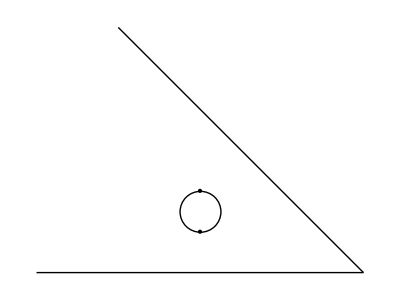

```mathematica
Graphics[{Line[{{-4,-2},{4,-2}}],Line[{{-2,4},{4,-2}}],Point[{0,0}],Point[{0,-1}],Circle[{0,-1/2},1/2]}]
```

#### cm -> 2, p1 -> 0, p2 -> 0, cn -> -2, q1 -> -2, q2 -> -3

```mathematica
cubic=paramcubic/.{cm-> 2,p1-> 0,p2-> 0,cn-> -2,q1-> -2,q2-> -3}
```

-3-8 t-5 t^2+2 t^3

```mathematica
Discriminant[cubic,t]
```

-1096

```mathematica
Solve[cubic== 0,t,Reals]
```

{{t→Root[-3-8 #1-5 #1^2+2 #1^3&,1]}}

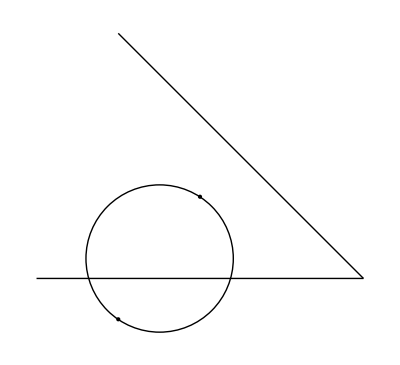

```mathematica
Graphics[{Line[{{-4,-2},{4,-2}}],Line[{{-2,4},{4,-2}}],Point[{0,0}],Point[{-2,-3}],Circle[{-1,-3/2},Sqrt[(-2+1)^2+(-3+3/2)^2]]}]
```

#### cm -> 2, p1 -> 0, p2 -> 0, cn -> -2, q1 -> 6, q2 -> -3

```mathematica
cubic=paramcubic/.{cm-> 2,p1-> 0,p2-> 0,cn-> -2,q1-> 6,q2-> -3}
```

5+8 t-13 t^2+2 t^3

```mathematica
Discriminant[cubic,t]
```

29240

```mathematica
Solve[cubic== 0,t,Reals]
```

{{t→Root[5+8 #1-13 #1^2+2 #1^3&,1]},{t→Root[5+8 #1-13 #1^2+2 #1^3&,2]},{t→Root[5+8 #1-13 #1^2+2 #1^3&,3]}}

```mathematica
Solve[{cst1==0,cst2==0,cst3== 0,cst4== 0,cst5== 0}//.{t->Root[5+8 #1-13 #1^2+2 #1^3&,1],cm-> 2,p1-> 0,p2-> 0,cn-> -2,q1-> 6,q2-> -3},{x1,x2,y1,y2}]//N
```

{{x1→-0.757122,x2→6.0262,y1→-0.856692,y2→-3.42459}}

```mathematica
Solve[{cst1==0,cst2==0,cst3== 0,cst4== 0,cst5== 0}//.{t->Root[5+8 #1-13 #1^2+2 #1^3&,2],cm-> 2,p1-> 0,p2-> 0,cn-> -2,q1-> 6,q2-> -3},{x1,x2,y1,y2}]//N
```

{{x1→2.30704,x2→47.929,y1→0.330611,y2→52.9565}}

```mathematica
Solve[{cst1==0,cst2==0,cst3== 0,cst4== 0,cst5== 0}//.{t->Root[5+8 #1-13 #1^2+2 #1^3&,3],cm-> 2,p1-> 0,p2-> 0,cn-> -2,q1-> 6,q2-> -3},{x1,x2,y1,y2}]//N
```

{{x1→11.4501,x2→5.54479,y1→31.7761,y2→-2.03193}}

```mathematica
e1=-3/6k+1
```

1-k/2

```mathematica
e2=-3/2-k*3-c
```

-3/2-c-3 k

```mathematica
Solve[{e1==0,e2==0},{k,c}]
```

{{k→2,c→-15/2}}

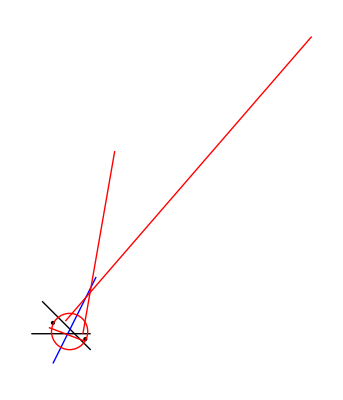

```mathematica
Graphics[{Line[{{-4,-2},{7,-2}}],Line[{{-2,4},{7,-5}}],Point[{0,0}],Point[{6,-3}],Blue,Line[{{0,-15/2},{8,17/2}}],Red,Line[{{-0.7571220465118697,-0.8566915516714195},{6.026196565838601,-3.4245915866338414}}],Line[{{2.307042527975936,0.3306113064723992},{47.92901260878067,52.956523899703484}}],Line[{{11.450079518535933,31.77608024519902},{5.54479082538082,-2.031932313069586}}],Circle[{3,-3/2},Sqrt[(3)^2+(-3/2)^2]]}]
```

```mathematica
cst1=y1+cm
```

cm+y1

```mathematica
cst2=x2+y2+cn
```

cn+x2+y2

```mathematica
cst3=(0-y1)t+(0-x1)
```

-x1-t y1

```mathematica
cst4=(-3-y2)t+(6-x2)
```

6-x2+t (-3-y2)

```mathematica
cst5=t (0+x1)/2+k-(0+y1)/2
```

k+(t x1)/2-y1/2

```mathematica
cst6=t(6+x2)/2+k-(-3+y2)/2
```

k+1/2 t (6+x2)+(3-y2)/2

```mathematica
GroebnerBasis[{cst1,cst2,cst3,cst4,cst5,cst6},{t},{x1,x2,y1,y2,k}]
```

{9-cm+cn+6 t+cm t-9 t^2-cm t^2+cn t^2+cm t^3}

```mathematica
Collect[%[[1]],{t,t^2,t^3}]
```

9-cm+cn+(6+cm) t+(-9-cm+cn) t^2+cm t^3

```mathematica
cst1=am x1+bm y1+cm
```

cm+am x1+bm y1

```mathematica
cst2=an x2+bn y2+cn
```

cn+an x2+bn y2

```mathematica
cst3=(p2-y1)t+(p1-x1)
```

p1-x1+t (p2-y1)

```mathematica
cst4=(q2-y2)t+(q1-x2)
```

q1-x2+t (q2-y2)

```mathematica
cst5=t (p1+x1)/2+k-(p2+y1)/2
```

k+1/2 t (p1+x1)+1/2 (-p2-y1)

```mathematica
cst6=t(q1+x2)/2+k-(q2+y2)/2
```

k+1/2 t (q1+x2)+1/2 (-q2-y2)

```mathematica
gbt=GroebnerBasis[{cst1,cst2,cst3,cst4,cst5,cst6},{t},{x1,x2,y1,y2,k}]
```

{-bn cm+bm cn-am bn p1+bm bn p2+an bm q1-bm bn q2+an cm t-am cn t+am an p1 t-2 bm bn p1 t-an bm p2 t-2 am bn p2 t-am an q1 t+2 bm bn q1 t+2 an bm q2 t+am bn q2 t-bn cm t^2+bm cn t^2+2 an bm p1 t^2+am bn p1 t^2+2 am an p2 t^2-bm bn p2 t^2-an bm q1 t^2-2 am bn q1 t^2-2 am an q2 t^2+bm bn q2 t^2+an cm t^3-am cn t^3-am an p1 t^3+an bm p2 t^3+am an q1 t^3-am bn q2 t^3}

```mathematica
gbt=Collect[%[[1]],{t,t^2,t^3}]
```

-bn cm+bm cn-am bn p1+bm bn p2+an bm q1-bm bn q2+(an cm-am cn+am an p1-2 bm bn p1-an bm p2-2 am bn p2-am an q1+2 bm bn q1+2 an bm q2+am bn q2) t+(-bn cm+bm cn+2 an bm p1+am bn p1+2 am an p2-bm bn p2-an bm q1-2 am bn q1-2 am an q2+bm bn q2) t^2+(an cm-am cn-am an p1+an bm p2+am an q1-am bn q2) t^3

```mathematica
t2=D[gbt,t]
```

an cm-am cn+am an p1-2 bm bn p1-an bm p2-2 am bn p2-am an q1+2 bm bn q1+2 an bm q2+am bn q2+2 (-bn cm+bm cn+2 an bm p1+am bn p1+2 am an p2-bm bn p2-an bm q1-2 am bn q1-2 am an q2+bm bn q2) t+3 (an cm-am cn-am an p1+an bm p2+am an q1-am bn q2) t^2

```mathematica
Solve[Discriminant[t2,t]== 0,{p1,p2,q1,q2}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{p1→(2 an bm bn cm-2 am bn^2 cm+4 an bm^2 cn-4 am bm bn cn+2 am an^2 bm p2-2 am^2 an bn p2+2 an bm^2 bn p2-2 am bm bn^2 p2-6 am^2 an^2 q1-4 an^2 bm^2 q1+2 am an bm bn q1-4 am^2 bn^2 q1-2 am an^2 bm q2+2 am^2 an bn q2+4 an bm^2 bn q2-4 am bm bn^2 q2-√((-2 an bm bn cm+2 am bn^2 cm-4 an bm^2 cn+4 am bm bn cn-2 am an^2 bm p2+2 am^2 an bn p2-2 an bm^2 bn p2+2 am bm bn^2 p2+6 am^2 an^2 q1+4 an^2 bm^2 q1-2 am an bm bn q1+4 am^2 bn^2 q1+2 am an^2 bm q2-2 am^2 an bn q2-4 an bm^2 bn q2+4 am bm bn^2 q2)^2-4 (-3 am^2 an^2-4 an^2 bm^2+2 am an bm bn-am^2 bn^2) (3 an^2 cm^2-bn^2 cm^2-6 am an cm cn+2 bm bn cm cn+3 am^2 cn^2-bm^2 cn^2-2 am an bn cm p2-2 bm bn^2 cm p2-4 am an bm cn p2+6 am^2 bn cn p2+2 bm^2 bn cn p2-4 am^2 an^2 p2^2-3 an^2 bm^2 p2^2-2 am an bm bn p2^2-bm^2 bn^2 p2^2+4 an bm bn cm q1-4 am bn^2 cm q1+2 an bm^2 cn q1-2 am bm bn cn q1-2 am an^2 bm p2 q1+2 am^2 an bn p2 q1+4 an bm^2 bn p2 q1-4 am bm bn^2 p2 q1-3 am^2 an^2 q1^2-an^2 bm^2 q1^2+2 am an bm bn q1^2-4 am^2 bn^2 q1^2+6 an^2 bm cm q2-4 am an bn cm q2+2 bm bn^2 cm q2-2 am an bm cn q2-2 bm^2 bn cn q2+8 am^2 an^2 p2 q2+6 an^2 bm^2 p2 q2-2 am an bm bn p2 q2+6 am^2 bn^2 p2 q2+2 bm^2 bn^2 p2 q2+2 am an^2 bm q1 q2-2 am^2 an bn q1 q2+2 an bm^2 bn q1 q2-2 am bm bn^2 q1 q2-4 am^2 an^2 q2^2-2 am an bm bn q2^2-3 am^2 bn^2 q2^2-bm^2 bn^2 q2^2)))/(2 (-3 am^2 an^2-4 an^2 bm^2+2 am an bm bn-am^2 bn^2))},{p1→(2 an bm bn cm-2 am bn^2 cm+4 an bm^2 cn-4 am bm bn cn+2 am an^2 bm p2-2 am^2 an bn p2+2 an bm^2 bn p2-2 am bm bn^2 p2-6 am^2 an^2 q1-4 an^2 bm^2 q1+2 am an bm bn q1-4 am^2 bn^2 q1-2 am an^2 bm q2+2 am^2 an bn q2+4 an bm^2 bn q2-4 am bm bn^2 q2+√((-2 an bm bn cm+2 am bn^2 cm-4 an bm^2 cn+4 am bm bn cn-2 am an^2 bm p2+2 am^2 an bn p2-2 an bm^2 bn p2+2 am bm bn^2 p2+6 am^2 an^2 q1+4 an^2 bm^2 q1-2 am an bm bn q1+4 am^2 bn^2 q1+2 am an^2 bm q2-2 am^2 an bn q2-4 an bm^2 bn q2+4 am bm bn^2 q2)^2-4 (-3 am^2 an^2-4 an^2 bm^2+2 am an bm bn-am^2 bn^2) (3 an^2 cm^2-bn^2 cm^2-6 am an cm cn+2 bm bn cm cn+3 am^2 cn^2-bm^2 cn^2-2 am an bn cm p2-2 bm bn^2 cm p2-4 am an bm cn p2+6 am^2 bn cn p2+2 bm^2 bn cn p2-4 am^2 an^2 p2^2-3 an^2 bm^2 p2^2-2 am an bm bn p2^2-bm^2 bn^2 p2^2+4 an bm bn cm q1-4 am bn^2 cm q1+2 an bm^2 cn q1-2 am bm bn cn q1-2 am an^2 bm p2 q1+2 am^2 an bn p2 q1+4 an bm^2 bn p2 q1-4 am bm bn^2 p2 q1-3 am^2 an^2 q1^2-an^2 bm^2 q1^2+2 am an bm bn q1^2-4 am^2 bn^2 q1^2+6 an^2 bm cm q2-4 am an bn cm q2+2 bm bn^2 cm q2-2 am an bm cn q2-2 bm^2 bn cn q2+8 am^2 an^2 p2 q2+6 an^2 bm^2 p2 q2-2 am an bm bn p2 q2+6 am^2 bn^2 p2 q2+2 bm^2 bn^2 p2 q2+2 am an^2 bm q1 q2-2 am^2 an bn q1 q2+2 an bm^2 bn q1 q2-2 am bm bn^2 q1 q2-4 am^2 an^2 q2^2-2 am an bm bn q2^2-3 am^2 bn^2 q2^2-bm^2 bn^2 q2^2)))/(2 (-3 am^2 an^2-4 an^2 bm^2+2 am an bm bn-am^2 bn^2))}}

## (O7)

### (O7) - lines are not parallel

All parabola are similar.

```mathematica
P=OPoint[0,0];
```

```mathematica
m=OLine[0,1,cm];n=OLine[an,bn,cn];
```

```mathematica
parabolaeq1=ODistance[OPoint[x,y],P]^2-ODistanceSq[OPoint[x,y],m]//Expand
```

-cm^2+x^2-2 cm y

```mathematica
tgparabola1=(D[parabolaeq1,x]/.{x-> x1, y-> y1})+ (D[parabolaeq1,y]/.{x-> x1, y-> y1})t
```

-2 cm t+2 x1

```mathematica
cst1=parabolaeq1/.{x-> x1,y-> y1}
```

-cm^2+x1^2-2 cm y1

```mathematica
cst2=an t -bn
```

-bn+an t

```mathematica
sols=Solve[{cst1== 0,cst2== 0,tgparabola1==0},{t,x1,y1}]//FullSimplify
```

{{t→bn/an,x1→(bn cm)/an,y1→1/2 (-1+bn^2/an^2) cm}}

Example

```mathematica
sols/.{an->1,bn-> 1}
```

{{t→1,x1→cm,y1→0}}

### (O7) - lines are parallel

All parabola are similar.

```mathematica
P=OPoint[p1,p2];
```

```mathematica
m=OLine[am,bm,cm];n=OLine[am,bm,cn];
```

```mathematica
parabolaeq1=ODistance[OPoint[x,y],P]^2-ODistanceSq[OPoint[x,y],m]//Expand
```

-cm^2/(am^2+bm^2)+p1^2+p2^2-(2 am cm x)/(am^2+bm^2)-2 p1 x+x^2-(am^2 x^2)/(am^2+bm^2)-(2 bm cm y)/(am^2+bm^2)-2 p2 y-(2 am bm x y)/(am^2+bm^2)+y^2-(bm^2 y^2)/(am^2+bm^2)

```mathematica
parabolaeq1=(am^2+bm^2)((x-p1)^2+(y-p2)^2)-(am x+bm y+ cm)^2
```

-(cm+am x+bm y)^2+(am^2+bm^2) ((-p1+x)^2+(-p2+y)^2)

```mathematica
tgparabola1=(D[parabolaeq1,x]/.{x-> x1, y-> y1})+ (D[parabolaeq1,y]/.{x-> x1, y-> y1})t
```

2 (am^2+bm^2) (-p1+x1)-2 am (cm+am x1+bm y1)+t (2 (am^2+bm^2) (-p2+y1)-2 bm (cm+am x1+bm y1))

```mathematica
cst1=parabolaeq1/.{x-> x1,y-> y1}
```

-(cm+am x1+bm y1)^2+(am^2+bm^2) ((-p1+x1)^2+(-p2+y1)^2)

```mathematica
cst2= am t -bm
```

-bm+am t

```mathematica
sols=Solve[{cst1== 0,cst2== 0,tgparabola1==0},{t,x1,y1}]//FullSimplify
```

{}

Example

```mathematica
Solve[{cst1== 0,cst2== 0,tgparabola1==0}//.{am-> 1,bm-> 1},{t,x1,y1}]
```

{}

### (O7) General

All parabola are similar.

```mathematica
P=OPoint[p1,p2];
```

```mathematica
m=OLine[am,bm,cm];n=OLine[an,bn,cn];
```

```mathematica
parabolaeq1=ODistance[OPoint[x,y],P]^2-ODistanceSq[OPoint[x,y],m]//Expand
```

-cm^2/(am^2+bm^2)+p1^2+p2^2-(2 am cm x)/(am^2+bm^2)-2 p1 x+x^2-(am^2 x^2)/(am^2+bm^2)-(2 bm cm y)/(am^2+bm^2)-2 p2 y-(2 am bm x y)/(am^2+bm^2)+y^2-(bm^2 y^2)/(am^2+bm^2)

```mathematica
parabolaeq1=(am^2+bm^2)((x-p1)^2+(y-p2)^2)-(am x+bm y+ cm)^2
```

-(cm+am x+bm y)^2+(am^2+bm^2) ((-p1+x)^2+(-p2+y)^2)

```mathematica
tgparabola1=(D[parabolaeq1,x]/.{x-> x1, y-> y1})+ (D[parabolaeq1,y]/.{x-> x1, y-> y1})t
```

2 (am^2+bm^2) (-p1+x1)-2 am (cm+am x1+bm y1)+t (2 (am^2+bm^2) (-p2+y1)-2 bm (cm+am x1+bm y1))

```mathematica
cst1=parabolaeq1/.{x-> x1,y-> y1}
```

-(cm+am x1+bm y1)^2+(am^2+bm^2) ((-p1+x1)^2+(-p2+y1)^2)

```mathematica
cst2= an t -bn
```

-bn+an t

```mathematica
List@@LineCC[Line[am,bm,cm]]
```

{(-1+bm) bm==0,(-1+am) (-1+bm)==0}

```mathematica
List@@LineCC[Line[an,bn,cn]]
```

{(-1+bn) bn==0,(-1+an) (-1+bn)==0}

```mathematica
Join[{cst1== 0,cst2== 0,tgparabola1==0},List@@LineCC[Line[am,bm,cm]],List@@LineCC[Line[an,bn,cn]]]
```

{-(cm+am x1+bm y1)^2+(am^2+bm^2) ((-p1+x1)^2+(-p2+y1)^2)==0,-bn+an t==0,2 (am^2+bm^2) (-p1+x1)-2 am (cm+am x1+bm y1)+t (2 (am^2+bm^2) (-p2+y1)-2 bm (cm+am x1+bm y1))==0,(-1+bm) bm==0,(-1+am) (-1+bm)==0,(-1+bn) bn==0,(-1+an) (-1+bn)==0}

```mathematica
sols=Solve[{cst1== 0,cst2== 0,tgparabola1==0},{x1,y1,t}]
```

{{x1→1/(2 (an bm-am bn)^2)(am an^2 cm+2 an bm bn cm-am bn^2 cm+am^2 an^2 p1+2 an^2 bm^2 p1-2 am an bm bn p1+am^2 bn^2 p1+am an^2 bm p2+2 an bm^2 bn p2-am bm bn^2 p2),y1→1/(2 (an bm-am bn)^2)(-an^2 bm cm+2 am an bn cm+bm bn^2 cm-am an^2 bm p1+2 am^2 an bn p1+am bm bn^2 p1+an^2 bm^2 p2-2 am an bm bn p2+2 am^2 bn^2 p2+bm^2 bn^2 p2),t→bn/an}}

```mathematica
GroebnerBasis[Join[{cst1== 0,cst2== 0,tgparabola1==0},List@@LineCC[Line[am,bm,cm]],List@@LineCC[Line[an,bn,cn]]],{x1},{y1,t}]//FullSimplify
```

{-(am^2+bm^2) (cm+am p1+bm p2) (am (an^2 (cm+bm p2)-bn^2 (cm+bm p2)-2 an bm bn (p1-2 x1))+am^2 (an^2 p1+bn^2 (p1-2 x1))+2 an bm (bn (cm+bm p2)+an bm (p1-x1)))}

### (O7) General GB

All parabola are similar.

```mathematica
P=OPoint[p1,p2];
```

```mathematica
m=OLine[am,bm,cm];n=OLine[an,bn,cn];
```

```mathematica
parabolaeq1=ODistance[OPoint[x,y],P]^2-ODistanceSq[OPoint[x,y],m]//Expand
```

-cm^2/(am^2+bm^2)+p1^2+p2^2-(2 am cm x)/(am^2+bm^2)-2 p1 x+x^2-(am^2 x^2)/(am^2+bm^2)-(2 bm cm y)/(am^2+bm^2)-2 p2 y-(2 am bm x y)/(am^2+bm^2)+y^2-(bm^2 y^2)/(am^2+bm^2)

```mathematica
parabolaeq1=(am^2+bm^2)((x-p1)^2+(y-p2)^2)-(am x+bm y+ cm)^2
```

-(cm+am x+bm y)^2+(am^2+bm^2) ((-p1+x)^2+(-p2+y)^2)

```mathematica
tgparabola1=(D[parabolaeq1,x]/.{x-> x1, y-> y1})+ (D[parabolaeq1,y]/.{x-> x1, y-> y1})t
```

2 (am^2+bm^2) (-p1+x1)-2 am (cm+am x1+bm y1)+t (2 (am^2+bm^2) (-p2+y1)-2 bm (cm+am x1+bm y1))

```mathematica
cst1=parabolaeq1/.{x-> x1,y-> y1}
```

-(cm+am x1+bm y1)^2+(am^2+bm^2) ((-p1+x1)^2+(-p2+y1)^2)

```mathematica
cst2= an t -bn
```

-bn+an t

```mathematica
List@@LineCC[Line[am,bm,cm]]
```

{(-1+bm) bm==0,(-1+am) (-1+bm)==0,1+am^2≠0}

```mathematica
List@@LineCC[Line[an,bn,cn]]
```

{(-1+bn) bn==0,(-1+an) (-1+bn)==0,1+an^2≠0}

```mathematica
Join[{cst1== 0,cst2== 0,tgparabola1==0},List@@LineCC[Line[am,bm,cm]],List@@LineCC[Line[an,bn,cn]]]
```

{-(cm+am x1+bm y1)^2+(am^2+bm^2) ((-p1+x1)^2+(-p2+y1)^2)==0,-bn+an t==0,2 (am^2+bm^2) (-p1+x1)-2 am (cm+am x1+bm y1)+t (2 (am^2+bm^2) (-p2+y1)-2 bm (cm+am x1+bm y1))==0,(-1+bm) bm==0,(-1+am) (-1+bm)==0,1+am^2≠0,(-1+bn) bn==0,(-1+an) (-1+bn)==0,1+an^2≠0}

```mathematica
gb=GroebnerBasis[{cst1== 0,cst2== 0,tgparabola1==0},{x1,y1},{t,η}]
```

{am^2 an^2 bm cm^2+an^2 bm^3 cm^2-2 am^3 an bn cm^2-2 am an bm^2 bn cm^2-am^2 bm bn^2 cm^2-bm^3 bn^2 cm^2+2 am^3 an^2 bm cm p1+2 am an^2 bm^3 cm p1-4 am^4 an bn cm p1-4 am^2 an bm^2 bn cm p1-2 am^3 bm bn^2 cm p1-2 am bm^3 bn^2 cm p1+am^4 an^2 bm p1^2+am^2 an^2 bm^3 p1^2-2 am^5 an bn p1^2-2 am^3 an bm^2 bn p1^2-am^4 bm bn^2 p1^2-am^2 bm^3 bn^2 p1^2-2 am^4 bn^2 cm p2-4 am^2 bm^2 bn^2 cm p2-2 bm^4 bn^2 cm p2-2 am^5 bn^2 p1 p2-4 am^3 bm^2 bn^2 p1 p2-2 am bm^4 bn^2 p1 p2-am^2 an^2 bm^3 p2^2-an^2 bm^5 p2^2+2 am^3 an bm^2 bn p2^2+2 am an bm^4 bn p2^2-2 am^4 bm bn^2 p2^2-3 am^2 bm^3 bn^2 p2^2-bm^5 bn^2 p2^2+2 am^2 an^2 bm^2 cm y1+2 an^2 bm^4 cm y1-4 am^3 an bm bn cm y1-4 am an bm^3 bn cm y1+2 am^4 bn^2 cm y1+2 am^2 bm^2 bn^2 cm y1+2 am^3 an^2 bm^2 p1 y1+2 am an^2 bm^4 p1 y1-4 am^4 an bm bn p1 y1-4 am^2 an bm^3 bn p1 y1+2 am^5 bn^2 p1 y1+2 am^3 bm^2 bn^2 p1 y1+2 am^2 an^2 bm^3 p2 y1+2 an^2 bm^5 p2 y1-4 am^3 an bm^2 bn p2 y1-4 am an bm^4 bn p2 y1+2 am^4 bm bn^2 p2 y1+2 am^2 bm^3 bn^2 p2 y1,am an cm+bm bn cm+am^2 an p1+an bm^2 p1+am^2 bn p2+bm^2 bn p2-an bm^2 x1+am bm bn x1+am an bm y1-am^2 bn y1,-am an^2 bm cm^2-2 am^2 an bn cm^2-2 an bm^2 bn cm^2-am bm bn^2 cm^2-2 am^2 an^2 bm cm p1-an^2 bm^3 cm p1-4 am^3 an bn cm p1-5 am an bm^2 bn cm p1-2 am^2 bm bn^2 cm p1-2 bm^3 bn^2 cm p1-am^3 an^2 bm p1^2-am an^2 bm^3 p1^2-2 am^4 an bn p1^2-3 am^2 an bm^2 bn p1^2-an bm^4 bn p1^2-am^3 bm bn^2 p1^2-am bm^3 bn^2 p1^2-am an^2 bm^2 cm p2-2 am^2 an bm bn cm p2-2 an bm^3 bn cm p2-2 am^3 bn^2 cm p2-3 am bm^2 bn^2 cm p2-am^2 an^2 bm^2 p1 p2-an^2 bm^4 p1 p2-2 am^3 an bm bn p1 p2-2 am an bm^3 bn p1 p2-2 am^4 bn^2 p1 p2-4 am^2 bm^2 bn^2 p1 p2-2 bm^4 bn^2 p1 p2-2 am^3 bm bn^2 p2^2-2 am bm^3 bn^2 p2^2+an^2 bm^3 cm x1+bm^3 bn^2 cm x1+am an^2 bm^3 p1 x1+an bm^4 bn p1 x1+an^2 bm^4 p2 x1+bm^4 bn^2 p2 x1-am an^2 bm^2 cm y1-2 am^2 an bm bn cm y1-2 an bm^3 bn cm y1+2 am^3 bn^2 cm y1+am bm^2 bn^2 cm y1-am^2 an^2 bm^2 p1 y1-2 am^3 an bm bn p1 y1-3 am an bm^3 bn p1 y1+2 am^4 bn^2 p1 y1+2 am^2 bm^2 bn^2 p1 y1-am an^2 bm^3 p2 y1-2 am^2 an bm^2 bn p2 y1-2 an bm^4 bn p2 y1+2 am^3 bm bn^2 p2 y1+am bm^3 bn^2 p2 y1,-2 am^2 an cm^2-an bm^2 cm^2-am bm bn cm^2-4 am^3 an cm p1-4 am an bm^2 cm p1-2 am^2 bm bn cm p1-2 bm^3 bn cm p1-2 am^4 an p1^2-3 am^2 an bm^2 p1^2-an bm^4 p1^2-am^3 bm bn p1^2-am bm^3 bn p1^2-am^2 an bm cm p2-2 am^3 bn cm p2-3 am bm^2 bn cm p2-am^3 an bm p1 p2-am an bm^3 p1 p2-2 am^4 bn p1 p2-4 am^2 bm^2 bn p1 p2-2 bm^4 bn p1 p2+am^2 an bm^2 p2^2+an bm^4 p2^2-2 am^3 bm bn p2^2-2 am bm^3 bn p2^2+am an bm^2 cm x1+bm^3 bn cm x1+am^2 an bm^2 p1 x1+an bm^4 p1 x1+am an bm^3 p2 x1+bm^4 bn p2 x1-3 am^2 an bm cm y1-2 an bm^3 cm y1+2 am^3 bn cm y1+am bm^2 bn cm y1-3 am^3 an bm p1 y1-3 am an bm^3 p1 y1+2 am^4 bn p1 y1+2 am^2 bm^2 bn p1 y1-3 am^2 an bm^2 p2 y1-2 an bm^4 p2 y1+2 am^3 bm bn p2 y1+am bm^3 bn p2 y1,-an bm cm^2+am bn cm^2-2 am an bm cm p1-2 bm^2 bn cm p1-am^2 an bm p1^2-an bm^3 p1^2-am^3 bn p1^2-am bm^2 bn p1^2-am^2 an cm p2-am bm bn cm p2-am^3 an p1 p2-am an bm^2 p1 p2-2 am^2 bm bn p1 p2-2 bm^3 bn p1 p2+am^2 an bm p2^2+an bm^3 p2^2-2 am^3 bn p2^2-2 am bm^2 bn p2^2-am an bm cm x1+2 am^2 bn cm x1+bm^2 bn cm x1-am^2 an bm p1 x1+an bm^3 p1 x1+2 am^3 bn p1 x1+am an bm^2 p2 x1+bm^3 bn p2 x1-am^2 an cm y1-2 an bm^2 cm y1+am bm bn cm y1-am^3 an p1 y1-3 am an bm^2 p1 y1+2 am^2 bm bn p1 y1-3 am^2 an bm p2 y1-2 an bm^3 p2 y1+2 am^3 bn p2 y1+am bm^2 bn p2 y1,-cm^2+am^2 p1^2+bm^2 p1^2+am^2 p2^2+bm^2 p2^2-2 am cm x1-2 am^2 p1 x1-2 bm^2 p1 x1+bm^2 x1^2-2 bm cm y1-2 am^2 p2 y1-2 bm^2 p2 y1-2 am bm x1 y1+am^2 y1^2}

```mathematica
Solve[(#==0)&/@gb,{x1,y1}]
```

{{x1→(am an^2 cm+2 an bm bn cm-am bn^2 cm+am^2 an^2 p1+2 an^2 bm^2 p1-2 am an bm bn p1+am^2 bn^2 p1+am an^2 bm p2+2 an bm^2 bn p2-am bm bn^2 p2)/(2 (an bm-am bn)^2),y1→(-an^2 bm cm+2 am an bn cm+bm bn^2 cm-am an^2 bm p1+2 am^2 an bn p1+am bm bn^2 p1+an^2 bm^2 p2-2 am an bm bn p2+2 am^2 bn^2 p2+bm^2 bn^2 p2)/(2 (an bm-am bn)^2)}}

```mathematica
GroebnerBasis[Join[{cst1== 0,cst2== 0,tgparabola1==0},List@@LineCC[Line[am,bm,cm]],List@@LineCC[Line[an,bn,cn]]],{x1},{y1,t}]//FullSimplify
```

{-(am^2+bm^2) (cm+am p1+bm p2) (am (an^2 (cm+bm p2)-bn^2 (cm+bm p2)-2 an bm bn (p1-2 x1))+am^2 (an^2 p1+bn^2 (p1-2 x1))+2 an bm (bn (cm+bm p2)+an bm (p1-x1)))}

## Function definition

```mathematica
Clear[ODistance]
```

```mathematica
Clear[ODistanceSq]
```

```mathematica
ODistance[OPoint[x_,y_],OPoint[u_,v_]]:=√((x-u)^2+(y-v)^2)
```

```mathematica
ODistanceSq[OPoint[x_,y_],OPoint[u_,v_]]:=(x-u)^2+(y-v)^2
```

```mathematica
ODistance[OPoint[x_,y_],OLine[a_,b_,c_]]:=Abs[a x+b y+ c]/(√(a^2+b^2))
```

```mathematica
ODistanceSq[OPoint[x_,y_],OLine[a_,b_,c_]]:=(a x+b y+ c)^2/(a^2+b^2)
```

```mathematica
ODistanceSq[OLine[a_,b_,c1_],OLine[a_,b_,c2_]]:=(c1-c2)^2/(a^2+b^2)
```

## Intitialization

```mathematica
AppendTo[$Path,"/Users/basho/Dropbox/Eos3/OrigamiBasics"];
```

```mathematica
<<Eos`
```

Get::noopen: Cannot open "g3`".

Needs::nocont: Context "g3`" was not created when Needs was evaluated.

Get::noopen: Cannot open "g3`".

Needs::nocont: Context "g3`" was not created when Needs was evaluated.

System`Twist::shdw: Symbol "Twist" appears in multiple contexts {"System`", "Common`"}; definitions in context "System`" may shadow or be shadowed by other definitions.

Get::noopen: Cannot open "g3`".

Needs::nocont: Context "g3`" was not created when Needs was evaluated.

Get::noopen: Cannot open "g3`".

Needs::nocont: Context "g3`" was not created when Needs was evaluated.

Get::noopen: Cannot open "g3`".

Needs::nocont: Context "g3`" was not created when Needs was evaluated.

CreateDirectory::privv: Privilege violation during CreateDirectory["/Users/ida/Dropbox/Eos3/ProofDoc/"].

```mathematica
InteractiveFold[False];
```